# Ploidally-antagonstic plots

## Plotting parameters [ENTER]

```mathematica
SetDirectory[NotebookDirectory[]]; (*sets current directory to be location of this file*)
plotdir="Plots/";(*directory to save figures in*)
```

```mathematica
Pad={{50,10},{50,10}};  (*space around plot*)
letpos={.05,.93};  (*relative location of letter, eg A, in figure*)
ylabpos={-0.125,0.5};  (*relative location of y axis label position*)

inches=72;
lwd=0.006;(*line thickness as fraction of plot width*)
ticksize={0,0.01};
xsize=5inches;
aspectratio=1/Sqrt[2];
```

# Region:

## Life-cycle [ENTER]

### Haploid competition

Frequency of haploids from each sex

```mathematica
Subscript[freqHap, sex_]:=ParallelSum[Subscript[fHap, x,y,z,sex],{x,{X,Y}},{y,{A,a}},{z,{M,m}}]
```

Mean haploid fitness of gametes from each sex

```mathematica
Subscript[wbarHap, sex_]:=Subscript[wbarHap, sex]=ParallelSum[Subscript[wHap, y,sex] Subscript[fHap, x,y,z,sex],{x,{X,Y}},{y,{A,a}},{z,{M,m}}]/Subscript[freqHap, sex]
```

Frequencies of haploid genotypes from each sex following haploid competition, which occurs between gametes coming from the same sex

```mathematica
Subscript[fHapSel, x_,y_,z_,sex_]:=(Subscript[wHap, y,sex] Subscript[fHap, x,y,z,sex])/(Subscript[wbarHap, sex] Subscript[freqHap, sex])
```

### Random mating

Gametes from the two sexes pair at random

```mathematica
Subscript[fDip, xM_,yM_,zM_,xP_,yP_,zP_]:=Subscript[fDip, xM,yM,zM,xP,yP,zP]=Subscript[fHapSel, xM,yM,zM,female] Subscript[fHapSel, xP,yP,zP,male]
```

### Sex determination

Determine the sex of newly formed diploids

```mathematica
Subscript[fDipSex, xM_,yM_,zM_,xP_,yP_,zP_,sex_]:=Subscript[fDipSex, xM,yM,zM,xP,yP,zP,sex]=Subscript[fDip, xM,yM,zM,xP,yP,zP] Subscript[psex, zM,xP,zP,sex]
```

where a diploid must become male or female

```mathematica
sumsex=Subscript[psex, zM_,xP_,zP_,male]->1-Subscript[psex, zM,xP,zP,female];
```

Rules for invasion of a dominant modifier into an XY system (relabeling males and females and females as males, as well as Y as W and X as Z makes the ancestral system ZW)

```mathematica
invXY={
Subscript[psex, M,Y,M,female]->0,(*always male if neo-SD allele wildtype and have Y*)
Subscript[psex, M,X,M,female]->1,(*always female neo-SD allele wildtype and have X from father*)
Subscript[psex, m,xP_,zP_,female]->k,(*female with probability k if mutation at the maternal neo-SD locus*)
Subscript[psex, zM_,xP_,m,female]->k (*female with probability k if mutation at the paternal neo-SD locus*)
};
```

### Diploid selection

Frequencies of diploids from each sex

```mathematica
Subscript[freqDip, sex_]:=ParallelSum[Subscript[fDipSex, xM,yM,zM,xP,yP,zP,sex],{xM,{X,Y}},{yM,{A,a}},{zM,{M,m}},{xP,{X,Y}},{yP,{A,a}},{zP,{M,m}}]
```

Mean diploid fitness in each sex

```mathematica
Subscript[wbarDip, sex_]:=Subscript[wbarDip, sex]=ParallelSum[Subscript[wDip, yM,yP,sex] Subscript[fDipSex, xM,yM,zM,xP,yP,zP,sex],{xM,{X,Y}},{yM,{A,a}},{zM,{M,m}},{xP,{X,Y}},{yP,{A,a}},{zP,{M,m}}]/Subscript[freqDip, sex]
```

Frequencies of diploid genotypes in each sex following diploid selection, which occurs separately in each sex (even if diploid selection is not direct competition between members of the same sex but instead viability selection, selection still effectively occurs ‘separately in each sex’ because the next generation is sired by 50% males and 50% females)

```mathematica
Subscript[fDipSel, xM_,yM_,zM_,xP_,yP_,zP_,sex_]:=Subscript[fDipSel, xM,yM,zM,xP,yP,zP,sex]=(Subscript[wDip, yM,yP,sex] Subscript[fDipSex, xM,yM,zM,xP,yP,zP,sex])/(Subscript[wbarDip, sex] Subscript[freqDip, sex])
```

### Meiosis

Gamete genotypes produced by diploids

```mathematica
Subscript[fHapNext, x_,y_,z_,sex_]:=Subscript[fHapNext, x,y,z,sex]=ParallelSum[Subscript[fDipSel, xM,yM,zM,xP,yP,zP,sex] Subscript[pseg, xM,yM,zM,xP,yP,zP,sex,x,y,z],{xM,{X,Y}},{yM,{A,a}},{zM,{M,m}},{xP,{X,Y}},{yP,{A,a}},{zP,{M,m}}]
```

#### Segregation

```mathematica
pseg0={
(*triple homozygote*)
Subscript[pseg, x1_,y1_,z1_,x1_,y1_,z1_,sex_,x1_,y1_,z1_]->1
};
pseg1={
(*single heterozygotes*)
Subscript[pseg, x1_,y1_,z1_,x2_,y1_,z1_,sex_,x1_,y1_,z1_]->1/2,
Subscript[pseg, x1_,y1_,z1_,x2_,y1_,z1_,sex_,x2_,y1_,z1_]->1/2,
Subscript[pseg, x1_,A,z1_,x1_,a,z1_,sex_,x1_,A,z1_]->Subscript[α, sex] ,
Subscript[pseg, x1_,A,z1_,x1_,a,z1_,sex_,x1_,a,z1_]->(1-Subscript[α, sex]),
Subscript[pseg, x1_,a,z1_,x1_,A,z1_,sex_,x1_,A,z1_]->Subscript[α, sex] ,
Subscript[pseg, x1_,a,z1_,x1_,A,z1_,sex_,x1_,a,z1_]->(1-Subscript[α, sex]),
Subscript[pseg, x1_,y1_,z1_,x1_,y1_,z2_,sex_,x1_,y1_,z1_]->1/2,
Subscript[pseg, x1_,y1_,z1_,x1_,y1_,z2_,sex_,x1_,y1_,z2_]->1/2
};
pseg2={
(*double heterozygotes*)
Subscript[pseg, x1_,A,z1_,x2_,a,z1_,sex_,x1_,A,z1_]->Subscript[α, sex](1-(recAXandAM+recAXnotAM)),
Subscript[pseg, x1_,A,z1_,x2_,a,z1_,sex_,x2_,a,z1_]->(1-Subscript[α, sex])(1-(recAXandAM+recAXnotAM)),
Subscript[pseg, x1_,A,z1_,x2_,a,z1_,sex_,x2_,A,z1_]->Subscript[α, sex] (recAXandAM+recAXnotAM),
Subscript[pseg, x1_,A,z1_,x2_,a,z1_,sex_,x1_,a,z1_]->(1-Subscript[α, sex])(recAXandAM+recAXnotAM),
Subscript[pseg, x1_,A,z1_,x1_,a,z2_,sex_,x1_,A,z1_]->Subscript[α, sex](1-(recAXandAM+recAMnotAX)),
Subscript[pseg, x1_,A,z1_,x1_,a,z2_,sex_,x1_,a,z2_]->(1-Subscript[α, sex])(1-(recAXandAM+recAMnotAX)),
Subscript[pseg, x1_,A,z1_,x1_,a,z2_,sex_,x1_,A,z2_]->Subscript[α, sex] (recAXandAM+recAMnotAX),
Subscript[pseg, x1_,A,z1_,x1_,a,z2_,sex_,x1_,a,z1_]->(1-Subscript[α, sex])(recAXandAM+recAMnotAX),
Subscript[pseg, x1_,a,z1_,x2_,A,z1_,sex_,x2_,A,z1_]->Subscript[α, sex] (1-(recAXandAM+recAXnotAM)),
Subscript[pseg, x1_,a,z1_,x2_,A,z1_,sex_,x1_,a,z1_]->(1-Subscript[α, male])(1-(recAXandAM+recAXnotAM)),
Subscript[pseg, x1_,a,z1_,x2_,A,z1_,sex_,x1_,A,z1_]->Subscript[α, sex] (recAXandAM+recAXnotAM),
Subscript[pseg, x1_,a,z1_,x2_,A,z1_,sex_,x2_,a,z1_]->(1-Subscript[α, sex])(recAXandAM+recAXnotAM),
Subscript[pseg, x1_,a,z1_,x1_,A,z2_,sex_,x1_,A,z2_]->Subscript[α, sex] (1-(recAXandAM+recAMnotAX)),
Subscript[pseg, x1_,a,z1_,x1_,A,z2_,sex_,x1_,a,z1_]->(1-Subscript[α, sex])(1-(recAXandAM+recAMnotAX)),
Subscript[pseg, x1_,a,z1_,x1_,A,z2_,sex_,x1_,A,z1_]->Subscript[α, sex] (recAXandAM+recAMnotAX),
Subscript[pseg, x1_,a,z1_,x1_,A,z2_,sex_,x1_,a,z2_]->(1-Subscript[α, sex])(recAXandAM+recAMnotAX),
Subscript[pseg, x1_,y1_,z1_,x2_,y1_,z2_,sex_,x1_,y1_,z1_]->(1-(recAXnotAM+recAMnotAX))/2,
Subscript[pseg, x1_,y1_,z1_,x2_,y1_,z2_,sex_,x2_,y1_,z2_]->(1-(recAXnotAM+recAMnotAX))/2,
Subscript[pseg, x1_,y1_,z1_,x2_,y1_,z2_,sex_,x2_,y1_,z1_]->(recAXnotAM+recAMnotAX)/2,
Subscript[pseg, x1_,y1_,z1_,x2_,y1_,z2_,sex_,x1_,y1_,z2_]->(recAXnotAM+recAMnotAX)/2
};
pseg3={
(*triple heterozygote*)
Subscript[pseg, x1_,A,z1_,x2_,a,z2_,male,x1_,A,z1_]->Subscript[α, male](1-recAMnotAX-recAXnotAM-recAXandAM),
Subscript[pseg, x1_,A,z1_,x2_,a,z2_,male,x2_,a,z2_]->(1-Subscript[α, male])(1-recAMnotAX-recAXnotAM-recAXandAM),
Subscript[pseg, x1_,A,z1_,x2_,a,z2_,male,x2_,A,z1_]->Subscript[α, male] recAXnotAM,
Subscript[pseg, x1_,A,z1_,x2_,a,z2_,male,x1_,a,z2_]->(1-Subscript[α, male])recAXnotAM,
Subscript[pseg, x1_,A,z1_,x2_,a,z2_,male,x1_,A,z2_]->Subscript[α, male] recAMnotAX,
Subscript[pseg, x1_,A,z1_,x2_,a,z2_,male,x2_,a,z1_]->(1-Subscript[α, male])recAMnotAX,
Subscript[pseg, x1_,A,z1_,x2_,a,z2_,male,x2_,A,z2_]->Subscript[α, male] recAXandAM,
Subscript[pseg, x1_,A,z1_,x2_,a,z2_,male,x1_,a,z1_]->(1-Subscript[α, male])recAXandAM,
Subscript[pseg, x1_,a,z1_,x2_,A,z2_,male,x2_,A,z2_]->Subscript[α, male] (1-recAMnotAX-recAXnotAM-recAXandAM),
Subscript[pseg, x1_,a,z1_,x2_,A,z2_,male,x1_,a,z1_]->(1-Subscript[α, male])(1-recAMnotAX-recAXnotAM-recAXandAM),
Subscript[pseg, x1_,a,z1_,x2_,A,z2_,male,x1_,A,z2_]->Subscript[α, male] recAXnotAM,
Subscript[pseg, x1_,a,z1_,x2_,A,z2_,male,x2_,a,z1_]->(1-Subscript[α, male])recAXnotAM,
Subscript[pseg, x1_,a,z1_,x2_,A,z2_,male,x2_,A,z1_]->Subscript[α, male] recAMnotAX,
Subscript[pseg, x1_,a,z1_,x2_,A,z2_,male,x1_,a,z2_]->(1-Subscript[α, male])recAMnotAX,
Subscript[pseg, x1_,a,z1_,x2_,A,z2_,male,x1_,A,z1_]->Subscript[α, male] recAXandAM,
Subscript[pseg, x1_,a,z1_,x2_,A,z2_,male,x2_,a,z2_]->(1-Subscript[α, male]) recAXandAM,
Subscript[pseg, x1_,A,z1_,x2_,a,z2_,female,x1_,A,z1_]->Subscript[α, female](1-recAMnotAX-recAXnotAM-recAXandAM),
Subscript[pseg, x1_,A,z1_,x2_,a,z2_,female,x2_,a,z2_]->(1-Subscript[α, female])(1-recAMnotAX-recAXnotAM-recAXandAM),
Subscript[pseg, x1_,A,z1_,x2_,a,z2_,female,x2_,A,z1_]->Subscript[α, female] recAXnotAM,
Subscript[pseg, x1_,A,z1_,x2_,a,z2_,female,x1_,a,z2_]->(1-Subscript[α, female])recAXnotAM,
Subscript[pseg, x1_,A,z1_,x2_,a,z2_,female,x1_,A,z2_]->Subscript[α, female] recAMnotAX,
Subscript[pseg, x1_,A,z1_,x2_,a,z2_,female,x2_,a,z1_]->(1-Subscript[α, female])recAMnotAX,
Subscript[pseg, x1_,A,z1_,x2_,a,z2_,female,x2_,A,z2_]->Subscript[α, female] recAXandAM,
Subscript[pseg, x1_,A,z1_,x2_,a,z2_,female,x1_,a,z1_]->(1-Subscript[α, female]) recAXandAM,
Subscript[pseg, x1_,a,z1_,x2_,A,z2_,female,x2_,A,z2_]->Subscript[α, female] (1-recAMnotAX-recAXnotAM-recAXandAM),
Subscript[pseg, x1_,a,z1_,x2_,A,z2_,female,x1_,a,z1_]->(1-Subscript[α, female])(1-recAMnotAX-recAXnotAM-recAXandAM),
Subscript[pseg, x1_,a,z1_,x2_,A,z2_,female,x1_,A,z2_]->Subscript[α, female] recAXnotAM,
Subscript[pseg, x1_,a,z1_,x2_,A,z2_,female,x2_,a,z1_]->(1-Subscript[α, female])recAXnotAM,
Subscript[pseg, x1_,a,z1_,x2_,A,z2_,female,x2_,A,z1_]->Subscript[α, female] recAMnotAX,
Subscript[pseg, x1_,a,z1_,x2_,A,z2_,female,x1_,a,z2_]->(1-Subscript[α, female])recAMnotAX,
Subscript[pseg, x1_,a,z1_,x2_,A,z2_,female,x1_,A,z1_]->Subscript[α, female] recAXandAM,
Subscript[pseg, x1_,a,z1_,x2_,A,z2_,female,x2_,a,z2_]->(1-Subscript[α, female]) recAXandAM
};
pseg4=Subscript[pseg, x1_,y1_,z1_,x2_,y2_,z2_,sex_,x_,y_,z_]->0;
```

#### Recombination probabilities for different arrangements of loci

Let the probability of recombination (an odd number of cross-overs) between loci A and X be r, the probability of recombination between A and M be R, and the probability of recombination between X and M be χ.

We can then write, in general,

```mathematica
recGen={
recAXnotAM->(r+χ-R)/2,
recAMnotAX->(R+χ-r)/2,
recAXandAM->(r+R-χ)/2
};
```

and for specific orders of loci we can substitute in the value of χ (alternatively one could do the same for R or r)

```mathematica
χAXM=χ->R(1-r)+r(1-R);
χXAM=χ->(r-R)/(1-2R);
χXMA=χ->(R-r)/(1-2r);
```

## Resident equilibrium (tight linkage between X and A; r=0) [ENTER]

We begin with no mutations at the modifer locus

```mathematica
subequil={
Subscript[fHap, X,A,M,female]->pXf,
Subscript[fHap, X,a,M,female]->1-pXf,
Subscript[fHap, X,A,M,male]->pXm *(1-freqYm),
Subscript[fHap, X,a,M,male]->(1-pXm)(1-freqYm),
Subscript[fHap, Y,A,M,male]->pYm freqYm,
Subscript[fHap, Y,a,M,male]->(1-pYm)freqYm,
Subscript[fHap, x_,y_,m,sex_]->0,
Subscript[fHap, Y,y_,M,female]->0
};
```

We now wish to solve for the equilibrium frequencies of the haploid genotypes in gametes of each sex. Equilibrium is achieved when the following four equations are zero

```mathematica
differenceEqs={
Subscript[fHapNext, X,A,M,female]-Subscript[fHap, X,A,M,female],
Subscript[fHapNext, X,A,M,male]-Subscript[fHap, X,A,M,male],
Subscript[fHapNext, Y,A,M,male]-Subscript[fHap, Y,A,M,male],
(Subscript[fHapNext, Y,A,M,male]+Subscript[fHapNext, Y,a,M,male])-(Subscript[fHap, Y,A,M,male]+Subscript[fHap, Y,a,M,male])
}/.subequil/.sumsex/.invXY/.pseg0/.pseg1/.pseg2/.pseg3/.pseg4;
```

To simplify the analysis we assume tight linkage between A and X

```mathematica
weakrecAX={
recAXandAM->recAXandAM ϵ,
recAXnotAM->recAXnotAM ϵ
};
```

Without recombination the recursions for the change in the frequencies are

```mathematica
differenceEqsr0=Normal[Series[differenceEqs/.weakrecAX,{ϵ,0,0}]]//Simplify
```

{(-(-1+pXf) wHap_(a,female) (pXf (-1+pXm) wHap_(a,male) wDip_(a,a,female)+pXm (-pXf+α_female) wHap_(A,male) wDip_(a,A,female))+pXf wHap_(A,female) ((-1+pXm) (pXf-α_female) wHap_(a,male) wDip_(A,a,female)-(-1+pXf) pXm wHap_(A,male) wDip_(A,A,female)))/((-1+pXf) wHap_(a,female) ((-1+pXm) wHap_(a,male) wDip_(a,a,female)-pXm wHap_(A,male) wDip_(a,A,female))+pXf wHap_(A,female) (-(-1+pXm) wHap_(a,male) wDip_(A,a,female)+pXm wHap_(A,male) wDip_(A,A,female))),(2 (-1+freqYm) (-1+pXf) pXm wHap_(a,female) ((-1+pYm) wHap_(a,male) wDip_(a,a,male)-pYm wHap_(A,male) wDip_(a,A,male))+pXf wHap_(A,female) (-2 (-1+pYm) ((-1+freqYm) pXm+α_male) wHap_(a,male) wDip_(A,a,male)+(1+2 (-1+freqYm) pXm) pYm wHap_(A,male) wDip_(A,A,male)))/(2 ((-1+pXf) wHap_(a,female) ((-1+pYm) wHap_(a,male) wDip_(a,a,male)-pYm wHap_(A,male) wDip_(a,A,male))+pXf wHap_(A,female) (-(-1+pYm) wHap_(a,male) wDip_(A,a,male)+pYm wHap_(A,male) wDip_(A,A,male)))),(pYm (-2 (-1+pXf) wHap_(a,female) (freqYm (-1+pYm) wHap_(a,male) wDip_(a,a,male)+(-freqYm pYm+α_male) wHap_(A,male) wDip_(a,A,male))+pXf wHap_(A,female) (2 freqYm (-1+pYm) wHap_(a,male) wDip_(A,a,male)+(1-2 freqYm pYm) wHap_(A,male) wDip_(A,A,male))))/(2 ((-1+pXf) wHap_(a,female) ((-1+pYm) wHap_(a,male) wDip_(a,a,male)-pYm wHap_(A,male) wDip_(a,A,male))+pXf wHap_(A,female) (-(-1+pYm) wHap_(a,male) wDip_(A,a,male)+pYm wHap_(A,male) wDip_(A,A,male)))),(-(-1+pXf) wHap_(a,female) ((-1+2 freqYm) (-1+pYm) wHap_(a,male) wDip_(a,a,male)+2 pYm (-freqYm+α_male) wHap_(A,male) wDip_(a,A,male))+pXf wHap_(A,female) (2 (-1+pYm) (-1+freqYm+α_male) wHap_(a,male) wDip_(A,a,male)+(1-2 freqYm) pYm wHap_(A,male) wDip_(A,A,male)))/(2 ((-1+pXf) wHap_(a,female) ((-1+pYm) wHap_(a,male) wDip_(a,a,male)-pYm wHap_(A,male) wDip_(a,A,male))+pXf wHap_(A,female) (-(-1+pYm) wHap_(a,male) wDip_(A,a,male)+pYm wHap_(A,male) wDip_(A,A,male))))}

To help Mathematica, we solve for each in turn.

The frequency of Ys from males at equilbirum is

```mathematica
solfreqYmr0=Solve[0==differenceEqsr0[[4]],freqYm]//Simplify//Flatten
```

{freqYm→((-1+pXf) wHap_(a,female) ((-1+pYm) wHap_(a,male) wDip_(a,a,male)-2 pYm α_male wHap_(A,male) wDip_(a,A,male))+pXf wHap_(A,female) (2 (-1+pYm) (-1+α_male) wHap_(a,male) wDip_(A,a,male)+pYm wHap_(A,male) wDip_(A,A,male)))/(2 ((-1+pXf) wHap_(a,female) ((-1+pYm) wHap_(a,male) wDip_(a,a,male)-pYm wHap_(A,male) wDip_(a,A,male))+pXf wHap_(A,female) (-(-1+pYm) wHap_(a,male) wDip_(A,a,male)+pYm wHap_(A,male) wDip_(A,A,male))))}

We can use this to solve for the frequency of A on Ys from males

```mathematica
solpYmr0a=Solve[0==differenceEqsr0[[3]]/.solfreqYmr0,pYm][[1]]//Simplify
solpYmr0A=Solve[0==differenceEqsr0[[3]]/.solfreqYmr0,pYm][[2]]//Simplify
```

{pYm→0}

{pYm→1}

Thus the Y is fixed for either a or A.

When a is fixed on the Y the frequencies on the Xs are

```mathematica
Solve[0==differenceEqsr0[[2]]/.solfreqYmr0/.solpYmr0a,pXm]//Simplify//Flatten;
solpXfr0a=Solve[0==differenceEqsr0[[1]]/.solfreqYmr0/.solpYmr0a/.%,pXf]//Simplify
solpXmr0a=%%/.%//Simplify
```

{{pXf→0},{pXf→1},{pXf→(wHap_(a,female) (wHap_(a,female) wHap_(a,male) wDip_(a,a,female) wDip_(a,a,male)-α_female wHap_(A,female) (wHap_(a,male) wDip_(a,a,male) wDip_(A,a,female)+2 α_male wHap_(A,male) wDip_(a,A,female) wDip_(A,a,male))))/(wHap_(a,female)^2 wHap_(a,male) wDip_(a,a,female) wDip_(a,a,male)-wHap_(a,female) wHap_(A,female) (wHap_(a,male) wDip_(a,a,male) wDip_(A,a,female)+2 α_male wHap_(A,male) wDip_(a,A,female) wDip_(A,a,male))+2 α_male wHap_(A,female)^2 wHap_(A,male) wDip_(A,a,male) wDip_(A,A,female))}}

{{pXm→0},{pXm→1},{pXm→(2 α_male wDip_(A,a,male) (-wHap_(a,female) wHap_(a,male) wDip_(a,a,female) wDip_(a,a,male)+α_female wHap_(A,female) (wHap_(a,male) wDip_(a,a,male) wDip_(A,a,female)+2 α_male wHap_(A,male) wDip_(a,A,female) wDip_(A,a,male))))/(wHap_(a,female) wDip_(a,a,male) (-2 (-1+α_female) α_male wHap_(A,male) wDip_(a,A,female) wDip_(A,a,male)+wHap_(a,male) (-(-1+α_female) wDip_(a,a,male) wDip_(A,a,female)-2 α_male wDip_(a,a,female) wDip_(A,a,male)))+2 α_male wHap_(A,female) wDip_(A,a,male) (α_female (wHap_(a,male) wDip_(a,a,male) wDip_(A,a,female)+2 α_male wHap_(A,male) wDip_(a,A,female) wDip_(A,a,male))-wHap_(A,male) wDip_(a,a,male) wDip_(A,A,female)))}}

So when a is fixed in the population we have

```mathematica
eqr0YaXa={solpYmr0a,solpXfr0a[[1]],solpXmr0a[[1]],solfreqYmr0/.solpYmr0a/.solpXfr0a[[1]]}//Simplify//Flatten
```

{pYm→0,pXf→0,pXm→0,freqYm→1/2}

when a is fixed on the Y and A is fixed on the X we have

```mathematica
eqr0YaXA={solpYmr0a,solpXfr0a[[2]],solpXmr0a[[2]],solfreqYmr0/.solpYmr0a/.solpXfr0a[[2]]}//Simplify//Flatten
```

{pYm→0,pXf→1,pXm→1,freqYm→1-α_male}

and when a is fixed on the Y and the X is polymorphic we have

```mathematica
eqr0YaXAa={solpYmr0a,solpXfr0a[[3]],solpXmr0a[[3]],solfreqYmr0/.solpYmr0a/.solpXfr0a[[3]]}//Simplify//Flatten
```

{pYm→0,pXf→(wHap_(a,female) (wHap_(a,female) wHap_(a,male) wDip_(a,a,female) wDip_(a,a,male)-α_female wHap_(A,female) (wHap_(a,male) wDip_(a,a,male) wDip_(A,a,female)+2 α_male wHap_(A,male) wDip_(a,A,female) wDip_(A,a,male))))/(wHap_(a,female)^2 wHap_(a,male) wDip_(a,a,female) wDip_(a,a,male)-wHap_(a,female) wHap_(A,female) (wHap_(a,male) wDip_(a,a,male) wDip_(A,a,female)+2 α_male wHap_(A,male) wDip_(a,A,female) wDip_(A,a,male))+2 α_male wHap_(A,female)^2 wHap_(A,male) wDip_(A,a,male) wDip_(A,A,female)),pXm→(2 α_male wDip_(A,a,male) (-wHap_(a,female) wHap_(a,male) wDip_(a,a,female) wDip_(a,a,male)+α_female wHap_(A,female) (wHap_(a,male) wDip_(a,a,male) wDip_(A,a,female)+2 α_male wHap_(A,male) wDip_(a,A,female) wDip_(A,a,male))))/(wHap_(a,female) wDip_(a,a,male) (-2 (-1+α_female) α_male wHap_(A,male) wDip_(a,A,female) wDip_(A,a,male)+wHap_(a,male) (-(-1+α_female) wDip_(a,a,male) wDip_(A,a,female)-2 α_male wDip_(a,a,female) wDip_(A,a,male)))+2 α_male wHap_(A,female) wDip_(A,a,male) (α_female (wHap_(a,male) wDip_(a,a,male) wDip_(A,a,female)+2 α_male wHap_(A,male) wDip_(a,A,female) wDip_(A,a,male))-wHap_(A,male) wDip_(a,a,male) wDip_(A,A,female))),freqYm→(wHap_(a,female) wDip_(a,a,male) (2 (-1+α_female) α_male wHap_(A,male) wDip_(a,A,female) wDip_(A,a,male)+wHap_(a,male) ((-1+α_female) wDip_(a,a,male) wDip_(A,a,female)-2 (-1+α_male) wDip_(a,a,female) wDip_(A,a,male)))+2 wHap_(A,female) wDip_(A,a,male) (α_female (-1+α_male) (wHap_(a,male) wDip_(a,a,male) wDip_(A,a,female)+2 α_male wHap_(A,male) wDip_(a,A,female) wDip_(A,a,male))+α_male wHap_(A,male) wDip_(a,a,male) wDip_(A,A,female)))/(2 (wHap_(a,female) wDip_(a,a,male) (2 (-1+α_female) α_male wHap_(A,male) wDip_(a,A,female) wDip_(A,a,male)+wHap_(a,male) ((-1+α_female) wDip_(a,a,male) wDip_(A,a,female)+wDip_(a,a,female) wDip_(A,a,male)))-wHap_(A,female) wDip_(A,a,male) (α_female (wHap_(a,male) wDip_(a,a,male) wDip_(A,a,female)+2 α_male wHap_(A,male) wDip_(a,A,female) wDip_(A,a,male))-2 α_male wHap_(A,male) wDip_(a,a,male) wDip_(A,A,female))))}

When A is fixed on the Y the frequencies on the Xs are

```mathematica
Solve[0==differenceEqsr0[[2]]/.solfreqYmr0/.solpYmr0A,pXm]//Simplify//Flatten;
solpXfr0A=Solve[0==differenceEqsr0[[1]]/.solfreqYmr0/.solpYmr0A/.%,pXf]//Simplify
solpXmr0A=%%/.%//Simplify
```

{{pXf→0},{pXf→1},{pXf→(wHap_(a,female) (2 (-1+α_male) wHap_(a,female) wHap_(a,male) wDip_(a,a,female) wDip_(a,A,male)+α_female wHap_(A,female) (-2 (-1+α_male) wHap_(a,male) wDip_(a,A,male) wDip_(A,a,female)+wHap_(A,male) wDip_(a,A,female) wDip_(A,A,male))))/(2 (-1+α_male) wHap_(a,female)^2 wHap_(a,male) wDip_(a,a,female) wDip_(a,A,male)-wHap_(A,female)^2 wHap_(A,male) wDip_(A,A,female) wDip_(A,A,male)+wHap_(a,female) wHap_(A,female) (-2 (-1+α_male) wHap_(a,male) wDip_(a,A,male) wDip_(A,a,female)+wHap_(A,male) wDip_(a,A,female) wDip_(A,A,male)))}}

{{pXm→0},{pXm→1},{pXm→(wDip_(A,A,male) (2 (-1+α_male) wHap_(a,female) wHap_(a,male) wDip_(a,a,female) wDip_(a,A,male)+α_female wHap_(A,female) (-2 (-1+α_male) wHap_(a,male) wDip_(a,A,male) wDip_(A,a,female)+wHap_(A,male) wDip_(a,A,female) wDip_(A,A,male))))/(-2 (-1+α_male) wHap_(a,female) wDip_(a,A,male) (-(-1+α_female) wHap_(A,male) wDip_(a,A,female) wDip_(A,A,male)+wHap_(a,male) (2 (-1+α_female) (-1+α_male) wDip_(a,A,male) wDip_(A,a,female)-wDip_(a,a,female) wDip_(A,A,male)))+wHap_(A,female) wDip_(A,A,male) (2 (-1+α_male) wHap_(A,male) wDip_(a,A,male) wDip_(A,A,female)+α_female (-2 (-1+α_male) wHap_(a,male) wDip_(a,A,male) wDip_(A,a,female)+wHap_(A,male) wDip_(a,A,female) wDip_(A,A,male))))}}

So when A is fixed in the population we have

```mathematica
eqr0YAXA={solpYmr0A,solpXfr0A[[2]],solpXmr0A[[2]],solfreqYmr0/.solpYmr0A/.solpXfr0A[[2]]}//Simplify//Flatten
```

{pYm→1,pXf→1,pXm→1,freqYm→1/2}

when A is fixed on the Y and a is fixed on the X we have

```mathematica
eqr0YAXa={solpYmr0A,solpXfr0A[[1]],solpXmr0A[[1]],solfreqYmr0/.solpYmr0A/.solpXfr0A[[1]]}//Simplify//Flatten
```

{pYm→1,pXf→0,pXm→0,freqYm→α_male}

and when A is fixed on the Y and the X is polymorphic we have

```mathematica
eqr0YAXAa={solpYmr0A,solpXfr0A[[3]],solpXmr0A[[3]],solfreqYmr0/.solpYmr0A/.solpXfr0A[[3]]}//Simplify//Flatten
```

{pYm→1,pXf→(wHap_(a,female) (2 (-1+α_male) wHap_(a,female) wHap_(a,male) wDip_(a,a,female) wDip_(a,A,male)+α_female wHap_(A,female) (-2 (-1+α_male) wHap_(a,male) wDip_(a,A,male) wDip_(A,a,female)+wHap_(A,male) wDip_(a,A,female) wDip_(A,A,male))))/(2 (-1+α_male) wHap_(a,female)^2 wHap_(a,male) wDip_(a,a,female) wDip_(a,A,male)-wHap_(A,female)^2 wHap_(A,male) wDip_(A,A,female) wDip_(A,A,male)+wHap_(a,female) wHap_(A,female) (-2 (-1+α_male) wHap_(a,male) wDip_(a,A,male) wDip_(A,a,female)+wHap_(A,male) wDip_(a,A,female) wDip_(A,A,male))),pXm→(wDip_(A,A,male) (2 (-1+α_male) wHap_(a,female) wHap_(a,male) wDip_(a,a,female) wDip_(a,A,male)+α_female wHap_(A,female) (-2 (-1+α_male) wHap_(a,male) wDip_(a,A,male) wDip_(A,a,female)+wHap_(A,male) wDip_(a,A,female) wDip_(A,A,male))))/(-2 (-1+α_male) wHap_(a,female) wDip_(a,A,male) (-(-1+α_female) wHap_(A,male) wDip_(a,A,female) wDip_(A,A,male)+wHap_(a,male) (2 (-1+α_female) (-1+α_male) wDip_(a,A,male) wDip_(A,a,female)-wDip_(a,a,female) wDip_(A,A,male)))+wHap_(A,female) wDip_(A,A,male) (2 (-1+α_male) wHap_(A,male) wDip_(a,A,male) wDip_(A,A,female)+α_female (-2 (-1+α_male) wHap_(a,male) wDip_(a,A,male) wDip_(A,a,female)+wHap_(A,male) wDip_(a,A,female) wDip_(A,A,male)))),freqYm→(4 (-1+α_female) α_male^2 wHap_(a,female) wHap_(a,male) wDip_(a,A,male)^2 wDip_(A,a,female)+wDip_(A,A,male) (-2 wHap_(a,female) wHap_(a,male) wDip_(a,a,female) wDip_(a,A,male)+α_female wHap_(A,female) (2 wHap_(a,male) wDip_(a,A,male) wDip_(A,a,female)+wHap_(A,male) wDip_(a,A,female) wDip_(A,A,male)))-2 α_male wDip_(a,A,male) (wHap_(A,female) (α_female wHap_(a,male) wDip_(A,a,female)+wHap_(A,male) wDip_(A,A,female)) wDip_(A,A,male)+wHap_(a,female) ((-1+α_female) wHap_(A,male) wDip_(a,A,female) wDip_(A,A,male)+wHap_(a,male) (2 (-1+α_female) wDip_(a,A,male) wDip_(A,a,female)-wDip_(a,a,female) wDip_(A,A,male)))))/(2 (wHap_(a,female) wDip_(a,A,male) (-(-1+α_female) wHap_(A,male) wDip_(a,A,female) wDip_(A,A,male)+2 (-1+α_male) wHap_(a,male) ((-1+α_female) wDip_(a,A,male) wDip_(A,a,female)+wDip_(a,a,female) wDip_(A,A,male)))+wHap_(A,female) wDip_(A,A,male) (-wHap_(A,male) wDip_(a,A,male) wDip_(A,A,female)+α_female (-2 (-1+α_male) wHap_(a,male) wDip_(a,A,male) wDip_(A,a,female)+wHap_(A,male) wDip_(a,A,female) wDip_(A,A,male)))))}

Thus we have derived 6 resident equilibria with absolutely no recombination between A and M and we next see which are stable.

```mathematica
eqr0YAXA
eqr0YAXAa
eqr0YAXa
eqr0YaXA
eqr0YaXAa
eqr0YaXa
```

{pYm→1,pXf→1,pXm→1,freqYm→1/2}

{pYm→1,pXf→(wHap_(a,female) (2 (-1+α_male) wHap_(a,female) wHap_(a,male) wDip_(a,a,female) wDip_(a,A,male)+α_female wHap_(A,female) (-2 (-1+α_male) wHap_(a,male) wDip_(a,A,male) wDip_(A,a,female)+wHap_(A,male) wDip_(a,A,female) wDip_(A,A,male))))/(2 (-1+α_male) wHap_(a,female)^2 wHap_(a,male) wDip_(a,a,female) wDip_(a,A,male)-wHap_(A,female)^2 wHap_(A,male) wDip_(A,A,female) wDip_(A,A,male)+wHap_(a,female) wHap_(A,female) (-2 (-1+α_male) wHap_(a,male) wDip_(a,A,male) wDip_(A,a,female)+wHap_(A,male) wDip_(a,A,female) wDip_(A,A,male))),pXm→(wDip_(A,A,male) (2 (-1+α_male) wHap_(a,female) wHap_(a,male) wDip_(a,a,female) wDip_(a,A,male)+α_female wHap_(A,female) (-2 (-1+α_male) wHap_(a,male) wDip_(a,A,male) wDip_(A,a,female)+wHap_(A,male) wDip_(a,A,female) wDip_(A,A,male))))/(-2 (-1+α_male) wHap_(a,female) wDip_(a,A,male) (-(-1+α_female) wHap_(A,male) wDip_(a,A,female) wDip_(A,A,male)+wHap_(a,male) (2 (-1+α_female) (-1+α_male) wDip_(a,A,male) wDip_(A,a,female)-wDip_(a,a,female) wDip_(A,A,male)))+wHap_(A,female) wDip_(A,A,male) (2 (-1+α_male) wHap_(A,male) wDip_(a,A,male) wDip_(A,A,female)+α_female (-2 (-1+α_male) wHap_(a,male) wDip_(a,A,male) wDip_(A,a,female)+wHap_(A,male) wDip_(a,A,female) wDip_(A,A,male)))),freqYm→(4 (-1+α_female) α_male^2 wHap_(a,female) wHap_(a,male) wDip_(a,A,male)^2 wDip_(A,a,female)+wDip_(A,A,male) (-2 wHap_(a,female) wHap_(a,male) wDip_(a,a,female) wDip_(a,A,male)+α_female wHap_(A,female) (2 wHap_(a,male) wDip_(a,A,male) wDip_(A,a,female)+wHap_(A,male) wDip_(a,A,female) wDip_(A,A,male)))-2 α_male wDip_(a,A,male) (wHap_(A,female) (α_female wHap_(a,male) wDip_(A,a,female)+wHap_(A,male) wDip_(A,A,female)) wDip_(A,A,male)+wHap_(a,female) ((-1+α_female) wHap_(A,male) wDip_(a,A,female) wDip_(A,A,male)+wHap_(a,male) (2 (-1+α_female) wDip_(a,A,male) wDip_(A,a,female)-wDip_(a,a,female) wDip_(A,A,male)))))/(2 (wHap_(a,female) wDip_(a,A,male) (-(-1+α_female) wHap_(A,male) wDip_(a,A,female) wDip_(A,A,male)+2 (-1+α_male) wHap_(a,male) ((-1+α_female) wDip_(a,A,male) wDip_(A,a,female)+wDip_(a,a,female) wDip_(A,A,male)))+wHap_(A,female) wDip_(A,A,male) (-wHap_(A,male) wDip_(a,A,male) wDip_(A,A,female)+α_female (-2 (-1+α_male) wHap_(a,male) wDip_(a,A,male) wDip_(A,a,female)+wHap_(A,male) wDip_(a,A,female) wDip_(A,A,male)))))}

{pYm→1,pXf→0,pXm→0,freqYm→α_male}

{pYm→0,pXf→1,pXm→1,freqYm→1-α_male}

{pYm→0,pXf→(wHap_(a,female) (wHap_(a,female) wHap_(a,male) wDip_(a,a,female) wDip_(a,a,male)-α_female wHap_(A,female) (wHap_(a,male) wDip_(a,a,male) wDip_(A,a,female)+2 α_male wHap_(A,male) wDip_(a,A,female) wDip_(A,a,male))))/(wHap_(a,female)^2 wHap_(a,male) wDip_(a,a,female) wDip_(a,a,male)-wHap_(a,female) wHap_(A,female) (wHap_(a,male) wDip_(a,a,male) wDip_(A,a,female)+2 α_male wHap_(A,male) wDip_(a,A,female) wDip_(A,a,male))+2 α_male wHap_(A,female)^2 wHap_(A,male) wDip_(A,a,male) wDip_(A,A,female)),pXm→(2 α_male wDip_(A,a,male) (-wHap_(a,female) wHap_(a,male) wDip_(a,a,female) wDip_(a,a,male)+α_female wHap_(A,female) (wHap_(a,male) wDip_(a,a,male) wDip_(A,a,female)+2 α_male wHap_(A,male) wDip_(a,A,female) wDip_(A,a,male))))/(wHap_(a,female) wDip_(a,a,male) (-2 (-1+α_female) α_male wHap_(A,male) wDip_(a,A,female) wDip_(A,a,male)+wHap_(a,male) (-(-1+α_female) wDip_(a,a,male) wDip_(A,a,female)-2 α_male wDip_(a,a,female) wDip_(A,a,male)))+2 α_male wHap_(A,female) wDip_(A,a,male) (α_female (wHap_(a,male) wDip_(a,a,male) wDip_(A,a,female)+2 α_male wHap_(A,male) wDip_(a,A,female) wDip_(A,a,male))-wHap_(A,male) wDip_(a,a,male) wDip_(A,A,female))),freqYm→(wHap_(a,female) wDip_(a,a,male) (2 (-1+α_female) α_male wHap_(A,male) wDip_(a,A,female) wDip_(A,a,male)+wHap_(a,male) ((-1+α_female) wDip_(a,a,male) wDip_(A,a,female)-2 (-1+α_male) wDip_(a,a,female) wDip_(A,a,male)))+2 wHap_(A,female) wDip_(A,a,male) (α_female (-1+α_male) (wHap_(a,male) wDip_(a,a,male) wDip_(A,a,female)+2 α_male wHap_(A,male) wDip_(a,A,female) wDip_(A,a,male))+α_male wHap_(A,male) wDip_(a,a,male) wDip_(A,A,female)))/(2 (wHap_(a,female) wDip_(a,a,male) (2 (-1+α_female) α_male wHap_(A,male) wDip_(a,A,female) wDip_(A,a,male)+wHap_(a,male) ((-1+α_female) wDip_(a,a,male) wDip_(A,a,female)+wDip_(a,a,female) wDip_(A,a,male)))-wHap_(A,female) wDip_(A,a,male) (α_female (wHap_(a,male) wDip_(a,a,male) wDip_(A,a,female)+2 α_male wHap_(A,male) wDip_(a,A,female) wDip_(A,a,male))-2 α_male wHap_(A,male) wDip_(a,a,male) wDip_(A,A,female))))}

{pYm→0,pXf→0,pXm→0,freqYm→1/2}

## Resident stability (tight linkage between X and A; r=0) [ENTER]

### General

Here we use linear stability analysis to examine when the resident equilibrium (i.e., no mutants) derived above is stable.

The Jacobian for the residents is (this takes a couple minutes)

```mathematica
eqs=Join[Table[Subscript[fHapNext, X,y,M,female],{y,{A,a}}],Table[Subscript[fHapNext, x,y,M,male],{x,{X,Y}},{y,{A,a}}]//Flatten]/.sumsex/.invXY/.pseg0/.pseg1/.pseg2/.pseg3/.pseg4;
matIntFull=Transpose[{
D[eqs,Subscript[fHap, X,A,M,female]],
D[eqs,Subscript[fHap, X,a,M,female]],
D[eqs,Subscript[fHap, X,A,M,male]],
D[eqs,Subscript[fHap, X,a,M,male]],
D[eqs,Subscript[fHap, Y,A,M,male]],
D[eqs,Subscript[fHap, Y,a,M,male]]
}]/.subequil//Factor;
```

From this we can derive the characteristic polynomial;

```mathematica
charpolyIntFull=Det[matIntFull-IdentityMatrix[6]*λ];
```

Some useful assumptions

```mathematica
posassumps={Table[0<Subscript[α, sex]<1,{sex,{male,female}}],Table[Subscript[wDip, x,y,sex]>0,{x,{A,a}},{y,{A,a}},{sex,{male,female}}],,Table[Subscript[wHap, y,sex]>0,{y,{A,a}},{sex,{male,female}}]}//Flatten;
```

### Equilibrium YA XA (blue)

```mathematica
YAXAEigs=Simplify[Solve[0==Normal[Series[charpolyIntFull/.weakrecAX/.eqr0YAXA,{ϵ,0,0}]],λ],posassumps]
```

{{λ→0},{λ→0},{λ→0},{λ→-(2 (-1+α_male) wHap_(a,male) wDip_(A,a,male))/(wHap_(A,male) wDip_(A,A,male))},{λ→(-(-1+α_female) wHap_(a,female) wDip_(a,A,female) √(wHap_(A,male) wDip_(A,A,male))-√((-1+α_female) wHap_(a,female)) √(8 (-1+α_male) wHap_(a,male) wHap_(A,female) wDip_(a,A,male) wDip_(A,a,female) wDip_(A,A,female)+(-1+α_female) wHap_(a,female) wHap_(A,male) wDip_(a,A,female)^2 wDip_(A,A,male)))/(2 wHap_(A,female) wDip_(A,A,female) √(wHap_(A,male) wDip_(A,A,male)))},{λ→(-(-1+α_female) wHap_(a,female) wDip_(a,A,female) √(wHap_(A,male) wDip_(A,A,male))+√((-1+α_female) wHap_(a,female)) √(8 (-1+α_male) wHap_(a,male) wHap_(A,female) wDip_(a,A,male) wDip_(A,a,female) wDip_(A,A,female)+(-1+α_female) wHap_(a,female) wHap_(A,male) wDip_(a,A,female)^2 wDip_(A,A,male)))/(2 wHap_(A,female) wDip_(A,A,female) √(wHap_(A,male) wDip_(A,A,male)))}}

### Equilibrium Ya Xa (red)

```mathematica
YaXaEigs=Simplify[Solve[0==Normal[Series[charpolyIntFull/.weakrecAX/.eqr0YaXa,{ϵ,0,0}]],λ],posassumps]
```

{{λ→0},{λ→0},{λ→0},{λ→(2 α_male wHap_(A,male) wDip_(a,A,male))/(wHap_(a,male) wDip_(a,a,male))},{λ→(α_female wHap_(A,female) wDip_(A,a,female)-√(α_female wHap_(A,female) (α_female wHap_(A,female) wDip_(A,a,female)^2+(8 α_male wHap_(a,female) wHap_(A,male) wDip_(a,a,female) wDip_(a,A,female) wDip_(A,a,male))/(wHap_(a,male) wDip_(a,a,male)))))/(2 wHap_(a,female) wDip_(a,a,female))},{λ→(α_female wHap_(A,female) wDip_(A,a,female)+√(α_female wHap_(A,female) (α_female wHap_(A,female) wDip_(A,a,female)^2+(8 α_male wHap_(a,female) wHap_(A,male) wDip_(a,a,female) wDip_(a,A,female) wDip_(A,a,male))/(wHap_(a,male) wDip_(a,a,male)))))/(2 wHap_(a,female) wDip_(a,a,female))}}

### Equilibrium YA Xa (green)

```mathematica
YAXaEigs=Simplify[Solve[0==Normal[Series[charpolyIntFull/.weakrecAX/.eqr0YAXa,{ϵ,0,0}]],λ],posassumps]
```

{{λ→0},{λ→0},{λ→0},{λ→(wHap_(a,male) wDip_(a,a,male))/(2 α_male wHap_(A,male) wDip_(a,A,male))},{λ→(α_female (-1+α_male) wHap_(a,male) wHap_(A,female) wDip_(a,A,male) wDip_(A,a,female)-√(α_female (-1+α_male) wHap_(a,male) wHap_(A,female) wDip_(a,A,male) (α_female (-1+α_male) wHap_(a,male) wHap_(A,female) wDip_(a,A,male) wDip_(A,a,female)^2-2 wHap_(a,female) wHap_(A,male) wDip_(a,a,female) wDip_(a,A,female) wDip_(A,A,male))))/(2 (-1+α_male) wHap_(a,female) wHap_(a,male) wDip_(a,a,female) wDip_(a,A,male))},{λ→(α_female (-1+α_male) wHap_(a,male) wHap_(A,female) wDip_(a,A,male) wDip_(A,a,female)+√(α_female (-1+α_male) wHap_(a,male) wHap_(A,female) wDip_(a,A,male) (α_female (-1+α_male) wHap_(a,male) wHap_(A,female) wDip_(a,A,male) wDip_(A,a,female)^2-2 wHap_(a,female) wHap_(A,male) wDip_(a,a,female) wDip_(a,A,female) wDip_(A,A,male))))/(2 (-1+α_male) wHap_(a,female) wHap_(a,male) wDip_(a,a,female) wDip_(a,A,male))}}

### Equilibrium Ya XA (puple)

```mathematica
YaXAEigs=Simplify[Solve[0==Normal[Series[charpolyIntFull/.weakrecAX/.eqr0YaXA,{ϵ,0,0}]],λ],posassumps]
```

{{λ→0},{λ→0},{λ→0},{λ→-((-1+α_female) α_male wHap_(a,female) wHap_(A,male) wDip_(a,A,female) wDip_(A,a,male)+√((-1+α_female) α_male wHap_(a,female) wHap_(A,male) wDip_(A,a,male) ((-1+α_female) α_male wHap_(a,female) wHap_(A,male) wDip_(a,A,female)^2 wDip_(A,a,male)-2 wHap_(a,male) wHap_(A,female) wDip_(a,a,male) wDip_(A,a,female) wDip_(A,A,female))))/(2 α_male wHap_(A,female) wHap_(A,male) wDip_(A,a,male) wDip_(A,A,female))},{λ→(-(-1+α_female) α_male wHap_(a,female) wHap_(A,male) wDip_(a,A,female) wDip_(A,a,male)+√((-1+α_female) α_male wHap_(a,female) wHap_(A,male) wDip_(A,a,male) ((-1+α_female) α_male wHap_(a,female) wHap_(A,male) wDip_(a,A,female)^2 wDip_(A,a,male)-2 wHap_(a,male) wHap_(A,female) wDip_(a,a,male) wDip_(A,a,female) wDip_(A,A,female))))/(2 α_male wHap_(A,female) wHap_(A,male) wDip_(A,a,male) wDip_(A,A,female))},{λ→-(wHap_(A,male) wDip_(A,A,male))/(2 (-1+α_male) wHap_(a,male) wDip_(A,a,male))}}

### Equilibrium Ya XAa (brown)

```mathematica
charpolyYaXAar0=Normal[Series[charpolyIntFull/.weakrecAX/.eqr0YaXAa,{ϵ,0,0}]];
```

### Equilibrium YA XAa (yellow)

```mathematica
charpolyYAXAar0=Normal[Series[charpolyIntFull/.weakrecAX/.eqr0YAXAa,{ϵ,0,0}]];
```

### Resident stability plot (no haploid selection, no sex differences)

#### Parameters

```mathematica
(*params={
Subscript[wHap, x_,sex_]->1,
Subscript[α, sex_]->1/2,
Subscript[wDip, a,A,sex_]->1,Subscript[wDip, A,a,sex_]->1,
Subscript[wDip, a,a,sex_]->Subscript[wDip, a,a],Subscript[wDip, A,A,sex_]->Subscript[wDip, A,A]
};
YAXAstabplot=RegionPlot[
Max[Abs[λ/.YAXAEigs/.params//Flatten]]<1,
{Subscript[wDip, a,a],0,2},{Subscript[wDip, A,A],0,2},
PlotStyle->{Blue,Opacity[0.5]}
];
YaXastabplot=RegionPlot[
Max[Abs[λ/.YaXaEigs/.params//Flatten]]<1,
{Subscript[wDip, a,a],0,2},{Subscript[wDip, A,A],0,2},
PlotStyle->{Red,Opacity[0.5]}
];
YAXastabplot=RegionPlot[
Max[Abs[λ/.YAXaEigs/.params//Flatten]]<1,
{Subscript[wDip, a,a],0,2},{Subscript[wDip, A,A],0,2},
PlotStyle->{Green,Opacity[0.5]},
MaxRecursion->10
];
YaXAstabplot=RegionPlot[
Max[Abs[λ/.YaXAEigs/.params//Flatten]]<1,
{Subscript[wDip, a,a],0,2},{Subscript[wDip, A,A],0,2},
PlotStyle->{Purple,Opacity[0.5]},
MaxRecursion->10
];
Simplify[charpolyYaXAar0/.params,posassumps];
intYaXAar0=λ/.Solve[%==0,λ]//Flatten;
YaXAastabplot=RegionPlot[
Max[Abs[intYaXAar0]]<1,
{Subscript[wDip, a,a],0,2},{Subscript[wDip, A,A],0,2},
PlotStyle->{Brown,Opacity[0.5]},
MaxRecursion->10
];
Simplify[charpolyYAXAar0/.params,posassumps];
intYAXAar0=λ/.Solve[%==0,λ]//Flatten;
YAXAastabplot=RegionPlot[
Max[Abs[intYAXAar0]]<1,
{Subscript[wDip, a,a],0,2},{Subscript[wDip, A,A],0,2},
PlotStyle->{Yellow,Opacity[0.5]},
MaxRecursion->10
];*)
```

#### Plot

```mathematica
(*Show[
YAXAstabplot,YaXastabplot,YAXastabplot,YaXAstabplot,YAXAastabplot,YaXAastabplot,
Epilog->{
Text["YA XAa stable",{1.6,0.9}],
Text["YA XAa stable",{0.5,0.75}],
Text["Ya XAa stable",{0.75,0.5}],
Rotate[Text["Ya XAa stable",{0.9,1.5}],π/2],
Text["Ya XA stable",{0.25,0.9}],
Text["YA Xa stable",{0.8,0.15}],
Rotate[Text["Ya Xa stable",{1.1,0.9}],π/2],
Text["YA XA stable",{0.9,1.1}]
},
PlotRangePadding->None,
FrameLabel->{"W_aa","W_AA"},
PlotLabel->"W_Aa=1, W_a=W_A=1, α=1/2, r=0"
]*)
```

## Invasion (tight linkage between X and A; r=0) [ENTER]

### General

Jacobian for the mutants

```mathematica
eqsmut=ParallelTable[Subscript[fHapNext, x,y,m,sex],{sex,{male,female}},{y,{A,a}},{x,{X,Y}}]/.sumsex/.invXY/.pseg0/.pseg1/.pseg2/.pseg3/.pseg4//Flatten;
matExtFull=Transpose[Flatten[ParallelTable[D[eqsmut,Subscript[fHap, x,y,m,sex]],{sex,{male,female}},{y,{A,a}},{x,{X,Y}}],2]]/.subequil//Factor;
```

Characteristic polynomial

```mathematica
charpolyExt=Det[matExtFull-IdentityMatrix[8]*λ];
```

### Equilibrium YA XA

```mathematica
YAXAExtEigs=Simplify[Solve[0==Normal[Series[charpolyExt/.k->1/.weakrecAX/.eqr0YAXA,{ϵ,0,0}]],λ],posassumps]
```

{{λ→0},{λ→0},{λ→0},{λ→0},{λ→1},{λ→1-recAMnotAX},{λ→(2 (-1+recAMnotAX) (-1+α_female) wHap_(a,female) wDip_(a,A,female))/(wHap_(A,female) wDip_(A,A,female))},{λ→(2 (-1+recAMnotAX) (-1+α_female) wHap_(a,female) wDip_(a,A,female))/(wHap_(A,female) wDip_(A,A,female))}}

### Equilibrium Ya Xa

```mathematica
YaXaExtEigs=Simplify[Solve[0==Normal[Series[charpolyExt/.k->1/.weakrecAX/.eqr0YaXa,{ϵ,0,0}]],λ],posassumps]
```

{{λ→0},{λ→0},{λ→0},{λ→0},{λ→1},{λ→1-recAMnotAX},{λ→-(2 (-1+recAMnotAX) α_female wHap_(A,female) wDip_(A,a,female))/(wHap_(a,female) wDip_(a,a,female))},{λ→-(2 (-1+recAMnotAX) α_female wHap_(A,female) wDip_(A,a,female))/(wHap_(a,female) wDip_(a,a,female))}}

### Equilibrium YA Xa

```mathematica
YAXaExtEigs=Simplify[Solve[0==Normal[Series[charpolyExt/.k->1/.weakrecAX/.eqr0YAXa,{ϵ,0,0}]],λ],posassumps]
```

{{λ→0},{λ→0},{λ→0},{λ→0},{λ→-((-1+recAMnotAX) ((-1+α_male) wHap_(a,male) wDip_(a,a,female)+2 (-1+α_female) α_male wHap_(A,male) wDip_(a,A,female)))/(2 (-1+α_male) wHap_(a,male) wDip_(a,a,female))},{λ→-((-1+recAMnotAX) wHap_(A,female) (2 α_female (-1+α_male) wHap_(a,male) wDip_(A,a,female)-α_male wHap_(A,male) wDip_(A,A,female)))/(2 (-1+α_male) wHap_(a,female) wHap_(a,male) wDip_(a,a,female))},{λ→(-wHap_(a,female) wHap_(a,male) wDip_(a,a,female)+α_male wHap_(a,female) wHap_(a,male) wDip_(a,a,female)-2 α_male wHap_(a,female) wHap_(A,male) wDip_(a,A,female)+2 recAMnotAX α_male wHap_(a,female) wHap_(A,male) wDip_(a,A,female)+2 α_female α_male wHap_(a,female) wHap_(A,male) wDip_(a,A,female)-2 recAMnotAX α_female α_male wHap_(a,female) wHap_(A,male) wDip_(a,A,female)-2 α_female wHap_(a,male) wHap_(A,female) wDip_(A,a,female)+2 recAMnotAX α_female wHap_(a,male) wHap_(A,female) wDip_(A,a,female)+2 α_female α_male wHap_(a,male) wHap_(A,female) wDip_(A,a,female)-2 recAMnotAX α_female α_male wHap_(a,male) wHap_(A,female) wDip_(A,a,female)-α_male wHap_(A,female) wHap_(A,male) wDip_(A,A,female)+√((wHap_(a,female) ((-1+α_male) wHap_(a,male) wDip_(a,a,female)-2 (-1+recAMnotAX) (-1+α_female) α_male wHap_(A,male) wDip_(a,A,female))-wHap_(A,female) (2 (-1+recAMnotAX) α_female (-1+α_male) wHap_(a,male) wDip_(A,a,female)+α_male wHap_(A,male) wDip_(A,A,female)))^2+4 wHap_(a,female) wHap_(A,female) (4 (-1+2 recAMnotAX) α_female^2 (-1+α_male) α_male wHap_(a,male) wHap_(A,male) wDip_(a,A,female) wDip_(A,a,female)+α_male wHap_(A,male) ((-1+α_male) wHap_(a,male) wDip_(a,a,female)+2 (-1+recAMnotAX) α_male wHap_(A,male) wDip_(a,A,female)) wDip_(A,A,female)+2 α_female ((-1+recAMnotAX) (-1+α_male)^2 wHap_(a,male)^2 wDip_(a,a,female) wDip_(A,a,female)-2 (-1+2 recAMnotAX) (-1+α_male) α_male wHap_(a,male) wHap_(A,male) wDip_(a,A,female) wDip_(A,a,female)-(-1+recAMnotAX) α_male^2 wHap_(A,male)^2 wDip_(a,A,female) wDip_(A,A,female)))))/(4 (-1+α_male) wHap_(a,female) wHap_(a,male) wDip_(a,a,female))},{λ→-(wHap_(a,female) wHap_(a,male) wDip_(a,a,female)-α_male wHap_(a,female) wHap_(a,male) wDip_(a,a,female)+2 α_male wHap_(a,female) wHap_(A,male) wDip_(a,A,female)-2 recAMnotAX α_male wHap_(a,female) wHap_(A,male) wDip_(a,A,female)-2 α_female α_male wHap_(a,female) wHap_(A,male) wDip_(a,A,female)+2 recAMnotAX α_female α_male wHap_(a,female) wHap_(A,male) wDip_(a,A,female)+2 α_female wHap_(a,male) wHap_(A,female) wDip_(A,a,female)-2 recAMnotAX α_female wHap_(a,male) wHap_(A,female) wDip_(A,a,female)-2 α_female α_male wHap_(a,male) wHap_(A,female) wDip_(A,a,female)+2 recAMnotAX α_female α_male wHap_(a,male) wHap_(A,female) wDip_(A,a,female)+α_male wHap_(A,female) wHap_(A,male) wDip_(A,A,female)+√((wHap_(a,female) ((-1+α_male) wHap_(a,male) wDip_(a,a,female)-2 (-1+recAMnotAX) (-1+α_female) α_male wHap_(A,male) wDip_(a,A,female))-wHap_(A,female) (2 (-1+recAMnotAX) α_female (-1+α_male) wHap_(a,male) wDip_(A,a,female)+α_male wHap_(A,male) wDip_(A,A,female)))^2+4 wHap_(a,female) wHap_(A,female) (4 (-1+2 recAMnotAX) α_female^2 (-1+α_male) α_male wHap_(a,male) wHap_(A,male) wDip_(a,A,female) wDip_(A,a,female)+α_male wHap_(A,male) ((-1+α_male) wHap_(a,male) wDip_(a,a,female)+2 (-1+recAMnotAX) α_male wHap_(A,male) wDip_(a,A,female)) wDip_(A,A,female)+2 α_female ((-1+recAMnotAX) (-1+α_male)^2 wHap_(a,male)^2 wDip_(a,a,female) wDip_(A,a,female)-2 (-1+2 recAMnotAX) (-1+α_male) α_male wHap_(a,male) wHap_(A,male) wDip_(a,A,female) wDip_(A,a,female)-(-1+recAMnotAX) α_male^2 wHap_(A,male)^2 wDip_(a,A,female) wDip_(A,A,female)))))/(4 (-1+α_male) wHap_(a,female) wHap_(a,male) wDip_(a,a,female))}}

### Equilibrium Ya XA

```mathematica
YaXAExtEigs=Simplify[Solve[0==Normal[Series[charpolyExt/.k->1/.weakrecAX/.eqr0YaXA,{ϵ,0,0}]],λ],posassumps]
```

{{λ→0},{λ→0},{λ→0},{λ→0},{λ→((-1+recAMnotAX) wHap_(a,female) ((-1+α_male) wHap_(a,male) wDip_(a,a,female)+2 (-1+α_female) α_male wHap_(A,male) wDip_(a,A,female)))/(2 α_male wHap_(A,female) wHap_(A,male) wDip_(A,A,female))},{λ→((-1+recAMnotAX) (2 α_female (-1+α_male) wHap_(a,male) wDip_(A,a,female)-α_male wHap_(A,male) wDip_(A,A,female)))/(2 α_male wHap_(A,male) wDip_(A,A,female))},{λ→1/(4 α_male wHap_(A,female) wHap_(A,male) wDip_(A,A,female))(wHap_(a,female) wHap_(a,male) wDip_(a,a,female)-α_male wHap_(a,female) wHap_(a,male) wDip_(a,a,female)+2 α_male wHap_(a,female) wHap_(A,male) wDip_(a,A,female)-2 recAMnotAX α_male wHap_(a,female) wHap_(A,male) wDip_(a,A,female)-2 α_female α_male wHap_(a,female) wHap_(A,male) wDip_(a,A,female)+2 recAMnotAX α_female α_male wHap_(a,female) wHap_(A,male) wDip_(a,A,female)+2 α_female wHap_(a,male) wHap_(A,female) wDip_(A,a,female)-2 recAMnotAX α_female wHap_(a,male) wHap_(A,female) wDip_(A,a,female)-2 α_female α_male wHap_(a,male) wHap_(A,female) wDip_(A,a,female)+2 recAMnotAX α_female α_male wHap_(a,male) wHap_(A,female) wDip_(A,a,female)+α_male wHap_(A,female) wHap_(A,male) wDip_(A,A,female)+√((wHap_(a,female) (-(-1+α_male) wHap_(a,male) wDip_(a,a,female)+2 (-1+recAMnotAX) (-1+α_female) α_male wHap_(A,male) wDip_(a,A,female))+wHap_(A,female) (2 (-1+recAMnotAX) α_female (-1+α_male) wHap_(a,male) wDip_(A,a,female)+α_male wHap_(A,male) wDip_(A,A,female)))^2+4 wHap_(a,female) wHap_(A,female) (4 (-1+2 recAMnotAX) α_female^2 (-1+α_male) α_male wHap_(a,male) wHap_(A,male) wDip_(a,A,female) wDip_(A,a,female)+α_male wHap_(A,male) ((-1+α_male) wHap_(a,male) wDip_(a,a,female)+2 (-1+recAMnotAX) α_male wHap_(A,male) wDip_(a,A,female)) wDip_(A,A,female)+2 α_female ((-1+recAMnotAX) (-1+α_male)^2 wHap_(a,male)^2 wDip_(a,a,female) wDip_(A,a,female)-2 (-1+2 recAMnotAX) (-1+α_male) α_male wHap_(a,male) wHap_(A,male) wDip_(a,A,female) wDip_(A,a,female)-(-1+recAMnotAX) α_male^2 wHap_(A,male)^2 wDip_(a,A,female) wDip_(A,A,female)))))},{λ→1/(4 α_male wHap_(A,female) wHap_(A,male) wDip_(A,A,female))(wHap_(a,female) wHap_(a,male) wDip_(a,a,female)-α_male wHap_(a,female) wHap_(a,male) wDip_(a,a,female)+2 α_male wHap_(a,female) wHap_(A,male) wDip_(a,A,female)-2 recAMnotAX α_male wHap_(a,female) wHap_(A,male) wDip_(a,A,female)-2 α_female α_male wHap_(a,female) wHap_(A,male) wDip_(a,A,female)+2 recAMnotAX α_female α_male wHap_(a,female) wHap_(A,male) wDip_(a,A,female)+2 α_female wHap_(a,male) wHap_(A,female) wDip_(A,a,female)-2 recAMnotAX α_female wHap_(a,male) wHap_(A,female) wDip_(A,a,female)-2 α_female α_male wHap_(a,male) wHap_(A,female) wDip_(A,a,female)+2 recAMnotAX α_female α_male wHap_(a,male) wHap_(A,female) wDip_(A,a,female)+α_male wHap_(A,female) wHap_(A,male) wDip_(A,A,female)-√((wHap_(a,female) (-(-1+α_male) wHap_(a,male) wDip_(a,a,female)+2 (-1+recAMnotAX) (-1+α_female) α_male wHap_(A,male) wDip_(a,A,female))+wHap_(A,female) (2 (-1+recAMnotAX) α_female (-1+α_male) wHap_(a,male) wDip_(A,a,female)+α_male wHap_(A,male) wDip_(A,A,female)))^2+4 wHap_(a,female) wHap_(A,female) (4 (-1+2 recAMnotAX) α_female^2 (-1+α_male) α_male wHap_(a,male) wHap_(A,male) wDip_(a,A,female) wDip_(A,a,female)+α_male wHap_(A,male) ((-1+α_male) wHap_(a,male) wDip_(a,a,female)+2 (-1+recAMnotAX) α_male wHap_(A,male) wDip_(a,A,female)) wDip_(A,A,female)+2 α_female ((-1+recAMnotAX) (-1+α_male)^2 wHap_(a,male)^2 wDip_(a,a,female) wDip_(A,a,female)-2 (-1+2 recAMnotAX) (-1+α_male) α_male wHap_(a,male) wHap_(A,male) wDip_(a,A,female) wDip_(A,a,female)-(-1+recAMnotAX) α_male^2 wHap_(A,male)^2 wDip_(a,A,female) wDip_(A,A,female)))))}}

### Equilibrium Ya XAa

```mathematica
charpolyExtYaXAar0=Normal[Series[charpolyExt/.k->1/.weakrecAX/.eqr0YaXAa,{ϵ,0,0}]];
```

### Equilibrium YA XAa

```mathematica
charpolyExtYAXAar0=Normal[Series[charpolyExt/.k->1/.weakrecAX/.eqr0YAXAa,{ϵ,0,0}]];
```

## Region plots [ENTER]

#### Set-up [ENTER]

The MFS hypothesis is at work when we have a “perverse” equilibrium and the Y is more associated than the male X with the allele that makes better females.

The SPO hypothesis is at work when the Xs are more associated with the allele that makes better females, but the female X is not as associated with the allele that makes good females as it could be since the X spends some time in males.

We can differentiate between the two hypotheses when r=R=0 by looking at the eigenvalues of W-a and W-A (from turnoverSOM.nb)

```mathematica
{λWa,λWA}={(Subscript[wHap, a,female] ((-1+pAveM) Subscript[wHap, a,male] Subscript[wDip, a,a,female]+2 pAveM (-1+Subscript[α, female]) Subscript[wHap, A,male] Subscript[wDip, a,A,female]))/(2 (-1+freqYm) meanF),(Subscript[wHap, A,female] (2 (-1+pAveM) Subscript[α, female] Subscript[wHap, a,male] Subscript[wDip, A,a,female]-pAveM Subscript[wHap, A,male] Subscript[wDip, A,A,female]))/(2 (-1+freqYm) meanF)}/.meanF->(1-pXf)Subscript[wHap, a,female] (1-pXm)Subscript[wHap, a,male] Subscript[wDip, a,a,female]+pXf Subscript[wHap, A,female] (1-pXm) Subscript[wHap, a,male] Subscript[wDip, A,a,female]+(1-pXf)Subscript[wHap, a,female] pXm Subscript[wHap, A,male] Subscript[wDip, a,A,female] +pXf Subscript[wHap, A,female] pXm Subscript[wHap, A,male] Subscript[wDip, A,A,female]/.pAveM->(1-freqYm)pXm+freqYm pYm//Simplify
```

{-(wHap_(a,female) ((1+(-1+freqYm) pXm-freqYm pYm) wHap_(a,male) wDip_(a,a,female)+2 ((-1+freqYm) pXm-freqYm pYm) (-1+α_female) wHap_(A,male) wDip_(a,A,female)))/(2 (-1+freqYm) ((-1+pXf) wHap_(a,female) ((-1+pXm) wHap_(a,male) wDip_(a,a,female)-pXm wHap_(A,male) wDip_(a,A,female))+pXf wHap_(A,female) (-(-1+pXm) wHap_(a,male) wDip_(A,a,female)+pXm wHap_(A,male) wDip_(A,A,female)))),-(wHap_(A,female) (2 (1+(-1+freqYm) pXm-freqYm pYm) α_female wHap_(a,male) wDip_(A,a,female)+(pXm-freqYm pXm+freqYm pYm) wHap_(A,male) wDip_(A,A,female)))/(2 (-1+freqYm) ((-1+pXf) wHap_(a,female) ((-1+pXm) wHap_(a,male) wDip_(a,a,female)-pXm wHap_(A,male) wDip_(a,A,female))+pXf wHap_(A,female) (-(-1+pXm) wHap_(a,male) wDip_(A,a,female)+pXm wHap_(A,male) wDip_(A,A,female))))}

When the W with the allele not on the Y spreads, we have the SPO hypothesis, while when the W with the allele on the Y spreads, we have the MFS hypothesis.

#### Parameters - Diploid selection - male drive

```mathematica
someparams={
Subscript[wHap, a,sex_]->1,
Subscript[wHap, A,sex_]->1,
Subscript[α, female]->1/2,
Subscript[wDip, A,A,sex_]->1+s,
Subscript[wDip, a,A,sex_]->1+h s,Subscript[wDip, A,a,sex_]->1+ h s,
Subscript[wDip, a,a,sex_]->1,
Subscript[α, male]->1/2+αmd
};
moreparams={
h->0.75,
recAMnotAX->0
};
```

```mathematica
Simplify[charpolyYaXAar0/.someparams,posassumps];
intYaXAar0=λ/.Solve[%==0,λ]//Flatten;
```

```mathematica
bothfixedA=
RegionPlot[
(Max[Abs[λ/.YaXAEigs/.someparams/.moreparams//Flatten]]<1)&&(*internally stable*)
(λWA>1/.eqr0YaXA/.someparams/.moreparams),
{αmd,-1/2,1/2},{s,-1,1},
PlotStyle->{Gray,Opacity[0.25]},
BoundaryStyle->None,
MaxRecursion->10
];

bothfixeda=
RegionPlot[
(Max[Abs[λ/.YaXAEigs/.someparams/.moreparams//Flatten]]<1)&&(*internally stable*)
(λWa>1/.eqr0YaXA/.someparams/.moreparams),
{αmd,-1/2,1/2},{s,-1,1},
PlotStyle->{Gray,Opacity[0.25]},
BoundaryStyle->None,
MaxRecursion->10
];

XpolymorphicA=
RegionPlot[
0<(pXf/.eqr0YaXAa/.someparams/.moreparams)<1&&0<(pXm/.eqr0YaXAa/.someparams/.moreparams)<1&&(*biologically valid*)(Max[Abs[intYaXAar0/.moreparams]]<1)&&(*internally stable*)
(λWA>1/.eqr0YaXAa/.someparams/.moreparams),
{αmd,-1/2,1/2},{s,-1,1},
PlotStyle->{Gray,Opacity[0.25]},
BoundaryStyle->None,
MaxRecursion->10
];

Xpolymorphica=
RegionPlot[
0<(pXf/.eqr0YaXAa/.someparams/.moreparams)<1&&0<(pXm/.eqr0YaXAa/.someparams/.moreparams)<1&&(*biologically valid*)(Max[Abs[intYaXAar0/.moreparams]]<1)&&(*internally stable*)
(λWa>1/.eqr0YaXAa/.someparams/.moreparams),
{αmd,-1/2,1/2},{s,-1,1},
PlotStyle->{Gray,Opacity[0.25]},
BoundaryStyle->None,
MaxRecursion->10
];
```

```mathematica
YaIntStable=RegionPlot[
(0<(pXf/.eqr0YaXAa/.someparams/.moreparams)<1&&0<(pXm/.eqr0YaXAa/.someparams/.moreparams)<1&&(*biologically valid*)Max[Abs[intYaXAar0/.moreparams]]<1)||(*internally stable*)
(Max[Abs[λ/.YaXAEigs/.someparams/.moreparams//Flatten]]<1),
{αmd,-1/2,1/2},{s,-1,1},
PlotStyle->None,
BoundaryStyle->{Black,Thick},
MaxRecursion->10
];
```

#### Plot

```mathematica
plot1=Show[
bothfixedA,
XpolymorphicA,
bothfixeda,
Xpolymorphica,
YaIntStable,
PlotRange->{{-1/2,1/2},{-1,1}},
(*Frame->{True,True,True,True},*)
ImageSize->{xsize,xsize},
PlotRangePadding->0,
FrameTicks->{Table[{x,x,ticksize},{x,{-0.5,0,0.5}}],Table[{y,y,ticksize},{y,{-1,0,1}}],None,None},
FrameTicksStyle->{{Directive[Black,Thickness[lwd]],Directive[Black,Thickness[lwd]]},{Directive[Black,Thickness[lwd]],Directive[Black,Thickness[lwd],FontColor->White]}},
FrameStyle->{{Black,Thickness[lwd]},{Black,Thickness[lwd]},{Black,Thickness[lwd]},{Black,Thickness[lwd]}},
(*FrameLabel->{"Relative fitness of aa males",""},*)
BaseStyle->{FontFamily->"Helvetica",FontSize->14},
ImagePadding->Pad,
(*Epilog->{
Text[Style["A",14,Bold],Scaled@{0.05,0.95}],
Text[Style["λ_WA>1",14],{1.29,0.5}],
Text[Style["λ_WA<1 & λ_Wa<1",14],{0.5,0.5}],
Text[Style["Ya equilibrium unstable",14],{0.5,1.25}],
Text[Style["*",18],{1.2,0.85}],
Rotate[Text[Style["Relative fitness of AA males",14],Scaled@ylabpos],90 Degree]
},*)
PlotLabel->Style["Drive in males", 16,Black,Bold],
PlotRangeClipping->False
]

(*Export[plotdir<>"regionplot_2_Female_A.pdf",%];*)
```

-Graphics-

#### Parameters - Diploid selection - male haploid competition

```mathematica
someparams={
Subscript[wHap, a,sex_]->1,
Subscript[wHap, A,female]->1,
Subscript[wHap, A,male]->1+t,
Subscript[α, female]->1/2,
Subscript[wDip, A,A,sex_]->1+s,
Subscript[wDip, a,A,sex_]->1+h s,Subscript[wDip, A,a,sex_]->1+ h s,
Subscript[wDip, a,a,sex_]->1,
Subscript[α, male]->1/2
};
moreparams={
h->0.75,
recAMnotAX->0
};
```

```mathematica
Simplify[charpolyYaXAar0/.someparams,posassumps];
intYaXAar0=λ/.Solve[%==0,λ]//Flatten;
```

```mathematica
bothfixedA=
RegionPlot[
(Max[Abs[λ/.YaXAEigs/.someparams/.moreparams//Flatten]]<1)&&(*internally stable*)
(λWA>1/.eqr0YaXA/.someparams/.moreparams),
{t,-1,1},{s,-1,1},
PlotStyle->{Gray,Opacity[0.25]},
BoundaryStyle->None,
MaxRecursion->10
];

bothfixeda=
RegionPlot[
(Max[Abs[λ/.YaXAEigs/.someparams/.moreparams//Flatten]]<1)&&(*internally stable*)
(λWa>1/.eqr0YaXA/.someparams/.moreparams),
{t,-1,1},{s,-1,1},
PlotStyle->{Gray,Opacity[0.25]},
BoundaryStyle->None,
MaxRecursion->10
];

XpolymorphicA=
RegionPlot[
0<(pXf/.eqr0YaXAa/.someparams/.moreparams)<1&&0<(pXm/.eqr0YaXAa/.someparams/.moreparams)<1&&(*biologically valid*)(Max[Abs[intYaXAar0/.moreparams]]<1)&&(*internally stable*)
(λWA>1/.eqr0YaXAa/.someparams/.moreparams),
{t,-1,1},{s,-1,1},
PlotStyle->{Gray,Opacity[0.25]},
BoundaryStyle->None,
MaxRecursion->10
];

Xpolymorphica=
RegionPlot[
0<(pXf/.eqr0YaXAa/.someparams/.moreparams)<1&&0<(pXm/.eqr0YaXAa/.someparams/.moreparams)<1&&(*biologically valid*)(Max[Abs[intYaXAar0/.moreparams]]<1)&&(*internally stable*)
(λWa>1/.eqr0YaXAa/.someparams/.moreparams),
{t,-1,1},{s,-1,1},
PlotStyle->{Gray,Opacity[0.25]},
BoundaryStyle->None,
MaxRecursion->10
];
```

```mathematica
YaIntStable=RegionPlot[
(0<(pXf/.eqr0YaXAa/.someparams/.moreparams)<1&&0<(pXm/.eqr0YaXAa/.someparams/.moreparams)<1&&(*biologically valid*)Max[Abs[intYaXAar0/.moreparams]]<1)||(*internally stable*)
(Max[Abs[λ/.YaXAEigs/.someparams/.moreparams//Flatten]]<1),
{t,-1,1},{s,-1,1},
PlotStyle->None,
BoundaryStyle->{Black,Thick},
MaxRecursion->10
];
```

#### Plot

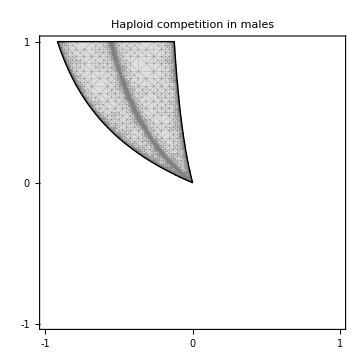

```mathematica
plot2=Show[
bothfixedA,
XpolymorphicA,
bothfixeda,
Xpolymorphica,
YaIntStable,
PlotRange->{{-1,1},{-1,1}},
(*Frame->{True,True,True,True},*)
ImageSize->{xsize,xsize},
PlotRangePadding->0,
FrameTicks->{Table[{x,x,ticksize},{x,{-1,0,1}}],Table[{y,y,ticksize},{y,{-1,0,1}}],None,None},
FrameTicksStyle->{{Directive[Black,Thickness[lwd]],Directive[Black,Thickness[lwd]]},{Directive[Black,Thickness[lwd]],Directive[Black,Thickness[lwd],FontColor->White]}},
FrameStyle->{{Black,Thickness[lwd]},{Black,Thickness[lwd]},{Black,Thickness[lwd]},{Black,Thickness[lwd]}},
(*FrameLabel->{"Relative fitness of aa males",""},*)
BaseStyle->{FontFamily->"Helvetica",FontSize->14},
ImagePadding->Pad,
(*Epilog->{
Text[Style["A",14,Bold],Scaled@{0.05,0.95}],
Text[Style["λ_WA>1",14],{1.29,0.5}],
Text[Style["λ_WA<1 & λ_Wa<1",14],{0.5,0.5}],
Text[Style["Ya equilibrium unstable",14],{0.5,1.25}],
Text[Style["*",18],{1.2,0.85}],
Rotate[Text[Style["Relative fitness of AA males",14],Scaled@ylabpos],90 Degree]
},*)
PlotLabel->Style["Haploid competition in males", 16,Black,Bold],
PlotRangeClipping->False
]

(*Export[plotdir<>"regionplot_2_Female_A.pdf",%];*)
```

#### Parameters - Diploid selection - female drive

```mathematica
someparams={
Subscript[wHap, a,sex_]->1,
Subscript[wHap, A,sex_]->1,
Subscript[α, female]->1/2+αmd,
Subscript[wDip, A,A,sex_]->1+s,
Subscript[wDip, a,A,sex_]->1+h s,Subscript[wDip, A,a,sex_]->1+ h s,
Subscript[wDip, a,a,sex_]->1,
Subscript[α, male]->1/2
};
moreparams={
h->0.75,
recAMnotAX->0
};
```

```mathematica
Simplify[charpolyYaXAar0/.someparams,posassumps];
intYaXAar0=λ/.Solve[%==0,λ]//Flatten;
```

```mathematica
bothfixedA=
RegionPlot[
(Max[Abs[λ/.YaXAEigs/.someparams/.moreparams//Flatten]]<1)&&(*internally stable*)
(λWA>1/.eqr0YaXA/.someparams/.moreparams),
{αmd,-1/2,1/2},{s,-1,1},
PlotStyle->{Gray,Opacity[0.25]},
BoundaryStyle->None,
MaxRecursion->10
];

bothfixeda=
RegionPlot[
(Max[Abs[λ/.YaXAEigs/.someparams/.moreparams//Flatten]]<1)&&(*internally stable*)
(λWa>1/.eqr0YaXA/.someparams/.moreparams),
{αmd,-1/2,1/2},{s,-1,1},
PlotStyle->{Gray,Opacity[0.25]},
BoundaryStyle->None,
MaxRecursion->10
];

XpolymorphicA=
RegionPlot[
0<(pXf/.eqr0YaXAa/.someparams/.moreparams)<1&&0<(pXm/.eqr0YaXAa/.someparams/.moreparams)<1&&(*biologically valid*)(Max[Abs[intYaXAar0/.moreparams]]<1)&&(*internally stable*)
(λWA>1/.eqr0YaXAa/.someparams/.moreparams),
{αmd,-1/2,1/2},{s,-1,1},
PlotStyle->{Gray,Opacity[0.25]},
BoundaryStyle->None,
MaxRecursion->10
];

Xpolymorphica=
RegionPlot[
0<(pXf/.eqr0YaXAa/.someparams/.moreparams)<1&&0<(pXm/.eqr0YaXAa/.someparams/.moreparams)<1&&(*biologically valid*)(Max[Abs[intYaXAar0/.moreparams]]<1)&&(*internally stable*)
(λWa>1/.eqr0YaXAa/.someparams/.moreparams),
{αmd,-1/2,1/2},{s,-1,1},
PlotStyle->{Gray,Opacity[0.25]},
BoundaryStyle->None,
MaxRecursion->10
];
```

```mathematica
YaIntStable=RegionPlot[
(0<(pXf/.eqr0YaXAa/.someparams/.moreparams)<1&&0<(pXm/.eqr0YaXAa/.someparams/.moreparams)<1&&(*biologically valid*)Max[Abs[intYaXAar0/.moreparams]]<1)||(*internally stable*)
(Max[Abs[λ/.YaXAEigs/.someparams/.moreparams//Flatten]]<1),
{αmd,-1/2,1/2},{s,-1,1},
PlotStyle->None,
BoundaryStyle->{Black,Thick},
MaxRecursion->10
];
```

#### Plot

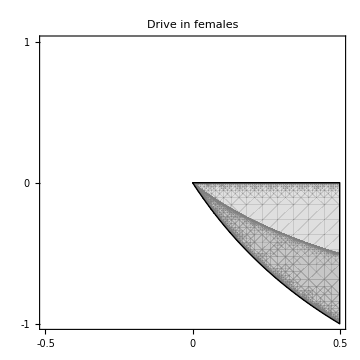

```mathematica
plot3=Show[
bothfixedA,
XpolymorphicA,
bothfixeda,
Xpolymorphica,
YaIntStable,
PlotRange->{{-1/2,1/2},{-1,1}},
(*Frame->{True,True,True,True},*)
ImageSize->{xsize,xsize},
PlotRangePadding->0,
FrameTicks->{Table[{x,x,ticksize},{x,{-0.5,0,0.5}}],Table[{y,y,ticksize},{y,{-1,0,1}}],None,None},
FrameTicksStyle->{{Directive[Black,Thickness[lwd]],Directive[Black,Thickness[lwd]]},{Directive[Black,Thickness[lwd]],Directive[Black,Thickness[lwd],FontColor->White]}},
FrameStyle->{{Black,Thickness[lwd]},{Black,Thickness[lwd]},{Black,Thickness[lwd]},{Black,Thickness[lwd]}},
(*FrameLabel->{"Relative fitness of aa males",""},*)
BaseStyle->{FontFamily->"Helvetica",FontSize->14},
ImagePadding->Pad,
(*Epilog->{
Text[Style["A",14,Bold],Scaled@{0.05,0.95}],
Text[Style["λ_WA>1",14],{1.29,0.5}],
Text[Style["λ_WA<1 & λ_Wa<1",14],{0.5,0.5}],
Text[Style["Ya equilibrium unstable",14],{0.5,1.25}],
Text[Style["*",18],{1.2,0.85}],
Rotate[Text[Style["Relative fitness of AA males",14],Scaled@ylabpos],90 Degree]
},*)
PlotLabel->Style["Drive in females", 16,Black,Bold],
PlotRangeClipping->False
]

(*Export[plotdir<>"regionplot_2_Female_A.pdf",%];*)
```

#### Parameters - Diploid selection - female haploid competition

```mathematica
someparams={
Subscript[wHap, a,sex_]->1,
Subscript[wHap, A,male]->1,
Subscript[wHap, A,female]->1+t,
Subscript[α, female]->1/2,
Subscript[wDip, A,A,sex_]->1+s,
Subscript[wDip, a,A,sex_]->1+h s,Subscript[wDip, A,a,sex_]->1+ h s,
Subscript[wDip, a,a,sex_]->1,
Subscript[α, male]->1/2
};
moreparams={
h->0.75,
recAMnotAX->0
};
```

```mathematica
Simplify[charpolyYaXAar0/.someparams,posassumps];
intYaXAar0=λ/.Solve[%==0,λ]//Flatten;
```

```mathematica
bothfixedA=
RegionPlot[
(Max[Abs[λ/.YaXAEigs/.someparams/.moreparams//Flatten]]<1)&&(*internally stable*)
(λWA>1/.eqr0YaXA/.someparams/.moreparams),
{t,-1,1},{s,-1,1},
PlotStyle->{Gray,Opacity[0.25]},
BoundaryStyle->None,
MaxRecursion->10
];

bothfixeda=
RegionPlot[
(Max[Abs[λ/.YaXAEigs/.someparams/.moreparams//Flatten]]<1)&&(*internally stable*)
(λWa>1/.eqr0YaXA/.someparams/.moreparams),
{t,-1,1},{s,-1,1},
PlotStyle->{Gray,Opacity[0.25]},
BoundaryStyle->None,
MaxRecursion->10
];

XpolymorphicA=
RegionPlot[
0<(pXf/.eqr0YaXAa/.someparams/.moreparams)<1&&0<(pXm/.eqr0YaXAa/.someparams/.moreparams)<1&&(*biologically valid*)(Max[Abs[intYaXAar0/.moreparams]]<1)&&(*internally stable*)
(λWA>1/.eqr0YaXAa/.someparams/.moreparams),
{t,-1,1},{s,-1,1},
PlotStyle->{Gray,Opacity[0.25]},
BoundaryStyle->None,
MaxRecursion->10
];

Xpolymorphica=
RegionPlot[
0<(pXf/.eqr0YaXAa/.someparams/.moreparams)<1&&0<(pXm/.eqr0YaXAa/.someparams/.moreparams)<1&&(*biologically valid*)(Max[Abs[intYaXAar0/.moreparams]]<1)&&(*internally stable*)
(λWa>1/.eqr0YaXAa/.someparams/.moreparams),
{t,-1,1},{s,-1,1},
PlotStyle->{Gray,Opacity[0.25]},
BoundaryStyle->None,
MaxRecursion->10
];
```

```mathematica
YaIntStable=RegionPlot[
(0<(pXf/.eqr0YaXAa/.someparams/.moreparams)<1&&0<(pXm/.eqr0YaXAa/.someparams/.moreparams)<1&&(*biologically valid*)Max[Abs[intYaXAar0/.moreparams]]<1)||(*internally stable*)
(Max[Abs[λ/.YaXAEigs/.someparams/.moreparams//Flatten]]<1),
{t,-1,1},{s,-1,1},
PlotStyle->None,
BoundaryStyle->{Black,Thick},
MaxRecursion->10
];
```

#### Plot

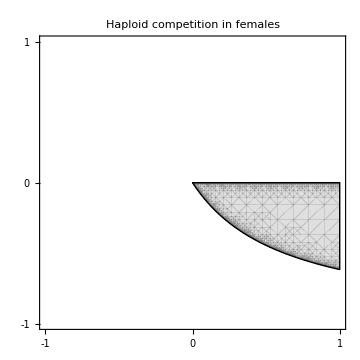

```mathematica
plot4=Show[
bothfixedA,
XpolymorphicA,
bothfixeda,
Xpolymorphica,
YaIntStable,
PlotRange->{{-1,1},{-1,1}},
(*Frame->{True,True,True,True},*)
ImageSize->{xsize,xsize},
PlotRangePadding->0,
FrameTicks->{Table[{x,x,ticksize},{x,{-1,0,1}}],Table[{y,y,ticksize},{y,{-1,0,1}}],None,None},
FrameTicksStyle->{{Directive[Black,Thickness[lwd]],Directive[Black,Thickness[lwd]]},{Directive[Black,Thickness[lwd]],Directive[Black,Thickness[lwd],FontColor->White]}},
FrameStyle->{{Black,Thickness[lwd]},{Black,Thickness[lwd]},{Black,Thickness[lwd]},{Black,Thickness[lwd]}},
(*FrameLabel->{"Relative fitness of aa males",""},*)
BaseStyle->{FontFamily->"Helvetica",FontSize->14},
ImagePadding->Pad,
(*Epilog->{
Text[Style["A",14,Bold],Scaled@{0.05,0.95}],
Text[Style["λ_WA>1",14],{1.29,0.5}],
Text[Style["λ_WA<1 & λ_Wa<1",14],{0.5,0.5}],
Text[Style["Ya equilibrium unstable",14],{0.5,1.25}],
Text[Style["*",18],{1.2,0.85}],
Rotate[Text[Style["Relative fitness of AA males",14],Scaled@ylabpos],90 Degree]
},*)
PlotLabel->Style["Haploid competition in females", 16,Black,Bold],
PlotRangeClipping->False
]

(*Export[plotdir<>"regionplot_2_Female_A.pdf",%];*)
```

#### Rename

```mathematica
plot1ploidantag=plot1;
(*plot2ploidantag=plot2;*)
plot3ploidantag=plot3;
(*plot4ploidantag=plot4;*)
```

# Temporal:

## Recursions (written as in appendix, generic loci order) [ENTER]

### Haploid selection

We start with haploid selection, which occurs in sperm/pollen only. We assume male sperm/pollen compete for eggs, and that the allele at the autosomal locus determines their competitive ability (with relative fitnesses wA and wa). After selection on male gametes/pollen the frequencies of gametes in each sex are

```mathematica
(*mean fitness of female gametes*)
wbarHapFemale=(wAf XAMf+waf XaMf+wAf XAmf+waf Xamf)+(wAf YAMf+waf YaMf+wAf YAmf+waf Yamf);

(*non-mutant eggs*)
XAMfs=wAf XAMf/wbarHapFemale;
XaMfs=waf XaMf/wbarHapFemale;
YAMfs=wAf YAMf/wbarHapFemale;
YaMfs=waf YaMf/wbarHapFemale;

(*mutant eggs*)
XAmfs=wAf XAmf/wbarHapFemale;
Xamfs=waf Xamf/wbarHapFemale;
YAmfs=wAf YAmf/wbarHapFemale;
Yamfs=waf Yamf/wbarHapFemale;

(*mean fitness of male gametes*)
wbarHapMale=(wAm XAMm+wam XaMm+wAm XAmm+wam Xamm)+(wAm YAMm+wam YaMm+wAm YAmm+wam Yamm);

(*non-mutant male gametes*)
XAMms=wAm XAMm/wbarHapMale;
XaMms=wam XaMm/wbarHapMale;
YAMms= wAm YAMm/wbarHapMale;
YaMms= wam YaMm/wbarHapMale;

(*mutant male gametes*)
XAmms=wAm XAmm/wbarHapMale;
Xamms=wam Xamm/wbarHapMale;
YAmms= wAm YAmm/wbarHapMale;
Yamms= wam Yamm/wbarHapMale;
```

Check that frequencies sum to one in each sex after haploid selection:

```mathematica
1==XAMms+XaMms+YAMms+YaMms+XAmms+Xamms+YAmms+Yamms//Factor (*male gametes*)
1==XAMfs+XaMfs+XAmfs+Xamfs+YAMfs+YaMfs+YAmfs+Yamfs//Factor (*eggs*)
```

True

True

### Random mating

After random mating, the frequencies of the diploid genotypes are

```mathematica
(*MM Homozygotes*)
(*XM-XM females*)
XAMXAMfemale=kXX (XAMfs XAMms);
XAMXaMfemale=kXX(XAMfs XaMms+XaMfs XAMms );
XaMXaMfemale=kXX(XaMfs XaMms);
(*XM-XM males*)
XAMXAMmale=(1-kXX)(XAMfs XAMms);
XAMXaMmale=(1-kXX)(XAMfs XaMms+XaMfs XAMms );
XaMXaMmale=(1-kXX)(XaMfs XaMms);

(*XM-YM females*)
XAMYAMfemale=kXY(XAMfs YAMms+YAMfs XAMms);
XAMYaMfemale=kXY(XAMfs YaMms+YaMfs XAMms);
XaMYAMfemale=kXY(XaMfs YAMms+YAMfs XaMms);
XaMYaMfemale=kXY(XaMfs YaMms+YaMfs XaMms);
(*XM-YM males*)
XAMYAMmale=(1-kXY)(XAMfs YAMms+YAMfs XAMms);
XAMYaMmale=(1-kXY)(XAMfs YaMms+YaMfs XAMms);
XaMYAMmale=(1-kXY)(XaMfs YAMms+YAMfs XaMms);
XaMYaMmale=(1-kXY)(XaMfs YaMms+YaMfs XaMms);

(*YM-YM females*)
YAMYAMfemale=kYY(YAMfs YAMms);
YAMYaMfemale=kYY(YAMfs YaMms+YaMfs YAMms);
YaMYaMfemale=kYY(YaMfs YaMms);
(*YM-YM males*)
YAMYAMmale=(1-kYY)(YAMfs YAMms);
YAMYaMmale=(1-kYY)(YAMfs YaMms+YaMfs YAMms);
YaMYaMmale=(1-kYY)(YaMfs YaMms);

(*Mm heterozygotes*)
(*XM-Xm females*)
XAmXAMfemale=kMmXX (XAmfs XAMms+XAMfs XAmms);
XAmXaMfemale=kMmXX(XAmfs XaMms+XaMfs XAmms );
XAMXamfemale=kMmXX(XAMfs Xamms+Xamfs XAMms);
XamXaMfemale=kMmXX(Xamfs XaMms+XaMfs Xamms);
(*XM-Xm males*)
XAmXAMmale=(1-kMmXX) (XAmfs XAMms+XAMfs XAmms);
XAmXaMmale=(1-kMmXX)(XAmfs XaMms+XaMfs XAmms );
XAMXammale=(1-kMmXX)(XAMfs Xamms+Xamfs XAMms);
XamXaMmale=(1-kMmXX)(Xamfs XaMms+XaMfs Xamms);

(*Xm-YM females*)
XAmYAMfemale=kMmXY(XAmfs YAMms+YAMfs XAmms);
XAmYaMfemale=kMmXY(XAmfs YaMms+YaMfs XAmms);
XamYAMfemale=kMmXY(Xamfs YAMms+YAMfs Xamms);
XamYaMfemale=kMmXY(Xamfs YaMms+YaMfs Xamms);
(*Xm-YM males*)
XAmYAMmale=(1-kMmXY)(XAmfs YAMms+YAMfs XAmms);
XAmYaMmale=(1-kMmXY)(XAmfs YaMms+YaMfs XAmms);
XamYAMmale=(1-kMmXY)(Xamfs YAMms+YAMfs Xamms);
XamYaMmale=(1-kMmXY)(Xamfs YaMms+YaMfs Xamms);

(*XM-Ym females*)
XAMYAmfemale=kMmXY(XAMfs YAmms+YAmfs XAMms);
XAMYamfemale=kMmXY(XAMfs Yamms+Yamfs XAMms );
XaMYAmfemale=kMmXY(XaMfs YAmms+YAmfs XaMms );
XaMYamfemale=kMmXY(XaMfs Yamms+Yamfs XaMms);
(*XM-Ym females*)
XAMYAmmale=(1-kMmXY)(XAMfs YAmms+YAmfs XAMms);
XAMYammale=(1-kMmXY)(XAMfs Yamms+Yamfs XAMms );
XaMYAmmale=(1-kMmXY)(XaMfs YAmms+YAmfs XaMms );
XaMYammale=(1-kMmXY)(XaMfs Yamms+Yamfs XaMms);

(*Ym-YM females*)
YAmYAMfemale=kMmYY(YAmfs YAMms+YAMfs YAmms);
YAmYaMfemale=kMmYY(YAmfs YaMms+YaMfs YAmms);
YamYAMfemale=kMmYY(Yamfs YAMms+YAMfs Yamms);
YamYaMfemale=kMmYY(Yamfs YaMms+YaMfs Yamms);
(*Ym-YM males*)
YAmYAMmale=(1-kMmYY)(YAmfs YAMms+YAMfs YAmms);
YAmYaMmale=(1-kMmYY)(YAmfs YaMms+YaMfs YAmms);
YamYAMmale=(1-kMmYY)(Yamfs YAMms+YAMfs Yamms);
YamYaMmale=(1-kMmYY)(Yamfs YaMms+YaMfs Yamms);

(*mm heterozygotes*)
(*Xm-Xm females*)
XAmXAmfemale=kmm(XAmfs XAmms);
XAmXamfemale=kmm(XAmfs Xamms+Xamfs XAmms );
XamXamfemale=kmm(Xamfs Xamms);
(*Xm-Xm males*)
XAmXAmmale=(1-kmm)(XAmfs XAmms);
XAmXammale=(1-kmm)(XAmfs Xamms+Xamfs XAmms );
XamXammale=(1-kmm)(Xamfs Xamms);

(*Xm-Ym females*)
XAmYAmfemale=kmm(XAmfs YAmms+YAmfs XAmms );
XAmYamfemale=kmm(XAmfs Yamms+Yamfs XAmms );
XamYAmfemale=kmm(Xamfs YAmms+YAmfs Xamms );
XamYamfemale=kmm(Xamfs Yamms+Yamfs Xamms);
(*Xm-Ym males*)
XAmYAmmale=(1-kmm)(XAmfs YAmms+YAmfs XAmms );
XAmYammale=(1-kmm)(XAmfs Yamms+Yamfs XAmms );
XamYAmmale=(1-kmm)(Xamfs YAmms+YAmfs Xamms );
XamYammale=(1-kmm)(Xamfs Yamms+Yamfs Xamms);

(*Ym-Ym females*)
YAmYAmfemale=kmm(YAmfs YAmms);
YAmYamfemale=kmm(YAmfs Yamms+Yamfs YAmms);
YamYamfemale=kmm(Yamfs Yamms);
(*Ym-Ym males*)
YAmYAmmale=(1-kmm)(YAmfs YAmms);
YAmYammale=(1-kmm)(YAmfs Yamms+Yamfs YAmms);
YamYammale=(1-kmm)(Yamfs Yamms);
```

Check that they sum to one

```mathematica
1==XAMXAMfemale+XAMXaMfemale+XaMXaMfemale+
XAMXAMmale+XAMXaMmale+XaMXaMmale+
XAMYAMmale+XAMYaMmale+XaMYAMmale+XaMYaMmale+
XAMYAMfemale+XAMYaMfemale+XaMYAMfemale+XaMYaMfemale+
YAMYAMmale+YAMYaMmale+YaMYaMmale+
YAMYAMfemale+YAMYaMfemale+YaMYaMfemale+
XAmXAMfemale+XAmXaMfemale+XAMXamfemale+XamXaMfemale+
XAmXAMmale+XAmXaMmale+XAMXammale+XamXaMmale+
XAmYAMfemale+XAmYaMfemale+XamYAMfemale+XamYaMfemale+
XAmYAMmale+XAmYaMmale+XamYAMmale+XamYaMmale+
XAMYAmfemale+XAMYamfemale+XaMYAmfemale+XaMYamfemale+
XAMYAmmale+XAMYammale+XaMYAmmale+XaMYammale+
YAmYAMfemale+YAmYaMfemale+YamYAMfemale+YamYaMfemale+
YAmYAMmale+YAmYaMmale+YamYAMmale+YamYaMmale+
XAmXAmfemale+XAmXamfemale+XamXamfemale+
XAmXAmmale+XAmXammale+XamXammale+
XAmYAmfemale+XAmYamfemale+XamYAmfemale+XamYamfemale+
XAmYAmmale+XAmYammale+XamYAmmale+XamYammale+
YAmYAmfemale+YAmYamfemale+YamYamfemale+
YAmYAmmale+YAmYammale+YamYammale//Factor
```

True

### Diploid selection

We next model selection in diploids, which can differ among the sexes. Let FAA, FAa, and Faa be the relative fitnesses of females homozygous for allele A, heterozygous, or homozygous for allele a at the autosomal locus. Similarly we use MAA, MAa, and Maa in males. Frequencies after selection in diploid are indicated by appending an s to the name.

```mathematica
(*mean male fitness*)
wbarM=
MAA XAMXAMmale+MAa XAMXaMmale+Maa XaMXaMmale+
MAA XAMYAMmale+MAa (XAMYaMmale+XaMYAMmale)+Maa XaMYaMmale+
MAA YAMYAMmale+MAa YAMYaMmale+Maa YaMYaMmale+
MAA XAmXAMmale+MAa (XAmXaMmale+XAMXammale)+Maa XamXaMmale+
MAA XAmYAMmale+MAa (XAmYaMmale+XamYAMmale)+Maa XamYaMmale+
MAA XAMYAmmale+MAa(XAMYammale+XaMYAmmale)+Maa XaMYammale+
MAA YAmYAMmale+MAa (YAmYaMmale+YamYAMmale)+Maa YamYaMmale+
MAA XAmXAmmale+MAa XAmXammale+Maa XamXammale+
MAA XAmYAmmale+MAa (XAmYammale+XamYAmmale)+Maa XamYammale+
MAA YAmYAmmale+MAa YAmYammale+Maa YamYammale;

XAMXAMmales=MAA XAMXAMmale/wbarM;
XAMXaMmales=MAa XAMXaMmale/wbarM;
XaMXaMmales=Maa XaMXaMmale/wbarM;

XAMYAMmales=MAA XAMYAMmale/wbarM;
XAMYaMmales=MAa XAMYaMmale/wbarM;
XaMYAMmales=MAa XaMYAMmale/wbarM;
XaMYaMmales=Maa XaMYaMmale/wbarM;

YAMYAMmales=MAA YAMYAMmale/wbarM;
YAMYaMmales=MAa YAMYaMmale/wbarM;
YaMYaMmales=Maa YaMYaMmale/wbarM;

XAmXAMmales=MAA XAmXAMmale/wbarM;
XAmXaMmales=MAa XAmXaMmale/wbarM;
XAMXammales=MAa XAMXammale/wbarM;
XamXaMmales=Maa XamXaMmale/wbarM;

XAmYAMmales=MAA XAmYAMmale/wbarM;
XAmYaMmales=MAa XAmYaMmale/wbarM;
XamYAMmales=MAa XamYAMmale/wbarM;
XamYaMmales=Maa XamYaMmale/wbarM;

XAMYAmmales=MAA XAMYAmmale/wbarM;
XAMYammales=MAa XAMYammale/wbarM;
XaMYAmmales=MAa XaMYAmmale/wbarM;
XaMYammales=Maa XaMYammale/wbarM;

YAmYAMmales=MAA YAmYAMmale/wbarM;
YAmYaMmales=MAa YAmYaMmale/wbarM;
YamYAMmales=MAa YamYAMmale/wbarM;
YamYaMmales=Maa YamYaMmale/wbarM;

XAmXAmmales=MAA XAmXAmmale/wbarM;
XAmXammales=MAa XAmXammale/wbarM;
XamXammales=Maa XamXammale/wbarM;

XAmYAmmales=MAA XAmYAmmale/wbarM;
XAmYammales=MAa XAmYammale/wbarM;
XamYAmmales=MAa XamYAmmale/wbarM;
XamYammales=Maa XamYammale/wbarM;

YAmYAmmales=MAA YAmYAmmale/wbarM;
YAmYammales=MAa YAmYammale/wbarM;
YamYammales=Maa YamYammale/wbarM;
```

Frequency of males after diplod selection should sum to 1

```mathematica
1==XAMXAMmales+XAMXaMmales+XaMXaMmales+
XAMYAMmales+XAMYaMmales+XaMYAMmales+XaMYaMmales+
YAMYAMmales+YAMYaMmales+YaMYaMmales+
XAmXAMmales+XAmXaMmales+XAMXammales+XamXaMmales+
XAmYAMmales+XAmYaMmales+XamYAMmales+XamYaMmales+
XAMYAmmales+XAMYammales+XaMYAmmales+XaMYammales+
YAmYAMmales+YAmYaMmales+YamYAMmales+YamYaMmales+
XAmXAmmales+XAmXammales+XamXammales+
XAmYAmmales+XAmYammales+XamYAmmales+XamYammales+
YAmYAmmales+YAmYammales+YamYammales//Factor
```

True

```mathematica
(*mean female fitness*)
wbarF=FAA XAMXAMfemale+FAa XAMXaMfemale+Faa XaMXaMfemale+
FAA XAMYAMfemale+FAa (XAMYaMfemale+XaMYAMfemale)+Faa XaMYaMfemale+
FAA YAMYAMfemale+FAa YAMYaMfemale+Faa YaMYaMfemale+
FAA XAmXAMfemale+FAa XAmXaMfemale+FAa XAMXamfemale+Faa XamXaMfemale+
FAA XAmYAMfemale+FAa XAmYaMfemale+FAa XamYAMfemale+Faa XamYaMfemale+
FAA XAMYAmfemale+FAa XAMYamfemale+FAa XaMYAmfemale+Faa XaMYamfemale+
FAA YAmYAMfemale+FAa YAmYaMfemale+FAa YamYAMfemale+Faa YamYaMfemale+
FAA XAmXAmfemale+FAa XAmXamfemale+Faa XamXamfemale+
FAA XAmYAmfemale+FAa XAmYamfemale+FAa XamYAmfemale+Faa XamYamfemale+
FAA YAmYAmfemale+FAa YAmYamfemale+Faa YamYamfemale;

XAMXAMfemales=FAA XAMXAMfemale/wbarF;
XAMXaMfemales=FAa XAMXaMfemale/wbarF;
XaMXaMfemales=Faa XaMXaMfemale/wbarF;

XAMYAMfemales=FAA XAMYAMfemale/wbarF;
XAMYaMfemales=FAa XAMYaMfemale/wbarF;
XaMYAMfemales=FAa XaMYAMfemale/wbarF;
XaMYaMfemales=Faa XaMYaMfemale/wbarF;

YAMYAMfemales=FAA YAMYAMfemale/wbarF;
YAMYaMfemales=FAa YAMYaMfemale/wbarF;
YaMYaMfemales=Faa YaMYaMfemale/wbarF;

XAmXAMfemales=FAA XAmXAMfemale/wbarF;
XAmXaMfemales=FAa XAmXaMfemale/wbarF;
XAMXamfemales=FAa XAMXamfemale/wbarF;
XamXaMfemales=Faa XamXaMfemale/wbarF;

XAmYAMfemales=FAA XAmYAMfemale/wbarF;
XAmYaMfemales=FAa XAmYaMfemale/wbarF;
XamYAMfemales=FAa XamYAMfemale/wbarF;
XamYaMfemales=Faa XamYaMfemale/wbarF;

XAMYAmfemales=FAA XAMYAmfemale/wbarF;
XAMYamfemales=FAa XAMYamfemale/wbarF;
XaMYAmfemales=FAa XaMYAmfemale/wbarF;
XaMYamfemales=Faa XaMYamfemale/wbarF;

YAmYAMfemales=FAA YAmYAMfemale/wbarF;
YAmYaMfemales=FAa YAmYaMfemale/wbarF;
YamYAMfemales=FAa YamYAMfemale/wbarF;
YamYaMfemales=Faa YamYaMfemale/wbarF;

XAmXAmfemales=FAA XAmXAmfemale/wbarF;
XAmXamfemales=FAa XAmXamfemale/wbarF;
XamXamfemales=Faa XamXamfemale/wbarF;

XAmYAmfemales=FAA XAmYAmfemale/wbarF;
XAmYamfemales=FAa XAmYamfemale/wbarF;
XamYAmfemales=FAa XamYAmfemale/wbarF;
XamYamfemales=Faa XamYamfemale/wbarF;

YAmYAmfemales=FAA YAmYAmfemale/wbarF;
YAmYamfemales=FAa YAmYamfemale/wbarF;
YamYamfemales=Faa YamYamfemale/wbarF;
```

Frequency of females after diplod selection should sum to 1

```mathematica
1==XAMXAMfemales+XAMXaMfemales+XaMXaMfemales+
XAMYAMfemales+XAMYaMfemales+XaMYAMfemales+XaMYaMfemales+
YAMYAMfemales+YAMYaMfemales+YaMYaMfemales+
XAmXAMfemales+XAmXaMfemales+XAMXamfemales+XamXaMfemales+
XAmYAMfemales+XAmYaMfemales+XamYAMfemales+XamYaMfemales+
XAMYAmfemales+XAMYamfemales+XaMYAmfemales+XaMYamfemales+
YAmYAMfemales+YAmYaMfemales+YamYAMfemales+YamYaMfemales+
XAmXAmfemales+XAmXamfemales+XamXamfemales+
XAmYAmfemales+XAmYamfemales+XamYAmfemales+XamYamfemales+
YAmYAmfemales+YAmYamfemales+YamYamfemales//Factor
```

True

### Meiosis

Translate into new notation:

first two letters refer to SDR locus genotype, then numbers ij giving A and M locus genotype where 
1-AM
2-aM
3-Am
4-am
then m or f indicating male or female
then s to indicate that these are frequencies after selection
e.g., xy41ms is a male with genotype X-a-m Y-A-M. 
Where i and j are interchangable (in YY and XX individuals) the lowest number is given first.

```mathematica
xx11ms=XAMXAMmales;
xx12ms=XAMXaMmales;
xx22ms=XaMXaMmales;

xx13ms=XAmXAMmales;
xx23ms=XAmXaMmales;
xx14ms=XAMXammales;
xx24ms=XamXaMmales;

xx33ms=XAmXAmmales;
xx34ms=XAmXammales;
xx44ms=XamXammales;

xy11ms=XAMYAMmales;
xy12ms=XAMYaMmales;
xy21ms=XaMYAMmales;
xy22ms=XaMYaMmales;

xy31ms=XAmYAMmales;
xy32ms=XAmYaMmales;
xy41ms=XamYAMmales;
xy42ms=XamYaMmales;

xy13ms=XAMYAmmales;
xy14ms=XAMYammales;
xy23ms=XaMYAmmales;
xy24ms=XaMYammales;

xy33ms=XAmYAmmales;
xy34ms=XAmYammales;
xy43ms=XamYAmmales;
xy44ms=XamYammales;

yy11ms=YAMYAMmales;
yy12ms=YAMYaMmales;
yy22ms=YaMYaMmales;

yy13ms=YAmYAMmales;
yy23ms=YAmYaMmales;
yy14ms=YamYAMmales;
yy24ms=YamYaMmales;

yy33ms=YAmYAmmales;
yy34ms=YAmYammales;
yy44ms=YamYammales;
```

```mathematica
xx11fs=XAMXAMfemales;
xx12fs=XAMXaMfemales;
xx22fs=XaMXaMfemales;

xx13fs=XAmXAMfemales;
xx23fs=XAmXaMfemales;
xx14fs=XAMXamfemales;
xx24fs=XamXaMfemales;

xx33fs=XAmXAmfemales;
xx34fs=XAmXamfemales;
xx44fs=XamXamfemales;

xy11fs=XAMYAMfemales;
xy12fs=XAMYaMfemales;
xy21fs=XaMYAMfemales;
xy22fs=XaMYaMfemales;

xy31fs=XAmYAMfemales;
xy32fs=XAmYaMfemales;
xy41fs=XamYAMfemales;
xy42fs=XamYaMfemales;

xy13fs=XAMYAmfemales;
xy14fs=XAMYamfemales;
xy23fs=XaMYAmfemales;
xy24fs=XaMYamfemales;

xy33fs=XAmYAmfemales;
xy34fs=XAmYamfemales;
xy43fs=XamYAmfemales;
xy44fs=XamYamfemales;

yy11fs=YAMYAMfemales;
yy12fs=YAMYaMfemales;
yy22fs=YaMYaMfemales;

yy13fs=YAmYAMfemales;
yy23fs=YAmYaMfemales;
yy14fs=YamYAMfemales;
yy24fs=YamYaMfemales;

yy33fs=YAmYAmfemales;
yy34fs=YAmYamfemales;
yy44fs=YamYamfemales;
```

First, we consider female gametes

```mathematica
(*X bearing ovules*)
nextXAMf=xx11fs+xx13fs/2+(xx12fs+xx14fs*(1-Rf)+xx23fs*Rf)αf+
xy11fs/2+(xy12fs(1-rMMf)+xy21fs (rMMf))αf+
(xy13fs(1-χf)+xy31fs (χf))/2+
xy14fs *αf+
(xy14fs (-(Rf+rMmf+χf))+ 
xy41fs(rMmf+χf-Rf)+
xy23fs(Rf+rMmf-χf)+
xy32fs(Rf+χf-rMmf))αf/2;

nextXaMf=xx22fs+xx24fs/2+(xx12fs+xx23fs*(1-Rf)+xx14fs*Rf)(1-αf)+
xy22fs/2+(xy12fs(rMMf)+xy21fs(1-rMMf))(1-αf)+
(xy24fs (1-χf)+xy42fs (χf))/2+
xy23fs*(1-αf)+
(xy14fs(Rf+rMmf-χf)+
xy41fs(Rf+χf-rMmf)+
xy23fs(-(Rf+rMmf+χf))+
xy32fs (rMmf+χf-Rf))(1-αf)/2;

nextXAmf=xx33fs+xx13fs/2+(xx23fs*(1-Rf)+Rf*xx14fs+xx34fs)αf+
xy33fs/2+(xy34fs(1-rmmf)+xy43fs(rmmf))αf+
(xy13fs(χf)+xy31fs(1-χf))/2+
xy32fs *αf+
(xy14fs(Rf+χf-rMmf)+
xy41fs(Rf+rMmf-χf)+
xy23fs(rMmf+χf-Rf)+
xy32fs (-(Rf+rMmf+χf)))αf/2;

nextXamf=xx44fs+xx24fs/2+(xx14fs*(1-Rf)+xx23fs*Rf+xx34fs)(1-αf)+
xy44fs/2+(xy34fs(rmmf)+xy43fs(1-rmmf))(1-αf)+
(xy24fs(χf)+xy42fs(1-χf))/2+
xy41fs*(1-αf)+
(xy14fs(rMmf+χf-Rf)+
xy41fs(-(Rf+rMmf+χf))+
xy23fs(Rf+χf-rMmf)+
xy32fs(Rf+rMmf-χf))(1-αf)/2;

(*Y bearing ovules*)
nextYAMf=yy11fs+yy13fs/2+(yy12fs+yy14fs*(1-Rf)+yy23fs*Rf)αf+
xy11fs/2+(xy12fs(rMMf)+xy21fs (1-rMMf))(αf)+
(xy13fs(χf)+xy31fs (1-χf))/2+
xy41fs*αf+
(xy14fs (rMmf+χf-Rf)+
 xy41fs(-(Rf+rMmf+χf))+
xy23fs(Rf+χf-rMmf)+
xy32fs(Rf+rMmf-χf))αf/2;

nextYaMf =yy22fs+yy24fs/2+(yy12fs+yy23fs*(1-Rf)+yy14fs*Rf)(1-αf)+
xy22fs/2+(xy12fs(1-rMMf)+xy21fs(rMMf))(1-αf)+
(xy24fs (χf)+xy42fs (1-χf))/2+
xy32fs*(1-αf)+
(xy14fs(Rf+χf-rMmf)+
xy41fs(Rf+rMmf-χf)+
xy23fs(rMmf+χf-Rf)+
xy32fs (-(Rf+rMmf+χf)))(1-αf)/2;

nextYAmf =yy33fs+yy13fs/2+(yy23fs*(1-Rf)+Rf*yy14fs+yy34fs)αf+
xy33fs/2+(xy34fs(rmmf)+xy43fs(1-rmmf))(αf)+
(xy13fs(1-χf)+xy31fs(χf))/2+
xy23fs*αf+
(xy14fs(Rf+rMmf-χf)+
xy41fs(Rf+χf-rMmf)+
xy23fs(-(Rf+rMmf+χf))+
xy32fs (rMmf+χf-Rf))αf/2;

nextYamf=yy44fs+yy24fs/2+(yy14fs*(1-Rf)+yy23fs*Rf+yy34fs)(1-αf)+
xy44fs/2+(xy34fs(1-rmmf)+xy43fs(rmmf))(1-αf)+
(xy24fs(1-χf)+xy42fs(χf))/2+
xy14fs*(1-αf)+
(xy14fs(-(Rf+rMmf+χf))+
xy41fs(rMmf+χf-Rf)+
xy23fs(Rf+rMmf-χf)+
xy32fs(Rf+χf-rMmf))(1-αf)/2;
```

```mathematica
Factor[nextXAMf+nextXaMf+nextXAmf+nextXamf+nextYAMf+nextYaMf+nextYAmf+nextYamf]
```

1

We can consider male gametes similarly

```mathematica
(*X bearing pollen*)
nextXAMm=xx11ms+xx13ms/2+(xx12ms+xx14ms*(1-Rm)+xx23ms*Rm)αm+
xy11ms/2+(xy12ms(1-rMMm)+xy21ms (rMMm))αm+
(xy13ms(1-χm)+xy31ms (χm))/2+
xy14ms *αm+
(xy14ms (-(Rm+rMmm+χm))+ 
xy41ms(rMmm+χm-Rm)+
xy23ms(Rm+rMmm-χm)+
xy32ms(Rm+χm-rMmm))αm/2;

nextXaMm =xx22ms+xx24ms/2+(xx12ms+xx23ms*(1-Rm)+xx14ms*Rm)(1-αm)+
xy22ms/2+(xy12ms(rMMm)+xy21ms(1-rMMm))(1-αm)+
(xy24ms (1-χm)+xy42ms (χm))/2+
xy23ms*(1-αm)+
(xy14ms(Rm+rMmm-χm)+
xy41ms(Rm+χm-rMmm)+
xy23ms(-(Rm+rMmm+χm))+
xy32ms (rMmm+χm-Rm))(1-αm)/2;

nextXAmm =xx33ms+xx13ms/2+(xx23ms*(1-Rm)+Rm*xx14ms+xx34ms)αm+
xy33ms/2+(xy34ms(1-rmmm)+xy43ms(rmmm))αm+
(xy13ms(χm)+xy31ms(1-χm))/2+
xy32ms *αm+
(xy14ms(Rm+χm-rMmm)+
xy41ms(Rm+rMmm-χm)+
xy23ms(rMmm+χm-Rm)+
xy32ms (-(Rm+rMmm+χm)))αm/2;

nextXamm=xx44ms+xx24ms/2+(xx14ms*(1-Rm)+xx23ms*Rm+xx34ms)(1-αm)+
xy44ms/2+(xy34ms(rmmm)+xy43ms(1-rmmm))(1-αm)+
(xy24ms(χm)+xy42ms(1-χm))/2+
xy41ms*(1-αm)+
(xy14ms(rMmm+χm-Rm)+
xy41ms(-(Rm+rMmm+χm))+
xy23ms(Rm+χm-rMmm)+
xy32ms(Rm+rMmm-χm))(1-αm)/2;

(*Y bearing pollen*)
nextYAMm=yy11ms+yy13ms/2+(yy12ms+yy14ms*(1-Rm)+yy23ms*Rm)αm+
xy11ms/2+(xy12ms(rMMm)+xy21ms (1-rMMm))(αm)+
(xy13ms(χm)+xy31ms (1-χm))/2+
xy41ms*αm+
(xy14ms (rMmm+χm-Rm)+
 xy41ms(-(Rm+rMmm+χm))+
xy23ms(Rm+χm-rMmm)+
xy32ms(Rm+rMmm-χm))αm/2;

nextYaMm =yy22ms+yy24ms/2+(yy12ms+yy23ms*(1-Rm)+yy14ms*Rm)(1-αm)+
xy22ms/2+(xy12ms(1-rMMm)+xy21ms(rMMm))(1-αm)+
(xy24ms (χm)+xy42ms (1-χm))/2+
xy32ms*(1-αm)+
(xy14ms(Rm+χm-rMmm)+
xy41ms(Rm+rMmm-χm)+
xy23ms(rMmm+χm-Rm)+
xy32ms (-(Rm+rMmm+χm)))(1-αm)/2;

nextYAmm=yy33ms+yy13ms/2+(yy23ms*(1-Rm)+Rm*yy14ms+yy34ms)αm+
xy33ms/2+(xy34ms(rmmm)+xy43ms(1-rmmm))(αm)+
(xy13ms(1-χm)+xy31ms(χm))/2+
xy23ms*αm+
(xy14ms(Rm+rMmm-χm)+
xy41ms(Rm+χm-rMmm)+
xy23ms(-(Rm+rMmm+χm))+
xy32ms (rMmm+χm-Rm))αm/2;

nextYamm=yy44ms+yy24ms/2+(yy14ms*(1-Rm)+yy23ms*Rm+yy34ms)(1-αm)+
xy44ms/2+(xy34ms(1-rmmm)+xy43ms(rmmm))(1-αm)+
(xy24ms(1-χm)+xy42ms(χm))/2+
xy14ms*(1-αm)+
(xy14ms(-(Rm+rMmm+χm))+
xy41ms(rMmm+χm-Rm)+
xy23ms(Rm+rMmm-χm)+
xy32ms(Rm+χm-rMmm))(1-αm)/2;
```

```mathematica
Factor[nextXAMm+nextXaMm+nextXAmm+nextXamm+nextYAMm+nextYaMm+nextYAmm+nextYamm]
```

1

Generally want to at least assume that recombination is not affected by M or sex

```mathematica
SUBSR={
Rm->R,
Rf->R,
rMMm->r,
rMmm->r,
rmmm->r,
rMMf->r,
rMmf->r,
rmmf->r,
χm->χ,
χf->χ
};
```

Often also want to assume the following about k:

```mathematica
SUBS={
Rm->R,
Rf->R,
rMMm->r,
rMmm->r,
rmmm->r,
rMMf->r,
rMmf->r,
rmmf->r,
χm->χ,
χf->χ,
kXX->1,
kXY->0,
kYY->0,
kMmXX->k,
kMmXY->k,
kMmYY->k,
kmm->k,
kmm->k,
kmm->k
};
```

## Simulation Recursions [ENTER]

#### Equilibrium [ENTER]

Working in allele frequencies rather than haplotype frequencies:

```mathematica
subequil={
XAMf->pXf,
XaMf->(1-pXf),
YAMf->0,
YaMf->0,
XAMm->pXm(1-freqYm),
XaMm->(1-pXm)(1-freqYm),
YAMm->pYm*freqYm,
YaMm->(1-pYm)*freqYm,
XAmf->0,
Xamf->0,
XAmm->0,
Xamm->0,
YAmm->0,
Yamm->0,
YAmf->0,
Yamf->0
};
```

```mathematica
equilA0={pXf->(waf (Faa Maa waf wam-FAa wAf αf (Maa wam+2 MAa wAm αm)))/(Faa Maa waf^2 wam+wAf (2 FAA MAa wAf wAm αm-FAa waf (Maa wam+2 MAa wAm αm))),pXm->-(2 MAa αm (-Faa Maa waf wam+FAa wAf αf (Maa wam+2 MAa wAm αm)))/(2 Maa MAa (Faa waf wam+FAA wAf wAm) αm+FAa (Maa wam+2 MAa wAm αm) (Maa waf (-1+αf)-2 MAa wAf αf αm)),pYm->0,freqYm->(FAa (Maa waf (-1+αf)+2 MAa wAf αf (-1+αm)) (Maa wam+2 MAa wAm αm)+2 Maa MAa (-Faa waf wam (-1+αm)+FAA wAf wAm αm))/(2 (FAa (Maa waf (-1+αf)-MAa wAf αf) (Maa wam+2 MAa wAm αm)+Maa MAa (Faa waf wam+2 FAA wAf wAm αm)))};
```

```mathematica
equilAp0={pXf->(waf (FAa wAf αf (MAA wAm-2 MAa wam (-1+αm))+2 Faa MAa waf wam (-1+αm)))/(wAf (-FAA MAA wAf wAm+FAa waf (MAA wAm-2 MAa wam (-1+αm)))+2 Faa MAa waf^2 wam (-1+αm)),pXm->(MAA (FAa wAf αf (MAA wAm-2 MAa wam (-1+αm))+2 Faa MAa waf wam (-1+αm)))/(-FAa (-MAA wAm+2 MAa wam (-1+αm)) (MAA wAf αf+2 MAa waf (-1+αf) (-1+αm))+2 MAa MAA (Faa waf wam+FAA wAf wAm) (-1+αm)),pYm->1,freqYm->(2 Faa MAa MAA waf wam (-1+αm)-2 FAA MAa MAA wAf wAm αm+FAa (-MAA wAm+2 MAa wam (-1+αm)) (-MAA wAf αf+2 MAa waf (-1+αf) αm))/(2 (FAa (MAa waf (-1+αf)-MAA wAf αf) (-MAA wAm+2 MAa wam (-1+αm))+MAa MAA (-FAA wAf wAm+2 Faa waf wam (-1+αm))))};
```

```mathematica
equilB0={pXf->1,pXm->1,pYm->0,freqYm->1-αm};
```

```mathematica
equilBp0={pXf->0,pXm->0,pYm->1,freqYm->αm};
```

```mathematica
equilC0={pXf->(waf (Maa wam-2 MAa wAm αm))/(Maa waf wam+MAA wAf wAm+2 MAa (-wAf wam+wAf wam αm-waf wAm αm)),pXm->(wam (Maa wam-2 MAa wAm αm) (-Faa waf (MAA wAm+2 MAa wam (-1+αm))+FAa (Maa waf wam (-1+αf)+MAA wAf wAm αf+2 MAa (wAf wam αf (-1+αm)-waf wAm (-1+αf) αm))))/(-(Faa waf wam+FAA wAf wAm) (MAA wAm+2 MAa wam (-1+αm)) (Maa wam-2 MAa wAm αm)+FAa (Maa waf wam (-1+αf)+MAA wAf wAm αf+2 MAa (wAf wam αf (-1+αm)-waf wAm (-1+αf) αm)) (Maa wam^2-wAm (MAA wAm+2 MAa wam (-1+2 αm)))),pYm->(wam (-Faa Maa waf wam (MAA wAm+2 MAa wam (-1+αm))+2 FAA MAa wAf wAm αm (Maa wam-2 MAa wAm αm)+FAa (Maa wam+2 MAa wAm αm) (Maa waf wam (-1+αf)+MAA wAf wAm αf+2 MAa (wAf wam αf (-1+αm)-waf wAm (-1+αf) αm))))/(-Faa waf wam (MAA wAm+2 MAa wam (-1+αm)) (Maa wam+2 MAa wAm (-1+αm))+FAA wAf wAm (MAA wAm-2 MAa wam αm) (-Maa wam+2 MAa wAm αm)+FAa (Maa wam^2-wAm (MAA wAm+MAa wam (2-4 αm))) (Maa waf wam (-1+αf)+MAA wAf wAm αf+2 MAa (wAf wam αf (-1+αm)-waf wAm (-1+αf) αm))),freqYm->(Faa waf wam (MAA wAm+2 MAa wam (-1+αm)) (Maa wam+2 MAa wAm (-1+αm))+FAA wAf wAm (MAA wAm-2 MAa wam αm) (Maa wam-2 MAa wAm αm)-FAa (Maa wam^2-wAm (MAA wAm+MAa wam (2-4 αm))) (Maa waf wam (-1+αf)+MAA wAf wAm αf+2 MAa (wAf wam αf (-1+αm)-waf wAm (-1+αf) αm)))/(2 (Faa waf wam (Maa wam-MAa wAm) (MAA wAm+2 MAa wam (-1+αm))+FAA wAf wAm (MAa wam-MAA wAm) (-Maa wam+2 MAa wAm αm)-FAa (Maa wam^2-MAA wAm^2) (Maa waf wam (-1+αf)+MAA wAf wAm αf+2 MAa (wAf wam αf (-1+αm)-waf wAm (-1+αf) αm))))};
```

Factor[differenceEqs /. r -> 0 /. {equilA0, equilAp0, equilB0, equilBp0, equilC0}]

{{0, 0, 0, 0}, {0, 0, 0, 0}, {0, 0, 0, 0}, {0, 0, 0, 0}, {0, 0, 0, 0}}

To be relevant, this last equilibrium equilC0 requires that the numerators of the frequency of A and a in females are both positive or both negative (they share the same denominator, which is the sum of the numerators):

```mathematica
{pXf,1-pXf}/.equilC0//Factor
```

{(waf (Maa wam-2 MAa wAm αm))/(Maa waf wam-2 MAa wAf wam+MAA wAf wAm+2 MAa wAf wam αm-2 MAa waf wAm αm),(wAf (-2 MAa wam+MAA wAm+2 MAa wam αm))/(Maa waf wam-2 MAa wAf wam+MAA wAf wAm+2 MAa wAf wam αm-2 MAa waf wAm αm)}

Hence, either 2(1-αm) MAa wam > MAA wAm and 2 αm MAa wAm > Maa wam (akin to heterozygous advantage without pollen selection) or 2(1-αm) MAa wam < MAA wAm and 2 αm MAa wAm < Maa wam (akin to heterozygous disadvantage) otherwise pXf won’t lie between 0 and 1.

equilC0 will be shown later to not be internally stable when it exists, so this equilibrium can be ignored when examining the evolution of recombination.

The next order terms in the recombination rate, r (used in the weak selection approximations to assess the effect of r):

```mathematica
equilA1={pXfsm->(2 MAa r waf wAf wam wAm (Faa waf (FAA wAf+FAa waf (-1+αf))-FAa FAA wAf^2 αf) αm ((FAa (Maa waf (-1+αf)+2 MAa wAf αf (-1+αm)) (Maa wam+2 MAa wAm αm)+2 Maa MAa (-Faa waf wam (-1+αm)+FAA wAf wAm αm))/(2 FAA MAa wAf wAm αm+FAa waf (-1+αf) (Maa wam+2 MAa wAm αm))+(wAm (Maa MAA+4 MAa^2 (-1+αm) αm) (-Faa Maa waf wam+FAa wAf αf (Maa wam+2 MAa wAm αm)))/(-Faa Maa waf wam (MAA wAm+2 MAa wam (-1+αm))+2 FAA MAa wAf wAm αm (Maa wam-2 MAa wAm αm)+FAa (Maa wam+2 MAa wAm αm) (Maa waf wam (-1+αf)+MAA wAf wAm αf+2 MAa (wAf wam αf (-1+αm)-waf wAm (-1+αf) αm)))))/(Faa Maa waf^2 wam+wAf (2 FAA MAa wAf wAm αm-FAa waf (Maa wam+2 MAa wAm αm)))^2,pXmsm->(2 FAa MAa r αm (-Faa Maa^2 waf^2 wam^2 (-1+αf)+wAf αf (4 FAA MAa^2 wAf wAm^2 αm^2+FAa waf (-1+αf) (Maa wam+2 MAa wAm αm)^2)) ((FAa (Maa waf (-1+αf)+2 MAa wAf αf (-1+αm)) (Maa wam+2 MAa wAm αm)+2 Maa MAa (-Faa waf wam (-1+αm)+FAA wAf wAm αm))/(2 FAA MAa wAf wAm αm+FAa waf (-1+αf) (Maa wam+2 MAa wAm αm))+(wAm (Maa MAA+4 MAa^2 (-1+αm) αm) (-Faa Maa waf wam+FAa wAf αf (Maa wam+2 MAa wAm αm)))/(-Faa Maa waf wam (MAA wAm+2 MAa wam (-1+αm))+2 FAA MAa wAf wAm αm (Maa wam-2 MAa wAm αm)+FAa (Maa wam+2 MAa wAm αm) (Maa waf wam (-1+αf)+MAA wAf wAm αf+2 MAa (wAf wam αf (-1+αm)-waf wAm (-1+αf) αm)))))/(2 Maa MAa (Faa waf wam+FAA wAf wAm) αm+FAa (Maa wam+2 MAa wAm αm) (Maa waf (-1+αf)-2 MAa wAf αf αm))^2,pYmsm->(2 MAa r wam αm (-Faa Maa waf wam+FAa wAf αf (Maa wam+2 MAa wAm αm)))/(Faa Maa waf wam (MAA wAm+2 MAa wam (-1+αm))+2 FAA MAa wAf wAm αm (-Maa wam+2 MAa wAm αm)-FAa (Maa wam+2 MAa wAm αm) (Maa waf wam (-1+αf)+MAA wAf wAm αf+2 MAa (wAf wam αf (-1+αm)-waf wAm (-1+αf) αm))),freqYmsm->(MAa r (-1+2 αm) (-(Maa MAa wam wAm (Faa waf (FAA wAf+FAa waf (-1+αf))-FAa FAA wAf^2 αf) αm (FAa (Maa waf (-1+αf)+2 MAa wAf αf (-1+αm)) (Maa wam+2 MAa wAm αm)+2 Maa MAa (-Faa waf wam (-1+αm)+FAA wAf wAm αm)))/(2 FAA MAa wAf wAm αm+FAa waf (-1+αf) (Maa wam+2 MAa wAm αm))+(Faa Maa waf wam-FAa wAf αf (Maa wam+2 MAa wAm αm)) (FAa (Maa waf (-1+αf)-MAa wAf αf) (Maa wam+2 MAa wAm αm)+Maa MAa (Faa waf wam+2 FAA wAf wAm αm))+(MAa wam wAm αm (Faa Maa waf wam-FAa wAf αf (Maa wam+2 MAa wAm αm)) (-Maa wAm (Faa waf (FAA wAf+FAa waf (-1+αf))-FAa FAA wAf^2 αf) (Maa MAA+4 MAa^2 (-1+αm) αm)-1/wam(FAa^2 (Maa waf^2 (-1+αf)^2+wAf αf (-2 MAa waf (-1+αf)+MAA wAf αf)) (Maa wam+2 MAa wAm αm)^2+2 FAa (Maa wam+2 MAa wAm αm) (Faa Maa waf wam (MAa waf (-1+αf)-MAA wAf αf)-2 FAA MAa wAf wAm (MAa wAf αf+Maa (waf-waf αf)) αm)+Maa (Faa^2 Maa MAA waf^2 wam^2+4 Faa FAA MAa^2 waf wAf wam wAm αm+4 FAA^2 MAa^2 wAf^2 wAm^2 αm^2))))/(Faa Maa waf wam (MAA wAm+2 MAa wam (-1+αm))+2 FAA MAa wAf wAm αm (-Maa wam+2 MAa wAm αm)-FAa (Maa wam+2 MAa wAm αm) (Maa waf wam (-1+αf)+MAA wAf wAm αf+2 MAa (wAf wam αf (-1+αm)-waf wAm (-1+αf) αm)))))/(FAa (Maa waf (-1+αf)-MAa wAf αf) (Maa wam+2 MAa wAm αm)+Maa MAa (Faa waf wam+2 FAA wAf wAm αm))^2};
```

```mathematica
equilAp1={pXfsm->(2 MAa r waf wAf wam wAm (Faa waf (FAA wAf+FAa waf (-1+αf))-FAa FAA wAf^2 αf) (FAa^2 (-1+αf) αf (MAA wAm-2 MAa wam (-1+αm))^2-2 Faa FAA MAa MAA wam wAm (-1+αm)) (FAa (-MAA wAm+2 MAa wam (-1+αm)) (MAA wAf αf+2 MAa waf (-1+αf) (-1+αm))-2 MAa MAA (Faa waf wam+FAA wAf wAm) (-1+αm)) (-1+αm) (-2 MAa (FAA MAA wAf wAm+FAa waf (-1+αf) (MAA wAm-2 MAa wam (-1+αm)))^2 αm (2 Faa MAa waf wam (MAA wAm+2 MAa wam (-1+αm)) (-1+αm)+FAA MAA wAf wAm (Maa wam-2 MAa wAm αm)-FAa (-MAA wAm+2 MAa wam (-1+αm)) (Maa waf wam (-1+αf)+MAA wAf wAm αf+2 MAa (wAf wam αf (-1+αm)-waf wAm (-1+αf) αm)))+((-FAA MAA wAf wAm+FAa waf (-1+αf) (-MAA wAm+2 MAa wam (-1+αm))) (FAa (MAa waf (-1+αf)-MAA wAf αf) (-MAA wAm+2 MAa wam (-1+αm))+MAa MAA (-FAA wAf wAm+2 Faa waf wam (-1+αm))) (FAa wAf αf (MAA wAm-2 MAa wam (-1+αm))+2 Faa MAa waf wam (-1+αm)) (-FAa (-MAA wAm+2 MAa wam (-1+αm)) (2 Maa MAA waf wam (-1+αf)+MAA^2 wAf wAm αf+4 MAa^2 waf wam (-1+αf) (-1+αm) αm+2 MAa MAA (wAf wam αf (-1+αm)-waf wAm (-1+αf) αm))+2 MAA (Faa MAa waf wam (MAA wAm+2 MAa wam (-1+αm)) (-1+αm)+FAA wAf wAm (Maa MAA wam+MAa (-MAA wAm+2 MAa wam (-1+αm)) αm))))/(-FAa (MAa waf (-1+αf)-MAA wAf αf) (-MAA wAm+2 MAa wam (-1+αm))+MAa MAA (FAA wAf wAm-2 Faa waf wam (-1+αm)))))/((-FAA MAA wAf wAm+FAa waf (-1+αf) (-MAA wAm+2 MAa wam (-1+αm))) (FAa wAf αf (-MAA wAm+2 MAa wam (-1+αm))-2 Faa MAa waf wam (-1+αm)) (wAf (-FAA MAA wAf wAm+FAa waf (MAA wAm-2 MAa wam (-1+αm)))+2 Faa MAa waf^2 wam (-1+αm))^2 (-FAa^2 (-1+αf) αf (MAA wAm-2 MAa wam (-1+αm))^2+2 Faa FAA MAa MAA wam wAm (-1+αm)) (-FAa (-MAA wAm+2 MAa wam (-1+αm)) (MAA wAf αf+2 MAa waf (-1+αf) (-1+αm))+2 MAa MAA (Faa waf wam+FAA wAf wAm) (-1+αm)) (2 Faa MAa waf wam (MAA wAm+2 MAa wam (-1+αm)) (-1+αm)+FAA MAA wAf wAm (Maa wam-2 MAa wAm αm)-FAa (-MAA wAm+2 MAa wam (-1+αm)) (Maa waf wam (-1+αf)+MAA wAf wAm αf+2 MAa (wAf wam αf (-1+αm)-waf wAm (-1+αf) αm)))),pXmsm->(2 FAa MAa r (FAa^2 (-1+αf) αf (MAA wAm-2 MAa wam (-1+αm))^2-2 Faa FAA MAa MAA wam wAm (-1+αm)) (wAf αf (FAA MAA^2 wAf wAm^2+FAa waf (-1+αf) (MAA wAm-2 MAa wam (-1+αm))^2)-4 Faa MAa^2 waf^2 wam^2 (-1+αf) (-1+αm)^2) (-1+αm) (-2 MAa (FAA MAA wAf wAm+FAa waf (-1+αf) (MAA wAm-2 MAa wam (-1+αm)))^2 αm (2 Faa MAa waf wam (MAA wAm+2 MAa wam (-1+αm)) (-1+αm)+FAA MAA wAf wAm (Maa wam-2 MAa wAm αm)-FAa (-MAA wAm+2 MAa wam (-1+αm)) (Maa waf wam (-1+αf)+MAA wAf wAm αf+2 MAa (wAf wam αf (-1+αm)-waf wAm (-1+αf) αm)))+((-FAA MAA wAf wAm+FAa waf (-1+αf) (-MAA wAm+2 MAa wam (-1+αm))) (FAa (MAa waf (-1+αf)-MAA wAf αf) (-MAA wAm+2 MAa wam (-1+αm))+MAa MAA (-FAA wAf wAm+2 Faa waf wam (-1+αm))) (FAa wAf αf (MAA wAm-2 MAa wam (-1+αm))+2 Faa MAa waf wam (-1+αm)) (-FAa (-MAA wAm+2 MAa wam (-1+αm)) (2 Maa MAA waf wam (-1+αf)+MAA^2 wAf wAm αf+4 MAa^2 waf wam (-1+αf) (-1+αm) αm+2 MAa MAA (wAf wam αf (-1+αm)-waf wAm (-1+αf) αm))+2 MAA (Faa MAa waf wam (MAA wAm+2 MAa wam (-1+αm)) (-1+αm)+FAA wAf wAm (Maa MAA wam+MAa (-MAA wAm+2 MAa wam (-1+αm)) αm))))/(-FAa (MAa waf (-1+αf)-MAA wAf αf) (-MAA wAm+2 MAa wam (-1+αm))+MAa MAA (FAA wAf wAm-2 Faa waf wam (-1+αm)))))/((-FAA MAA wAf wAm+FAa waf (-1+αf) (-MAA wAm+2 MAa wam (-1+αm))) (FAa wAf αf (-MAA wAm+2 MAa wam (-1+αm))-2 Faa MAa waf wam (-1+αm)) (-FAa^2 (-1+αf) αf (MAA wAm-2 MAa wam (-1+αm))^2+2 Faa FAA MAa MAA wam wAm (-1+αm)) (FAa (-MAA wAm+2 MAa wam (-1+αm)) (MAA wAf αf+2 MAa waf (-1+αf) (-1+αm))-2 MAa MAA (Faa waf wam+FAA wAf wAm) (-1+αm)) (-FAa (-MAA wAm+2 MAa wam (-1+αm)) (MAA wAf αf+2 MAa waf (-1+αf) (-1+αm))+2 MAa MAA (Faa waf wam+FAA wAf wAm) (-1+αm)) (2 Faa MAa waf wam (MAA wAm+2 MAa wam (-1+αm)) (-1+αm)+FAA MAA wAf wAm (Maa wam-2 MAa wAm αm)-FAa (-MAA wAm+2 MAa wam (-1+αm)) (Maa waf wam (-1+αf)+MAA wAf wAm αf+2 MAa (wAf wam αf (-1+αm)-waf wAm (-1+αf) αm)))),pYmsm->-(2 MAa r wAm (-FAA MAA wAf wAm+FAa waf (-1+αf) (-MAA wAm+2 MAa wam (-1+αm))) (-1+αm))/(-2 Faa MAa waf wam (MAA wAm+2 MAa wam (-1+αm)) (-1+αm)+FAA MAA wAf wAm (-Maa wam+2 MAa wAm αm)+FAa (-MAA wAm+2 MAa wam (-1+αm)) (Maa waf wam (-1+αf)+MAA wAf wAm αf+2 MAa (wAf wam αf (-1+αm)-waf wAm (-1+αf) αm))),freqYmsm->(MAa r ((FAA MAA wAf wAm+FAa waf (-1+αf) (MAA wAm-2 MAa wam (-1+αm))) (FAa (MAa waf (-1+αf)-MAA wAf αf) (-MAA wAm+2 MAa wam (-1+αm))+MAa MAA (-FAA wAf wAm+2 Faa waf wam (-1+αm))) αm+((-FAA MAA wAf wAm+FAa waf (-1+αf) (-MAA wAm+2 MAa wam (-1+αm))) (FAA MAA wAf wAm (-Maa wam+MAa wAm)+FAa (Maa waf wam (-1+αf)+MAA wAf wAm αf-MAa (waf wAm (-1+αf)+wAf wam αf)) (-MAA wAm+2 MAa wam (-1+αm))+2 Faa MAa waf wam (MAa wam-MAA wAm) (-1+αm)) (-1+αm) (2 Faa MAa MAA waf wam (-1+αm)-2 FAA MAa MAA wAf wAm αm+FAa (-MAA wAm+2 MAa wam (-1+αm)) (-MAA wAf αf+2 MAa waf (-1+αf) αm)))/(2 Faa MAa waf wam (MAA wAm+2 MAa wam (-1+αm)) (-1+αm)+FAA MAA wAf wAm (Maa wam-2 MAa wAm αm)-FAa (-MAA wAm+2 MAa wam (-1+αm)) (Maa waf wam (-1+αf)+MAA wAf wAm αf+2 MAa (wAf wam αf (-1+αm)-waf wAm (-1+αf) αm)))-(MAa MAA wam wAm (Faa waf (FAA wAf+FAa waf (-1+αf))-FAa FAA wAf^2 αf) (FAa^2 (-1+αf) αf (MAA wAm-2 MAa wam (-1+αm))^2-2 Faa FAA MAa MAA wam wAm (-1+αm)) (FAa (-MAA wAm+2 MAa wam (-1+αm)) (MAA wAf αf+2 MAa waf (-1+αf) (-1+αm))-2 MAa MAA (Faa waf wam+FAA wAf wAm) (-1+αm)) (-1+αm) (-1+2 αm) (-2 MAa (FAA MAA wAf wAm+FAa waf (-1+αf) (MAA wAm-2 MAa wam (-1+αm)))^2 αm (2 Faa MAa waf wam (MAA wAm+2 MAa wam (-1+αm)) (-1+αm)+FAA MAA wAf wAm (Maa wam-2 MAa wAm αm)-FAa (-MAA wAm+2 MAa wam (-1+αm)) (Maa waf wam (-1+αf)+MAA wAf wAm αf+2 MAa (wAf wam αf (-1+αm)-waf wAm (-1+αf) αm)))+((-FAA MAA wAf wAm+FAa waf (-1+αf) (-MAA wAm+2 MAa wam (-1+αm))) (FAa (MAa waf (-1+αf)-MAA wAf αf) (-MAA wAm+2 MAa wam (-1+αm))+MAa MAA (-FAA wAf wAm+2 Faa waf wam (-1+αm))) (FAa wAf αf (MAA wAm-2 MAa wam (-1+αm))+2 Faa MAa waf wam (-1+αm)) (-FAa (-MAA wAm+2 MAa wam (-1+αm)) (2 Maa MAA waf wam (-1+αf)+MAA^2 wAf wAm αf+4 MAa^2 waf wam (-1+αf) (-1+αm) αm+2 MAa MAA (wAf wam αf (-1+αm)-waf wAm (-1+αf) αm))+2 MAA (Faa MAa waf wam (MAA wAm+2 MAa wam (-1+αm)) (-1+αm)+FAA wAf wAm (Maa MAA wam+MAa (-MAA wAm+2 MAa wam (-1+αm)) αm))))/(-FAa (MAa waf (-1+αf)-MAA wAf αf) (-MAA wAm+2 MAa wam (-1+αm))+MAa MAA (FAA wAf wAm-2 Faa waf wam (-1+αm)))))/((-FAA MAA wAf wAm+FAa waf (-1+αf) (-MAA wAm+2 MAa wam (-1+αm))) (FAa wAf αf (-MAA wAm+2 MAa wam (-1+αm))-2 Faa MAa waf wam (-1+αm)) (-FAa^2 (-1+αf) αf (MAA wAm-2 MAa wam (-1+αm))^2+2 Faa FAA MAa MAA wam wAm (-1+αm)) (-FAa (-MAA wAm+2 MAa wam (-1+αm)) (MAA wAf αf+2 MAa waf (-1+αf) (-1+αm))+2 MAa MAA (Faa waf wam+FAA wAf wAm) (-1+αm)) (2 Faa MAa waf wam (MAA wAm+2 MAa wam (-1+αm)) (-1+αm)+FAA MAA wAf wAm (Maa wam-2 MAa wAm αm)-FAa (-MAA wAm+2 MAa wam (-1+αm)) (Maa waf wam (-1+αf)+MAA wAf wAm αf+2 MAa (wAf wam αf (-1+αm)-waf wAm (-1+αf) αm))))))/(FAa (MAa waf (-1+αf)-MAA wAf αf) (-MAA wAm+2 MAa wam (-1+αm))+MAa MAA (-FAA wAf wAm+2 Faa waf wam (-1+αm)))^2};
```

```mathematica
equilB1={pXfsm->-(2 FAa MAa r wAf wam (-1+αf) (-1+αm))/(2 FAA MAa wAf wAm αm+FAa waf (-1+αf) (Maa wam+2 MAa wAm αm)),pXmsm->(2 MAa r wAm (FAA wAf+FAa waf (-1+αf)) (-1+αm))/(2 FAA MAa wAf wAm αm+FAa waf (-1+αf) (Maa wam+2 MAa wAm αm)),pYmsm->-(2 MAa r wam αm)/(MAA wAm+2 MAa wam (-1+αm)),freqYmsm->r (-1+2 αm-(MAA wAm αm (-1+2 αm))/(MAA wAm+2 MAa wam (-1+αm))+(FAa Maa waf wam (-1+αf) (-1+αm) (-1+2 αm))/(2 FAA MAa wAf wAm αm+FAa waf (-1+αf) (Maa wam+2 MAa wAm αm)))};
```

```mathematica
equilBp1={pXfsm->-(2 FAa MAa r waf wAm αf αm)/(FAa wAf αf (MAA wAm-2 MAa wam (-1+αm))+2 Faa MAa waf wam (-1+αm)),pXmsm->-(2 MAa r wam (Faa waf-FAa wAf αf) αm)/(FAa wAf αf (MAA wAm-2 MAa wam (-1+αm))+2 Faa MAa waf wam (-1+αm)),pYmsm->(2 MAa r wAm (-1+αm))/(-Maa wam+2 MAa wAm αm),freqYmsm->r αm (-1+2 αm) ((FAa MAA wAf wAm αf)/(FAa wAf αf (MAA wAm-2 MAa wam (-1+αm))+2 Faa MAa waf wam (-1+αm))+(-Maa wam+2 MAa wAm)/(Maa wam-2 MAa wAm αm))};
```

#### Definitions [ENTER]

```mathematica
Clear[numequil];
numequil[FAA_,FAa_,Faa_,MAA_,MAa_,Maa_,wAf_,waf_,wAm_,wam_,αf_,αm_,r_]:=numequil[FAA,FAa,Faa,MAA,MAa,Maa,wAf,waf,wAm,wam,αf,αm,r]=
{pXf,pXm,pYm,freqYm}/.NSolve[{(Faa pXf (-1+pXf+pXm-pXf pXm) waf wam-FAA (-1+pXf) pXf pXm wAf wAm+FAa (-pXm waf wAm+pXf ((-1+pXm) wAf wam+pXm waf wAm)) (pXf-αf))/(Faa (-1+pXf) (-1+pXm) waf wam+FAA pXf pXm wAf wAm+FAa (pXm waf wAm-pXf ((-1+pXm) wAf wam+pXm waf wAm)))==0,(2 (-1+freqYm) Maa (-1+pXf) pXm (-1+pYm) waf wam+MAA pXf (1+2 (-1+freqYm) pXm) pYm wAf wAm-2 MAa (pYm waf wAm (pXm-freqYm pXm-r αm)+pXf ((-1+freqYm) pXm ((-1+pYm) wAf wam+pYm waf wAm)+((-1+pYm+r-pYm r) wAf wam+pYm r waf wAm) αm)))/(2 (Maa (-1+pXf) (-1+pYm) waf wam+MAA pXf pYm wAf wAm+MAa (pYm waf wAm-pXf ((-1+pYm) wAf wam+pYm waf wAm))))==0,(MAA pXf pYm wAf wAm-2 freqYm pYm (Maa (-1+pXf) (-1+pYm) waf wam+MAA pXf pYm wAf wAm+MAa (pYm waf wAm-pXf ((-1+pYm) wAf wam+pYm waf wAm)))+2 MAa (-pYm (-1+r) waf wAm+pXf (-pYm waf wAm+r (wAf wam-pYm wAf wam+pYm waf wAm))) αm)/(2 (Maa (-1+pXf) (-1+pYm) waf wam+MAA pXf pYm wAf wAm+MAa (pYm waf wAm-pXf ((-1+pYm) wAf wam+pYm waf wAm))))==0,(-(-1+2 freqYm) Maa (-1+pXf) (-1+pYm) waf wam+(1-2 freqYm) MAA pXf pYm wAf wAm+2 MAa (pYm waf wAm (-freqYm+r+αm-2 r αm)+pXf ((-1+pYm) wAf wam (-1+freqYm+r+αm-2 r αm)+pYm waf wAm (freqYm-αm+r (-1+2 αm)))))/(2 (Maa (-1+pXf) (-1+pYm) waf wam+MAA pXf pYm wAf wAm+MAa (pYm waf wAm-pXf ((-1+pYm) wAf wam+pYm waf wAm))))==0},{pXf,pXm,pYm,freqYm}]
```

Eigenvalues of internal stability matrix:

```mathematica
Clear[internstab];
internstab[FAA_,FAa_,Faa_,MAA_,MAa_,Maa_,wAf_,waf_,wAm_,wam_,αf_,αm_,r_,pXf_,pXm_,pYm_,freqYm_]:=internstab[FAA,FAa,Faa,MAA,MAa,Maa,wAf,waf,wAm,wam,αf,αm,r,pXf,pXm,pYm,freqYm]=Eigenvalues[{{-(waf wAf (-Faa FAA pXm wam wAm+Faa FAA pXm^2 wam wAm-FAa FAA pXm^2 wAm^2-Faa FAa wam^2 αf+2 Faa FAa pXm wam^2 αf-Faa FAa pXm^2 wam^2 αf+FAa FAA pXm^2 wAm^2 αf))/(Faa waf wam-Faa pXf waf wam-Faa pXm waf wam+Faa pXf pXm waf wam+FAa pXf wAf wam-FAa pXf pXm wAf wam+FAa pXm waf wAm-FAa pXf pXm waf wAm+FAA pXf pXm wAf wAm)^2,-(wam wAm (-Faa FAA pXf waf wAf+Faa FAA pXf^2 waf wAf-FAa FAA pXf^2 wAf^2-Faa FAa waf^2 αf+2 Faa FAa pXf waf^2 αf-Faa FAa pXf^2 waf^2 αf+FAa FAA pXf^2 wAf^2 αf))/(Faa waf wam-Faa pXf waf wam-Faa pXm waf wam+Faa pXf pXm waf wam+FAa pXf wAf wam-FAa pXf pXm wAf wam+FAa pXm waf wAm-FAa pXf pXm waf wAm+FAA pXf pXm wAf wAm)^2,0,0},{-(waf wAf (-Maa MAA pYm wam wAm+Maa MAA pYm^2 wam wAm-2 MAa MAA pYm^2 wAm^2+2 MAa MAA pYm^2 r wAm^2-2 Maa MAa wam^2 αm+4 Maa MAa pYm wam^2 αm-2 Maa MAa pYm^2 wam^2 αm+2 Maa MAa r wam^2 αm-4 Maa MAa pYm r wam^2 αm+2 Maa MAa pYm^2 r wam^2 αm-4 MAa^2 pYm wam wAm αm+4 MAa^2 pYm^2 wam wAm αm+8 MAa^2 pYm r wam wAm αm-8 MAa^2 pYm^2 r wam wAm αm+2 MAa MAA pYm^2 wAm^2 αm-2 MAa MAA pYm^2 r wAm^2 αm+4 MAa^2 pYm wam wAm αm^2-4 MAa^2 pYm^2 wam wAm αm^2-8 MAa^2 pYm r wam wAm αm^2+8 MAa^2 pYm^2 r wam wAm αm^2))/(Maa waf wam-Maa pXf waf wam-Maa pYm waf wam+Maa pXf pYm waf wam+2 MAa pXf r wAf wam-2 MAa pXf pYm r wAf wam+2 MAa pYm waf wAm-2 MAa pXf pYm waf wAm-2 MAa pYm r waf wAm+2 MAa pXf pYm r waf wAm+MAA pXf pYm wAf wAm+2 MAa pXf wAf wam αm-2 MAa pXf pYm wAf wam αm-4 MAa pXf r wAf wam αm+4 MAa pXf pYm r wAf wam αm-2 MAa pYm waf wAm αm+2 MAa pXf pYm waf wAm αm+4 MAa pYm r waf wAm αm-4 MAa pXf pYm r waf wAm αm)^2,0,(wam wAm (Maa MAA pXf waf wAf-Maa MAA pXf^2 waf wAf+2 MAa MAA pXf^2 r wAf^2+2 Maa MAa r waf^2 αm-4 Maa MAa pXf r waf^2 αm+2 Maa MAa pXf^2 r waf^2 αm-4 MAa^2 pXf waf wAf αm+4 MAa^2 pXf^2 waf wAf αm+8 MAa^2 pXf r waf wAf αm-8 MAa^2 pXf^2 r waf wAf αm-2 MAa MAA pXf^2 r wAf^2 αm+4 MAa^2 pXf waf wAf αm^2-4 MAa^2 pXf^2 waf wAf αm^2-8 MAa^2 pXf r waf wAf αm^2+8 MAa^2 pXf^2 r waf wAf αm^2))/(Maa waf wam-Maa pXf waf wam-Maa pYm waf wam+Maa pXf pYm waf wam+2 MAa pXf r wAf wam-2 MAa pXf pYm r wAf wam+2 MAa pYm waf wAm-2 MAa pXf pYm waf wAm-2 MAa pYm r waf wAm+2 MAa pXf pYm r waf wAm+MAA pXf pYm wAf wAm+2 MAa pXf wAf wam αm-2 MAa pXf pYm wAf wam αm-4 MAa pXf r wAf wam αm+4 MAa pXf pYm r wAf wam αm-2 MAa pYm waf wAm αm+2 MAa pXf pYm waf wAm αm+4 MAa pYm r waf wAm αm-4 MAa pXf pYm r waf wAm αm)^2,0},{(waf wAf (Maa MAA pYm wam wAm-Maa MAA pYm^2 wam wAm+2 MAa MAA pYm^2 r wAm^2+2 Maa MAa r wam^2 αm-4 Maa MAa pYm r wam^2 αm+2 Maa MAa pYm^2 r wam^2 αm-4 MAa^2 pYm wam wAm αm+4 MAa^2 pYm^2 wam wAm αm+8 MAa^2 pYm r wam wAm αm-8 MAa^2 pYm^2 r wam wAm αm-2 MAa MAA pYm^2 r wAm^2 αm+4 MAa^2 pYm wam wAm αm^2-4 MAa^2 pYm^2 wam wAm αm^2-8 MAa^2 pYm r wam wAm αm^2+8 MAa^2 pYm^2 r wam wAm αm^2))/(Maa waf wam-Maa pXf waf wam-Maa pYm waf wam+Maa pXf pYm waf wam+2 MAa pXf wAf wam-2 MAa pXf pYm wAf wam-2 MAa pXf r wAf wam+2 MAa pXf pYm r wAf wam+2 MAa pYm r waf wAm-2 MAa pXf pYm r waf wAm+MAA pXf pYm wAf wAm-2 MAa pXf wAf wam αm+2 MAa pXf pYm wAf wam αm+4 MAa pXf r wAf wam αm-4 MAa pXf pYm r wAf wam αm+2 MAa pYm waf wAm αm-2 MAa pXf pYm waf wAm αm-4 MAa pYm r waf wAm αm+4 MAa pXf pYm r waf wAm αm)^2,0,-(wam wAm (-Maa MAA pXf waf wAf+Maa MAA pXf^2 waf wAf-2 MAa MAA pXf^2 wAf^2+2 MAa MAA pXf^2 r wAf^2-2 Maa MAa waf^2 αm+4 Maa MAa pXf waf^2 αm-2 Maa MAa pXf^2 waf^2 αm+2 Maa MAa r waf^2 αm-4 Maa MAa pXf r waf^2 αm+2 Maa MAa pXf^2 r waf^2 αm-4 MAa^2 pXf waf wAf αm+4 MAa^2 pXf^2 waf wAf αm+8 MAa^2 pXf r waf wAf αm-8 MAa^2 pXf^2 r waf wAf αm+2 MAa MAA pXf^2 wAf^2 αm-2 MAa MAA pXf^2 r wAf^2 αm+4 MAa^2 pXf waf wAf αm^2-4 MAa^2 pXf^2 waf wAf αm^2-8 MAa^2 pXf r waf wAf αm^2+8 MAa^2 pXf^2 r waf wAf αm^2))/(Maa waf wam-Maa pXf waf wam-Maa pYm waf wam+Maa pXf pYm waf wam+2 MAa pXf wAf wam-2 MAa pXf pYm wAf wam-2 MAa pXf r wAf wam+2 MAa pXf pYm r wAf wam+2 MAa pYm r waf wAm-2 MAa pXf pYm r waf wAm+MAA pXf pYm wAf wAm-2 MAa pXf wAf wam αm+2 MAa pXf pYm wAf wam αm+4 MAa pXf r wAf wam αm-4 MAa pXf pYm r wAf wam αm+2 MAa pYm waf wAm αm-2 MAa pXf pYm waf wAm αm-4 MAa pYm r waf wAm αm+4 MAa pXf pYm r waf wAm αm)^2,0},{(MAa (-1+2 r) waf wAf (Maa wam^2-2 Maa pYm wam^2+Maa pYm^2 wam^2+2 MAa pYm wam wAm-2 MAa pYm^2 wam wAm+MAA pYm^2 wAm^2) (-1+2 αm))/(2 (Maa waf wam-Maa pXf waf wam-Maa pYm waf wam+Maa pXf pYm waf wam+MAa pXf wAf wam-MAa pXf pYm wAf wam+MAa pYm waf wAm-MAa pXf pYm waf wAm+MAA pXf pYm wAf wAm)^2),0,-(MAa (-1+2 r) (Maa waf^2-2 Maa pXf waf^2+Maa pXf^2 waf^2+2 MAa pXf waf wAf-2 MAa pXf^2 waf wAf+MAA pXf^2 wAf^2) wam wAm (-1+2 αm))/(2 (Maa waf wam-Maa pXf waf wam-Maa pYm waf wam+Maa pXf pYm waf wam+MAa pXf wAf wam-MAa pXf pYm wAf wam+MAa pYm waf wAm-MAa pXf pYm waf wAm+MAA pXf pYm wAf wAm)^2),0}}]
```

The following uses this cutoff to avoid numerical problems:

```mathematica
cutoff=10^(-12);
```

Restricting answers to cases of polymorphic equilibria that are internally stable

```mathematica
Clear[sieve]
sieve[FAA_,FAa_,Faa_,MAA_,MAa_,Maa_,wAf_,waf_,wAm_,wam_,αf_,αm_,r_]:=sieve[FAA,FAa,Faa,MAA,MAa,Maa,wAf,waf,wAm,wam,αf,αm,r]=Block[{},For[i=1; write={},i≤(max=Length[eq=numequil[FAA,FAa,Faa,MAA,MAa,Maa,wAf,waf,wAm,wam,αf,αm,r]]),i++,
If[Length[test=Cases[eq[[i]],x_/;((-cutoff≤Re[x]≤1+cutoff)&&Abs[Im[x]]<cutoff)]]==4&&(Chop[eq[[i]]]≠{0,0,0,1/2})&&(Chop[eq[[i]]-{1,1,1,1/2}]≠{0,0,0,0})&&
(Max[Abs[internstab[FAA,FAa,Faa,MAA,MAa,Maa,wAf,waf,wAm,wam,αf,αm,r,eq[[i,1]],eq[[i,2]],eq[[i,3]],eq[[i,4]]]]]<1),write=Append[write,eq[[i]]]]];
Sort[write]
]
```

```mathematica
λmA=(pavem wAm/wbarHapMale wAf/wbarHapFemale FAA+2(1-pavem)wam/wbarHapMale wAf/wbarHapFemale FAa αf (1-R))/(meanF freqfemale/(1/2))/.pavem->pYm freqYm+pXm (1-freqYm);
λma=((1-pavem) wam/wbarHapMale waf/wbarHapFemale Faa+2pavem wAm/wbarHapMale waf/wbarHapFemale FAa(1-αf)(1-R))/(meanF freqfemale/(1/2))/.pavem->pYm freqYm+pXm (1-freqYm);
ρmA=(2(1-pavem)wam/wbarHapMale wAf/wbarHapFemale FAa αf R)/(meanF freqfemale/(1/2))/.pavem->pYm freqYm+pXm (1-freqYm);
ρma=(2pavem wAm/wbarHapMale waf/wbarHapFemale FAa(1-αf)R)/(meanF freqfemale/(1/2))/.pavem->pYm freqYm+pXm (1-freqYm);
```

The frequency of diploid females is:

```mathematica
freqfemale=XAMXAMfemale+XAMXaMfemale+XaMXaMfemale+
XAMYAMfemale+(XAMYaMfemale+XaMYAMfemale)+XaMYaMfemale+
YAMYAMfemale+YAMYaMfemale+YaMYaMfemale+
XAmXAMfemale+XAmXaMfemale+XAMXamfemale+XamXaMfemale+
XAmYAMfemale+XAmYaMfemale+XamYAMfemale+XamYaMfemale+
XAMYAmfemale+XAMYamfemale+XaMYAmfemale+XaMYamfemale+
YAmYAMfemale+YAmYaMfemale+YamYAMfemale+YamYaMfemale+
XAmXAmfemale+XAmXamfemale+XamXamfemale+
XAmYAmfemale+XAmYamfemale+XamYAmfemale+XamYamfemale+
YAmYAmfemale+YAmYamfemale+YamYamfemale/.SUBS/.subequil//Factor
```

((-1+freqYm) (-wam+pXm wam-pXm wAm))/(wam-pXm wam+freqYm pXm wam-freqYm pYm wam+pXm wAm-freqYm pXm wAm+freqYm pYm wAm)

The mean fitness of a female can be written as:

```mathematica
meanF=pXf(FAA wAf/wbarHapFemale ((pXm(1-freqYm) wAm/wbarHapMale)/freqfemale)+FAa wAf/wbarHapFemale (((1-pXm)(1-freqYm) wam/wbarHapMale)/freqfemale))+(1-pXf)(FAa waf/wbarHapFemale ((pXm(1-freqYm) wAm/wbarHapMale)/freqfemale)+Faa waf/wbarHapFemale (((1-pXm)(1-freqYm) wam/wbarHapMale)/freqfemale))/.SUBS/.subequil;
```

#### Simulation code [Enter]

Code to convert allele frequencies (from the equilibrium calculations) into haplotype frequencies, as needed for the simulations:
[Assumes that all haplotypes convert from M to m at a small rate, pm.  This will cause imbalanced sex ratios at first, so ignore the first few generations, as it reequilibrates.]

```mathematica
Clear[startgen]
startgen[{pXf_,pXm_,pYm_,freqYm_},pm_]:=startgen[{pXf,pXm,pYm,freqYm},pm]=
{XAMf,XaMf,XAmf,Xamf,YAMf,YaMf, YAmf, Yamf,XAMm,XaMm,XAmm,Xamm,YAMm,YaMm, YAmm, Yamm}/.{XAMf->pXf(1-pm),XaMf->(1-pXf)(1-pm),YAMf->0(1-pm),YaMf->0(1-pm),
XAMm->(1-freqYm) pXm(1-pm),XaMm->(1-freqYm) (1-pXm)(1-pm),YAMm->freqYm pYm(1-pm),YaMm->freqYm (1-pYm)(1-pm),
XAmf->pXf(pm),Xamf->(1-pXf)(pm),YAmf->0(pm),Yamf->0(pm),
XAmm->(1-freqYm) pXm(pm),Xamm->(1-freqYm) (1-pXm)(pm),YAmm->freqYm pYm(pm),Yamm->freqYm (1-pYm)(pm)}
```

Calculates the frequency of the modifier among the gametes (assumes that male and female gametes contribute equally to the next generation, hence the 1/2):

```mathematica
modvec=Flatten[Table[{0,0,1/2,1/2},{i,1,4}]]
```

{0,0,1/2,1/2,0,0,1/2,1/2,0,0,1/2,1/2,0,0,1/2,1/2}

When tracking the spread of the neo-W, we are interested in whether the males maintain the Y or become all  its frequency among female gametes (when fixed)Calculates the frequency of the modifier among the gametes (assumes that male and female gametes contribute equally to the next generation, hence the 1/2):

```mathematica
modvec={0,0,0,0,0,0,0,0,0,0,0,0,1,1,1,1}
```

{0,0,0,0,0,0,0,0,0,0,0,0,1,1,1,1}

```mathematica
Clear[sexratio](*Frac males among zygotes*)
sexratio[{FAA_,FAa_,Faa_,MAA_,MAa_,Maa_,wAf_,waf_,wAm_,wam_,αf_,αm_,r_,R_,χ_,k_},{XAMf_,XaMf_,XAmf_,Xamf_,YAMf_,YaMf_, YAmf_, Yamf_,XAMm_,XaMm_,XAmm_,Xamm_,YAMm_,YaMm_, YAmm_, Yamm_}]:=sexratio[{FAA,FAa,Faa,MAA,MAa,Maa,wAf,waf,wAm,wam,αf,αm,r,R,χ,k},{XAMf,XaMf,XAmf,Xamf,YAMf,YaMf, YAmf, Yamf,XAMm,XaMm,XAmm,Xamm,YAMm,YaMm, YAmm, Yamm}]=
1-(k waf wam Xamf Xamm+k waf wam XaMf Xamm+k wAf wam XAmf Xamm+k wAf wam XAMf Xamm+k waf wam Xamf XaMm+waf wam XaMf XaMm+k wAf wam XAmf XaMm+wAf wam XAMf XaMm+k waf wAm Xamf XAmm+k waf wAm XaMf XAmm+k wAf wAm XAmf XAmm+k wAf wAm XAMf XAmm+k waf wAm Xamf XAMm+waf wAm XaMf XAMm+k wAf wAm XAmf XAMm+wAf wAm XAMf XAMm+k waf wam Xamm Yamf+k waf wam XaMm Yamf+k waf wAm XAmm Yamf+k waf wAm XAMm Yamf+k waf wam Xamm YaMf+k waf wAm XAmm YaMf+k wAf wam Xamm YAmf+k wAf wam XaMm YAmf+k wAf wAm XAmm YAmf+k wAf wAm XAMm YAmf+k wAf wam Xamm YAMf+k wAf wAm XAmm YAMf+k waf wam Xamf Yamm+k waf wam XaMf Yamm+k wAf wam XAmf Yamm+k wAf wam XAMf Yamm+k waf wam Yamf Yamm+k waf wam YaMf Yamm+k wAf wam YAmf Yamm+k wAf wam YAMf Yamm+k waf wam Xamf YaMm+k wAf wam XAmf YaMm+k waf wam Yamf YaMm+k wAf wam YAmf YaMm+k waf wAm Xamf YAmm+k waf wAm XaMf YAmm+k wAf wAm XAmf YAmm+k wAf wAm XAMf YAmm+k waf wAm Yamf YAmm+k waf wAm YaMf YAmm+k wAf wAm YAmf YAmm+k wAf wAm YAMf YAmm+k waf wAm Xamf YAMm+k wAf wAm XAmf YAMm+k waf wAm Yamf YAMm+k wAf wAm YAmf YAMm)/((waf Xamf+waf XaMf+wAf XAmf+wAf XAMf+waf Yamf+waf YaMf+wAf YAmf+wAf YAMf) (wam Xamm+wam XaMm+wAm XAmm+wAm XAMm+wam Yamm+wam YaMm+wAm YAmm+wAm YAMm));
```

```mathematica
Clear[generation];
generation[{FAA_,FAa_,Faa_,MAA_,MAa_,Maa_,wAf_,waf_,wAm_,wam_,αf_,αm_,r_,R_,χ_,k_},{XAMf_,XaMf_,XAmf_,Xamf_,YAMf_,YaMf_, YAmf_, Yamf_,XAMm_,XaMm_,XAmm_,Xamm_,YAMm_,YaMm_, YAmm_, Yamm_}]:=generation[{FAA,FAa,Faa,MAA,MAa,Maa,wAf,waf,wAm,wam,αf,αm,r,R,χ,k},{XAMf,XaMf,XAmf,Xamf,YAMf,YaMf, YAmf, Yamf,XAMm,XaMm,XAmm,Xamm,YAMm,YaMm, YAmm, Yamm}]=
Block[
{Rm=R,
Rf=R,
rMMm=r,
rMmm=r,
rmmm=r,
rMMf=r,
rMmf=r,
rmmf=r,
χm=χ,
χf=χ,
kXX=1,
kXY=0,
kYY=0,
kMmXX=k,
kMmXY=k,
kMmYY=k,
kmm=k
},
wbarHapFemale=(wAf XAMf+waf XaMf+wAf XAmf+waf Xamf)+(wAf YAMf+waf YaMf+wAf YAmf+waf Yamf);
wbarHapMale=(wAm XAMm+wam XaMm+wAm XAmm+wam Xamm)+(wAm YAMm+wam YaMm+wAm YAmm+wam Yamm);
(*non-mutant eggs*)
XAMfs=wAf XAMf/wbarHapFemale;
XaMfs=waf XaMf/wbarHapFemale;
YAMfs=wAf YAMf/wbarHapFemale;
YaMfs=waf YaMf/wbarHapFemale;
(*mutant eggs*)
XAmfs=wAf XAmf/wbarHapFemale;
Xamfs=waf Xamf/wbarHapFemale;
YAmfs=wAf YAmf/wbarHapFemale;
Yamfs=waf Yamf/wbarHapFemale;
(*non-mutant male gametes*)
XAMms=wAm XAMm/wbarHapMale;
XaMms=wam XaMm/wbarHapMale;
YAMms= wAm YAMm/wbarHapMale;
YaMms= wam YaMm/wbarHapMale;
(*mutant male gametes*)
XAmms=wAm XAmm/wbarHapMale;
Xamms=wam Xamm/wbarHapMale;
YAmms= wAm YAmm/wbarHapMale;
Yamms= wam Yamm/wbarHapMale;
(*MM Homozygotes*)
(*XM-XM females*)
XAMXAMfemale=kXX (XAMfs XAMms);
XAMXaMfemale=kXX(XAMfs XaMms+XaMfs XAMms );
XaMXaMfemale=kXX(XaMfs XaMms);
(*XM-XM males*)
XAMXAMmale=(1-kXX)(XAMfs XAMms);
XAMXaMmale=(1-kXX)(XAMfs XaMms+XaMfs XAMms );
XaMXaMmale=(1-kXX)(XaMfs XaMms);
(*XM-YM females*)
XAMYAMfemale=kXY(XAMfs YAMms+YAMfs XAMms);
XAMYaMfemale=kXY(XAMfs YaMms+YaMfs XAMms);
XaMYAMfemale=kXY(XaMfs YAMms+YAMfs XaMms);
XaMYaMfemale=kXY(XaMfs YaMms+YaMfs XaMms);
(*XM-YM males*)
XAMYAMmale=(1-kXY)(XAMfs YAMms+YAMfs XAMms);
XAMYaMmale=(1-kXY)(XAMfs YaMms+YaMfs XAMms);
XaMYAMmale=(1-kXY)(XaMfs YAMms+YAMfs XaMms);
XaMYaMmale=(1-kXY)(XaMfs YaMms+YaMfs XaMms);
(*YM-YM females*)
YAMYAMfemale=kYY(YAMfs YAMms);
YAMYaMfemale=kYY(YAMfs YaMms+YaMfs YAMms);
YaMYaMfemale=kYY(YaMfs YaMms);
(*YM-YM males*)
YAMYAMmale=(1-kYY)(YAMfs YAMms);
YAMYaMmale=(1-kYY)(YAMfs YaMms+YaMfs YAMms);
YaMYaMmale=(1-kYY)(YaMfs YaMms);
(*Mm heterozygotes*)
(*XM-Xm females*)
XAmXAMfemale=kMmXX (XAmfs XAMms+XAMfs XAmms);
XAmXaMfemale=kMmXX(XAmfs XaMms+XaMfs XAmms );
XAMXamfemale=kMmXX(XAMfs Xamms+Xamfs XAMms);
XamXaMfemale=kMmXX(Xamfs XaMms+XaMfs Xamms);
(*XM-Xm males*)
XAmXAMmale=(1-kMmXX) (XAmfs XAMms+XAMfs XAmms);
XAmXaMmale=(1-kMmXX)(XAmfs XaMms+XaMfs XAmms );
XAMXammale=(1-kMmXX)(XAMfs Xamms+Xamfs XAMms);
XamXaMmale=(1-kMmXX)(Xamfs XaMms+XaMfs Xamms);
(*Xm-YM females*)
XAmYAMfemale=kMmXY(XAmfs YAMms+YAMfs XAmms);
XAmYaMfemale=kMmXY(XAmfs YaMms+YaMfs XAmms);
XamYAMfemale=kMmXY(Xamfs YAMms+YAMfs Xamms);
XamYaMfemale=kMmXY(Xamfs YaMms+YaMfs Xamms);
(*Xm-YM males*)
XAmYAMmale=(1-kMmXY)(XAmfs YAMms+YAMfs XAmms);
XAmYaMmale=(1-kMmXY)(XAmfs YaMms+YaMfs XAmms);
XamYAMmale=(1-kMmXY)(Xamfs YAMms+YAMfs Xamms);
XamYaMmale=(1-kMmXY)(Xamfs YaMms+YaMfs Xamms);
(*XM-Ym females*)
XAMYAmfemale=kMmXY(XAMfs YAmms+YAmfs XAMms);
XAMYamfemale=kMmXY(XAMfs Yamms+Yamfs XAMms );
XaMYAmfemale=kMmXY(XaMfs YAmms+YAmfs XaMms );
XaMYamfemale=kMmXY(XaMfs Yamms+Yamfs XaMms);
(*XM-Ym females*)
XAMYAmmale=(1-kMmXY)(XAMfs YAmms+YAmfs XAMms);
XAMYammale=(1-kMmXY)(XAMfs Yamms+Yamfs XAMms );
XaMYAmmale=(1-kMmXY)(XaMfs YAmms+YAmfs XaMms );
XaMYammale=(1-kMmXY)(XaMfs Yamms+Yamfs XaMms);
(*Ym-YM females*)
YAmYAMfemale=kMmYY(YAmfs YAMms+YAMfs YAmms);
YAmYaMfemale=kMmYY(YAmfs YaMms+YaMfs YAmms);
YamYAMfemale=kMmYY(Yamfs YAMms+YAMfs Yamms);
YamYaMfemale=kMmYY(Yamfs YaMms+YaMfs Yamms);
(*Ym-YM males*)
YAmYAMmale=(1-kMmYY)(YAmfs YAMms+YAMfs YAmms);
YAmYaMmale=(1-kMmYY)(YAmfs YaMms+YaMfs YAmms);
YamYAMmale=(1-kMmYY)(Yamfs YAMms+YAMfs Yamms);
YamYaMmale=(1-kMmYY)(Yamfs YaMms+YaMfs Yamms);
(*mm heterozygotes*)
(*Xm-Xm females*)
XAmXAmfemale=kmm(XAmfs XAmms);
XAmXamfemale=kmm(XAmfs Xamms+Xamfs XAmms );
XamXamfemale=kmm(Xamfs Xamms);
(*Xm-Xm males*)
XAmXAmmale=(1-kmm)(XAmfs XAmms);
XAmXammale=(1-kmm)(XAmfs Xamms+Xamfs XAmms );
XamXammale=(1-kmm)(Xamfs Xamms);
(*Xm-Ym females*)
XAmYAmfemale=kmm(XAmfs YAmms+YAmfs XAmms );
XAmYamfemale=kmm(XAmfs Yamms+Yamfs XAmms );
XamYAmfemale=kmm(Xamfs YAmms+YAmfs Xamms );
XamYamfemale=kmm(Xamfs Yamms+Yamfs Xamms);
(*Xm-Ym males*)
XAmYAmmale=(1-kmm)(XAmfs YAmms+YAmfs XAmms );
XAmYammale=(1-kmm)(XAmfs Yamms+Yamfs XAmms );
XamYAmmale=(1-kmm)(Xamfs YAmms+YAmfs Xamms );
XamYammale=(1-kmm)(Xamfs Yamms+Yamfs Xamms);
(*Ym-Ym females*)
YAmYAmfemale=kmm(YAmfs YAmms);
YAmYamfemale=kmm(YAmfs Yamms+Yamfs YAmms);
YamYamfemale=kmm(Yamfs Yamms);
(*Ym-Ym males*)
YAmYAmmale=(1-kmm)(YAmfs YAmms);
YAmYammale=(1-kmm)(YAmfs Yamms+Yamfs YAmms);
YamYammale=(1-kmm)(Yamfs Yamms);
(*MM Homozygotes*)
(*XM-XM females*)
XAMXAMfemale=kXX (XAMfs XAMms);
XAMXaMfemale=kXX(XAMfs XaMms+XaMfs XAMms );
XaMXaMfemale=kXX(XaMfs XaMms);
(*XM-XM males*)
XAMXAMmale=(1-kXX)(XAMfs XAMms);
XAMXaMmale=(1-kXX)(XAMfs XaMms+XaMfs XAMms );
XaMXaMmale=(1-kXX)(XaMfs XaMms);
(*XM-YM females*)
XAMYAMfemale=kXY(XAMfs YAMms+YAMfs XAMms);
XAMYaMfemale=kXY(XAMfs YaMms+YaMfs XAMms);
XaMYAMfemale=kXY(XaMfs YAMms+YAMfs XaMms);
XaMYaMfemale=kXY(XaMfs YaMms+YaMfs XaMms);
(*XM-YM males*)
XAMYAMmale=(1-kXY)(XAMfs YAMms+YAMfs XAMms);
XAMYaMmale=(1-kXY)(XAMfs YaMms+YaMfs XAMms);
XaMYAMmale=(1-kXY)(XaMfs YAMms+YAMfs XaMms);
XaMYaMmale=(1-kXY)(XaMfs YaMms+YaMfs XaMms);
(*YM-YM females*)
YAMYAMfemale=kYY(YAMfs YAMms);
YAMYaMfemale=kYY(YAMfs YaMms+YaMfs YAMms);
YaMYaMfemale=kYY(YaMfs YaMms);
(*YM-YM males*)
YAMYAMmale=(1-kYY)(YAMfs YAMms);
YAMYaMmale=(1-kYY)(YAMfs YaMms+YaMfs YAMms);
YaMYaMmale=(1-kYY)(YaMfs YaMms);
(*Mm heterozygotes*)
(*XM-Xm females*)
XAmXAMfemale=kMmXX (XAmfs XAMms+XAMfs XAmms);
XAmXaMfemale=kMmXX(XAmfs XaMms+XaMfs XAmms );
XAMXamfemale=kMmXX(XAMfs Xamms+Xamfs XAMms);
XamXaMfemale=kMmXX(Xamfs XaMms+XaMfs Xamms);
(*XM-Xm males*)
XAmXAMmale=(1-kMmXX) (XAmfs XAMms+XAMfs XAmms);
XAmXaMmale=(1-kMmXX)(XAmfs XaMms+XaMfs XAmms );
XAMXammale=(1-kMmXX)(XAMfs Xamms+Xamfs XAMms);
XamXaMmale=(1-kMmXX)(Xamfs XaMms+XaMfs Xamms);
(*Xm-YM females*)
XAmYAMfemale=kMmXY(XAmfs YAMms+YAMfs XAmms);
XAmYaMfemale=kMmXY(XAmfs YaMms+YaMfs XAmms);
XamYAMfemale=kMmXY(Xamfs YAMms+YAMfs Xamms);
XamYaMfemale=kMmXY(Xamfs YaMms+YaMfs Xamms);
(*Xm-YM males*)
XAmYAMmale=(1-kMmXY)(XAmfs YAMms+YAMfs XAmms);
XAmYaMmale=(1-kMmXY)(XAmfs YaMms+YaMfs XAmms);
XamYAMmale=(1-kMmXY)(Xamfs YAMms+YAMfs Xamms);
XamYaMmale=(1-kMmXY)(Xamfs YaMms+YaMfs Xamms);
(*XM-Ym females*)
XAMYAmfemale=kMmXY(XAMfs YAmms+YAmfs XAMms);
XAMYamfemale=kMmXY(XAMfs Yamms+Yamfs XAMms );
XaMYAmfemale=kMmXY(XaMfs YAmms+YAmfs XaMms );
XaMYamfemale=kMmXY(XaMfs Yamms+Yamfs XaMms);
(*XM-Ym females*)
XAMYAmmale=(1-kMmXY)(XAMfs YAmms+YAmfs XAMms);
XAMYammale=(1-kMmXY)(XAMfs Yamms+Yamfs XAMms );
XaMYAmmale=(1-kMmXY)(XaMfs YAmms+YAmfs XaMms );
XaMYammale=(1-kMmXY)(XaMfs Yamms+Yamfs XaMms);
(*Ym-YM females*)
YAmYAMfemale=kMmYY(YAmfs YAMms+YAMfs YAmms);
YAmYaMfemale=kMmYY(YAmfs YaMms+YaMfs YAmms);
YamYAMfemale=kMmYY(Yamfs YAMms+YAMfs Yamms);
YamYaMfemale=kMmYY(Yamfs YaMms+YaMfs Yamms);
(*Ym-YM males*)
YAmYAMmale=(1-kMmYY)(YAmfs YAMms+YAMfs YAmms);
YAmYaMmale=(1-kMmYY)(YAmfs YaMms+YaMfs YAmms);
YamYAMmale=(1-kMmYY)(Yamfs YAMms+YAMfs Yamms);
YamYaMmale=(1-kMmYY)(Yamfs YaMms+YaMfs Yamms);
(*mm heterozygotes*)
(*Xm-Xm females*)
XAmXAmfemale=kmm(XAmfs XAmms);
XAmXamfemale=kmm(XAmfs Xamms+Xamfs XAmms );
XamXamfemale=kmm(Xamfs Xamms);
(*Xm-Xm males*)
XAmXAmmale=(1-kmm)(XAmfs XAmms);
XAmXammale=(1-kmm)(XAmfs Xamms+Xamfs XAmms );
XamXammale=(1-kmm)(Xamfs Xamms);
(*Xm-Ym females*)
XAmYAmfemale=kmm(XAmfs YAmms+YAmfs XAmms );
XAmYamfemale=kmm(XAmfs Yamms+Yamfs XAmms );
XamYAmfemale=kmm(Xamfs YAmms+YAmfs Xamms );
XamYamfemale=kmm(Xamfs Yamms+Yamfs Xamms);
(*Xm-Ym males*)
XAmYAmmale=(1-kmm)(XAmfs YAmms+YAmfs XAmms );
XAmYammale=(1-kmm)(XAmfs Yamms+Yamfs XAmms );
XamYAmmale=(1-kmm)(Xamfs YAmms+YAmfs Xamms );
XamYammale=(1-kmm)(Xamfs Yamms+Yamfs Xamms);
(*Ym-Ym females*)
YAmYAmfemale=kmm(YAmfs YAmms);
YAmYamfemale=kmm(YAmfs Yamms+Yamfs YAmms);
YamYamfemale=kmm(Yamfs Yamms);
(*Ym-Ym males*)
YAmYAmmale=(1-kmm)(YAmfs YAmms);
YAmYammale=(1-kmm)(YAmfs Yamms+Yamfs YAmms);
YamYammale=(1-kmm)(Yamfs Yamms);

(*mean male fitness*)
wbarM=
MAA XAMXAMmale+MAa XAMXaMmale+Maa XaMXaMmale+
MAA XAMYAMmale+MAa (XAMYaMmale+XaMYAMmale)+Maa XaMYaMmale+
MAA YAMYAMmale+MAa YAMYaMmale+Maa YaMYaMmale+
MAA XAmXAMmale+MAa (XAmXaMmale+XAMXammale)+Maa XamXaMmale+
MAA XAmYAMmale+MAa (XAmYaMmale+XamYAMmale)+Maa XamYaMmale+
MAA XAMYAmmale+MAa(XAMYammale+XaMYAmmale)+Maa XaMYammale+
MAA YAmYAMmale+MAa (YAmYaMmale+YamYAMmale)+Maa YamYaMmale+
MAA XAmXAmmale+MAa XAmXammale+Maa XamXammale+
MAA XAmYAmmale+MAa (XAmYammale+XamYAmmale)+Maa XamYammale+
MAA YAmYAmmale+MAa YAmYammale+Maa YamYammale;

XAMXAMmales=MAA XAMXAMmale/wbarM;
XAMXaMmales=MAa XAMXaMmale/wbarM;
XaMXaMmales=Maa XaMXaMmale/wbarM;

XAMYAMmales=MAA XAMYAMmale/wbarM;
XAMYaMmales=MAa XAMYaMmale/wbarM;
XaMYAMmales=MAa XaMYAMmale/wbarM;
XaMYaMmales=Maa XaMYaMmale/wbarM;

YAMYAMmales=MAA YAMYAMmale/wbarM;
YAMYaMmales=MAa YAMYaMmale/wbarM;
YaMYaMmales=Maa YaMYaMmale/wbarM;

XAmXAMmales=MAA XAmXAMmale/wbarM;
XAmXaMmales=MAa XAmXaMmale/wbarM;
XAMXammales=MAa XAMXammale/wbarM;
XamXaMmales=Maa XamXaMmale/wbarM;

XAmYAMmales=MAA XAmYAMmale/wbarM;
XAmYaMmales=MAa XAmYaMmale/wbarM;
XamYAMmales=MAa XamYAMmale/wbarM;
XamYaMmales=Maa XamYaMmale/wbarM;

XAMYAmmales=MAA XAMYAmmale/wbarM;
XAMYammales=MAa XAMYammale/wbarM;
XaMYAmmales=MAa XaMYAmmale/wbarM;
XaMYammales=Maa XaMYammale/wbarM;

YAmYAMmales=MAA YAmYAMmale/wbarM;
YAmYaMmales=MAa YAmYaMmale/wbarM;
YamYAMmales=MAa YamYAMmale/wbarM;
YamYaMmales=Maa YamYaMmale/wbarM;

XAmXAmmales=MAA XAmXAmmale/wbarM;
XAmXammales=MAa XAmXammale/wbarM;
XamXammales=Maa XamXammale/wbarM;

XAmYAmmales=MAA XAmYAmmale/wbarM;
XAmYammales=MAa XAmYammale/wbarM;
XamYAmmales=MAa XamYAmmale/wbarM;
XamYammales=Maa XamYammale/wbarM;

YAmYAmmales=MAA YAmYAmmale/wbarM;
YAmYammales=MAa YAmYammale/wbarM;
YamYammales=Maa YamYammale/wbarM;

(*mean female fitness*)
wbarF=FAA XAMXAMfemale+FAa XAMXaMfemale+Faa XaMXaMfemale+
FAA XAMYAMfemale+FAa (XAMYaMfemale+XaMYAMfemale)+Faa XaMYaMfemale+
FAA YAMYAMfemale+FAa YAMYaMfemale+Faa YaMYaMfemale+
FAA XAmXAMfemale+FAa XAmXaMfemale+FAa XAMXamfemale+Faa XamXaMfemale+
FAA XAmYAMfemale+FAa XAmYaMfemale+FAa XamYAMfemale+Faa XamYaMfemale+
FAA XAMYAmfemale+FAa XAMYamfemale+FAa XaMYAmfemale+Faa XaMYamfemale+
FAA YAmYAMfemale+FAa YAmYaMfemale+FAa YamYAMfemale+Faa YamYaMfemale+
FAA XAmXAmfemale+FAa XAmXamfemale+Faa XamXamfemale+
FAA XAmYAmfemale+FAa XAmYamfemale+FAa XamYAmfemale+Faa XamYamfemale+
FAA YAmYAmfemale+FAa YAmYamfemale+Faa YamYamfemale;

XAMXAMfemales=FAA XAMXAMfemale/wbarF;
XAMXaMfemales=FAa XAMXaMfemale/wbarF;
XaMXaMfemales=Faa XaMXaMfemale/wbarF;

XAMYAMfemales=FAA XAMYAMfemale/wbarF;
XAMYaMfemales=FAa XAMYaMfemale/wbarF;
XaMYAMfemales=FAa XaMYAMfemale/wbarF;
XaMYaMfemales=Faa XaMYaMfemale/wbarF;

YAMYAMfemales=FAA YAMYAMfemale/wbarF;
YAMYaMfemales=FAa YAMYaMfemale/wbarF;
YaMYaMfemales=Faa YaMYaMfemale/wbarF;

XAmXAMfemales=FAA XAmXAMfemale/wbarF;
XAmXaMfemales=FAa XAmXaMfemale/wbarF;
XAMXamfemales=FAa XAMXamfemale/wbarF;
XamXaMfemales=Faa XamXaMfemale/wbarF;

XAmYAMfemales=FAA XAmYAMfemale/wbarF;
XAmYaMfemales=FAa XAmYaMfemale/wbarF;
XamYAMfemales=FAa XamYAMfemale/wbarF;
XamYaMfemales=Faa XamYaMfemale/wbarF;

XAMYAmfemales=FAA XAMYAmfemale/wbarF;
XAMYamfemales=FAa XAMYamfemale/wbarF;
XaMYAmfemales=FAa XaMYAmfemale/wbarF;
XaMYamfemales=Faa XaMYamfemale/wbarF;

YAmYAMfemales=FAA YAmYAMfemale/wbarF;
YAmYaMfemales=FAa YAmYaMfemale/wbarF;
YamYAMfemales=FAa YamYAMfemale/wbarF;
YamYaMfemales=Faa YamYaMfemale/wbarF;

XAmXAmfemales=FAA XAmXAmfemale/wbarF;
XAmXamfemales=FAa XAmXamfemale/wbarF;
XamXamfemales=Faa XamXamfemale/wbarF;

XAmYAmfemales=FAA XAmYAmfemale/wbarF;
XAmYamfemales=FAa XAmYamfemale/wbarF;
XamYAmfemales=FAa XamYAmfemale/wbarF;
XamYamfemales=Faa XamYamfemale/wbarF;

YAmYAmfemales=FAA YAmYAmfemale/wbarF;
YAmYamfemales=FAa YAmYamfemale/wbarF;
YamYamfemales=Faa YamYamfemale/wbarF;

(*Meiosis*)
xx11ms=XAMXAMmales;
xx12ms=XAMXaMmales;
xx22ms=XaMXaMmales;

xx13ms=XAmXAMmales;
xx23ms=XAmXaMmales;
xx14ms=XAMXammales;
xx24ms=XamXaMmales;

xx33ms=XAmXAmmales;
xx34ms=XAmXammales;
xx44ms=XamXammales;

xy11ms=XAMYAMmales;
xy12ms=XAMYaMmales;
xy21ms=XaMYAMmales;
xy22ms=XaMYaMmales;

xy31ms=XAmYAMmales;
xy32ms=XAmYaMmales;
xy41ms=XamYAMmales;
xy42ms=XamYaMmales;

xy13ms=XAMYAmmales;
xy14ms=XAMYammales;
xy23ms=XaMYAmmales;
xy24ms=XaMYammales;

xy33ms=XAmYAmmales;
xy34ms=XAmYammales;
xy43ms=XamYAmmales;
xy44ms=XamYammales;

yy11ms=YAMYAMmales;
yy12ms=YAMYaMmales;
yy22ms=YaMYaMmales;

yy13ms=YAmYAMmales;
yy23ms=YAmYaMmales;
yy14ms=YamYAMmales;
yy24ms=YamYaMmales;

yy33ms=YAmYAmmales;
yy34ms=YAmYammales;
yy44ms=YamYammales;

xx11fs=XAMXAMfemales;
xx12fs=XAMXaMfemales;
xx22fs=XaMXaMfemales;

xx13fs=XAmXAMfemales;
xx23fs=XAmXaMfemales;
xx14fs=XAMXamfemales;
xx24fs=XamXaMfemales;

xx33fs=XAmXAmfemales;
xx34fs=XAmXamfemales;
xx44fs=XamXamfemales;

xy11fs=XAMYAMfemales;
xy12fs=XAMYaMfemales;
xy21fs=XaMYAMfemales;
xy22fs=XaMYaMfemales;

xy31fs=XAmYAMfemales;
xy32fs=XAmYaMfemales;
xy41fs=XamYAMfemales;
xy42fs=XamYaMfemales;

xy13fs=XAMYAmfemales;
xy14fs=XAMYamfemales;
xy23fs=XaMYAmfemales;
xy24fs=XaMYamfemales;

xy33fs=XAmYAmfemales;
xy34fs=XAmYamfemales;
xy43fs=XamYAmfemales;
xy44fs=XamYamfemales;

yy11fs=YAMYAMfemales;
yy12fs=YAMYaMfemales;
yy22fs=YaMYaMfemales;

yy13fs=YAmYAMfemales;
yy23fs=YAmYaMfemales;
yy14fs=YamYAMfemales;
yy24fs=YamYaMfemales;

yy33fs=YAmYAmfemales;
yy34fs=YAmYamfemales;
yy44fs=YamYamfemales;
(*X bearing ovules*)
nextXAMf=xx11fs+xx13fs/2+(xx12fs+xx14fs*(1-Rf)+xx23fs*Rf)αf+
xy11fs/2+(xy12fs(1-rMMf)+xy21fs (rMMf))αf+
(xy13fs(1-χf)+xy31fs (χf))/2+
xy14fs *αf+
(xy14fs (-(Rf+rMmf+χf))+ 
xy41fs(rMmf+χf-Rf)+
xy23fs(Rf+rMmf-χf)+
xy32fs(Rf+χf-rMmf))αf/2;

nextXaMf=xx22fs+xx24fs/2+(xx12fs+xx23fs*(1-Rf)+xx14fs*Rf)(1-αf)+
xy22fs/2+(xy12fs(rMMf)+xy21fs(1-rMMf))(1-αf)+
(xy24fs (1-χf)+xy42fs (χf))/2+
xy23fs*(1-αf)+
(xy14fs(Rf+rMmf-χf)+
xy41fs(Rf+χf-rMmf)+
xy23fs(-(Rf+rMmf+χf))+
xy32fs (rMmf+χf-Rf))(1-αf)/2;

nextXAmf=xx33fs+xx13fs/2+(xx23fs*(1-Rf)+Rf*xx14fs+xx34fs)αf+
xy33fs/2+(xy34fs(1-rmmf)+xy43fs(rmmf))αf+
(xy13fs(χf)+xy31fs(1-χf))/2+
xy32fs *αf+
(xy14fs(Rf+χf-rMmf)+
xy41fs(Rf+rMmf-χf)+
xy23fs(rMmf+χf-Rf)+
xy32fs (-(Rf+rMmf+χf)))αf/2;

nextXamf=xx44fs+xx24fs/2+(xx14fs*(1-Rf)+xx23fs*Rf+xx34fs)(1-αf)+
xy44fs/2+(xy34fs(rmmf)+xy43fs(1-rmmf))(1-αf)+
(xy24fs(χf)+xy42fs(1-χf))/2+
xy41fs*(1-αf)+
(xy14fs(rMmf+χf-Rf)+
xy41fs(-(Rf+rMmf+χf))+
xy23fs(Rf+χf-rMmf)+
xy32fs(Rf+rMmf-χf))(1-αf)/2;

(*Y bearing ovules*)
nextYAMf=yy11fs+yy13fs/2+(yy12fs+yy14fs*(1-Rf)+yy23fs*Rf)αf+
xy11fs/2+(xy12fs(rMMf)+xy21fs (1-rMMf))(αf)+
(xy13fs(χf)+xy31fs (1-χf))/2+
xy41fs*αf+
(xy14fs (rMmf+χf-Rf)+
 xy41fs(-(Rf+rMmf+χf))+
xy23fs(Rf+χf-rMmf)+
xy32fs(Rf+rMmf-χf))αf/2;

nextYaMf =yy22fs+yy24fs/2+(yy12fs+yy23fs*(1-Rf)+yy14fs*Rf)(1-αf)+
xy22fs/2+(xy12fs(1-rMMf)+xy21fs(rMMf))(1-αf)+
(xy24fs (χf)+xy42fs (1-χf))/2+
xy32fs*(1-αf)+
(xy14fs(Rf+χf-rMmf)+
xy41fs(Rf+rMmf-χf)+
xy23fs(rMmf+χf-Rf)+
xy32fs (-(Rf+rMmf+χf)))(1-αf)/2;

nextYAmf =yy33fs+yy13fs/2+(yy23fs*(1-Rf)+Rf*yy14fs+yy34fs)αf+
xy33fs/2+(xy34fs(rmmf)+xy43fs(1-rmmf))(αf)+
(xy13fs(1-χf)+xy31fs(χf))/2+
xy23fs*αf+
(xy14fs(Rf+rMmf-χf)+
xy41fs(Rf+χf-rMmf)+
xy23fs(-(Rf+rMmf+χf))+
xy32fs (rMmf+χf-Rf))αf/2;

nextYamf=yy44fs+yy24fs/2+(yy14fs*(1-Rf)+yy23fs*Rf+yy34fs)(1-αf)+
xy44fs/2+(xy34fs(1-rmmf)+xy43fs(rmmf))(1-αf)+
(xy24fs(1-χf)+xy42fs(χf))/2+
xy14fs*(1-αf)+
(xy14fs(-(Rf+rMmf+χf))+
xy41fs(rMmf+χf-Rf)+
xy23fs(Rf+rMmf-χf)+
xy32fs(Rf+χf-rMmf))(1-αf)/2;
(*X bearing pollen*)
nextXAMm=xx11ms+xx13ms/2+(xx12ms+xx14ms*(1-Rm)+xx23ms*Rm)αm+
xy11ms/2+(xy12ms(1-rMMm)+xy21ms (rMMm))αm+
(xy13ms(1-χm)+xy31ms (χm))/2+
xy14ms *αm+
(xy14ms (-(Rm+rMmm+χm))+ 
xy41ms(rMmm+χm-Rm)+
xy23ms(Rm+rMmm-χm)+
xy32ms(Rm+χm-rMmm))αm/2;

nextXaMm =xx22ms+xx24ms/2+(xx12ms+xx23ms*(1-Rm)+xx14ms*Rm)(1-αm)+
xy22ms/2+(xy12ms(rMMm)+xy21ms(1-rMMm))(1-αm)+
(xy24ms (1-χm)+xy42ms (χm))/2+
xy23ms*(1-αm)+
(xy14ms(Rm+rMmm-χm)+
xy41ms(Rm+χm-rMmm)+
xy23ms(-(Rm+rMmm+χm))+
xy32ms (rMmm+χm-Rm))(1-αm)/2;

nextXAmm =xx33ms+xx13ms/2+(xx23ms*(1-Rm)+Rm*xx14ms+xx34ms)αm+
xy33ms/2+(xy34ms(1-rmmm)+xy43ms(rmmm))αm+
(xy13ms(χm)+xy31ms(1-χm))/2+
xy32ms *αm+
(xy14ms(Rm+χm-rMmm)+
xy41ms(Rm+rMmm-χm)+
xy23ms(rMmm+χm-Rm)+
xy32ms (-(Rm+rMmm+χm)))αm/2;

nextXamm=xx44ms+xx24ms/2+(xx14ms*(1-Rm)+xx23ms*Rm+xx34ms)(1-αm)+
xy44ms/2+(xy34ms(rmmm)+xy43ms(1-rmmm))(1-αm)+
(xy24ms(χm)+xy42ms(1-χm))/2+
xy41ms*(1-αm)+
(xy14ms(rMmm+χm-Rm)+
xy41ms(-(Rm+rMmm+χm))+
xy23ms(Rm+χm-rMmm)+
xy32ms(Rm+rMmm-χm))(1-αm)/2;

(*Y bearing pollen*)
nextYAMm=yy11ms+yy13ms/2+(yy12ms+yy14ms*(1-Rm)+yy23ms*Rm)αm+
xy11ms/2+(xy12ms(rMMm)+xy21ms (1-rMMm))(αm)+
(xy13ms(χm)+xy31ms (1-χm))/2+
xy41ms*αm+
(xy14ms (rMmm+χm-Rm)+
 xy41ms(-(Rm+rMmm+χm))+
xy23ms(Rm+χm-rMmm)+
xy32ms(Rm+rMmm-χm))αm/2;

nextYaMm =yy22ms+yy24ms/2+(yy12ms+yy23ms*(1-Rm)+yy14ms*Rm)(1-αm)+
xy22ms/2+(xy12ms(1-rMMm)+xy21ms(rMMm))(1-αm)+
(xy24ms (χm)+xy42ms (1-χm))/2+
xy32ms*(1-αm)+
(xy14ms(Rm+χm-rMmm)+
xy41ms(Rm+rMmm-χm)+
xy23ms(rMmm+χm-Rm)+
xy32ms (-(Rm+rMmm+χm)))(1-αm)/2;

nextYAmm=yy33ms+yy13ms/2+(yy23ms*(1-Rm)+Rm*yy14ms+yy34ms)αm+
xy33ms/2+(xy34ms(rmmm)+xy43ms(1-rmmm))(αm)+
(xy13ms(1-χm)+xy31ms(χm))/2+
xy23ms*αm+
(xy14ms(Rm+rMmm-χm)+
xy41ms(Rm+χm-rMmm)+
xy23ms(-(Rm+rMmm+χm))+
xy32ms (rMmm+χm-Rm))αm/2;

nextYamm=yy44ms+yy24ms/2+(yy14ms*(1-Rm)+yy23ms*Rm+yy34ms)(1-αm)+
xy44ms/2+(xy34ms(1-rmmm)+xy43ms(rmmm))(1-αm)+
(xy24ms(1-χm)+xy42ms(χm))/2+
xy14ms*(1-αm)+
(xy14ms(-(Rm+rMmm+χm))+
xy41ms(rMmm+χm-Rm)+
xy23ms(Rm+rMmm-χm)+
xy32ms(Rm+χm-rMmm))(1-αm)/2;

{nextXAMf,nextXaMf,nextXAmf,nextXamf,nextYAMf,nextYaMf,nextYAmf,nextYamf,nextXAMm,nextXaMm,nextXAmm,nextXamm,nextYAMm,nextYaMm,nextYAmm,nextYamm}
]
```

## Extra plotting parameters [ENTER]

```mathematica
modvec={0,0,1,1,0,0,1,1,0,0,0,0,0,0,0,0};
```

```mathematica
startplot=5;
endtime=5000;
tryR=0;
trypm=0.01;
tryk=1;
```

```mathematica
loglinearplotINVoptions={
Frame->{{True,False},{True,False}}, 
FrameStyle->Directive[Black,Thickness[lwd]],
FrameTicksStyle->{{Directive[Black,Thickness[lwd],FontColor->Black],Directive[Black,Thickness[lwd]]},{Directive[Black,Thickness[lwd]],Directive[Black,Thickness[lwd]]}},
FrameTicks->{{{5,5,{0,0.01}},{10,10,{0,0.01}},{50,50,{0,0.01}},{100,100,{0,0.01}},(*{500,500,{0,0.01}},*){1000,1000,{0,0.01}}(*,{5000,5000,{0,0.01}}*)},Table[{y,y,ticksize},{y,0,0.5,0.25}]},
BaseStyle->{FontFamily->"Helvetica",FontSize->14},
ImageSize->{xsize,xsize aspectratio },
AspectRatio->aspectratio,
Axes->True,
FrameLabel->{Style["Generation",FontSize->14],},
ImagePadding->Pad
};
```

## Temporal Plots [ENTER]

#### Parameters (male drive)

```mathematica
tryFAA=1+3/4;
tryFAa=1+(3/4)(3/4);
tryFaa=1;
tryMAA=1+3/4;
tryMAa=1+(3/4)(3/4);
tryMaa=1;
trywAf=1;
trywaf=1;
trywAm=1;
trywam=1;
tryαf=1/2;
tryαm=1/2-1/10;
tryr=1/200;
tryR=0;
subpar1={FAA->tryFAA,FAa->tryFAa,Faa->tryFaa,MAA->tryMAA,MAa->tryMAa,Maa->tryMaa,wAf->trywAf,waf->trywaf,wAm->trywAm,wam->trywam,αf->tryαf,αm->tryαm};
```

#### Invasion Plot

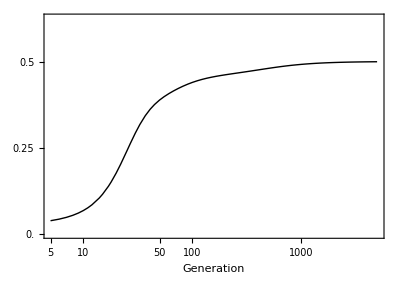

```mathematica
tryR=0.001;
param={tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,trywAf,trywaf,trywAm,trywam,tryαf,tryαm,tryr,tryR,tryr (1-tryR)+tryR (1-tryr),tryk};
run[0]=generation[param,startgen[sieve[tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,trywAf,trywaf,trywAm,trywam,tryαf,tryαm,tryr][[1]],trypm]];
For[time=1,time≤endtime,time++,run[time]=generation[param,run[time-1]]
]
MODtab1Black=Table[{Round[Exp[exptime]],generation[param,run[Round[Exp[exptime]]]].modvec},{exptime,Log[startplot],Log[endtime],0.1}];
MOD1Black=ListLogLinearPlot[MODtab1Black,Joined->True,PlotRange->{{startplot,endtime},{0,0.625}},PlotStyle->{Black,Thick},loglinearplotINVoptions]
```

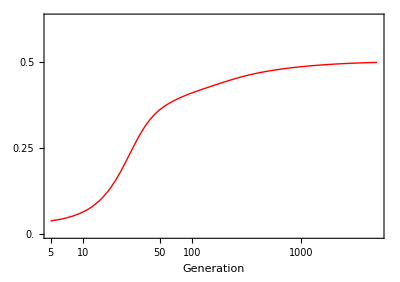

```mathematica
tryR=0.02;
param={tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,trywAf,trywaf,trywAm,trywam,tryαf,tryαm,tryr,tryR,tryr (1-tryR)+tryR (1-tryr),tryk};
run[0]=generation[param,startgen[sieve[tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,trywAf,trywaf,trywAm,trywam,tryαf,tryαm,tryr][[1]],trypm]];
For[time=1,time≤endtime,time++,run[time]=generation[param,run[time-1]]
]
MODtab1Red=Table[{Round[Exp[exptime]],generation[param,run[Round[Exp[exptime]]]].modvec},{exptime,Log[startplot],Log[endtime],0.1}];
MOD1Red=ListLogLinearPlot[MODtab1Red,Joined->True,PlotRange->{{startplot,endtime},{0,0.625}},PlotStyle->{Red,Thick},loglinearplotINVoptions]
```

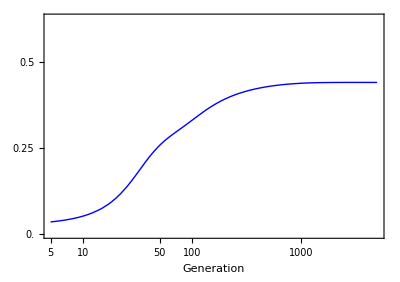

```mathematica
tryR=0.1;
param={tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,trywAf,trywaf,trywAm,trywam,tryαf,tryαm,tryr,tryR,tryr (1-tryR)+tryR (1-tryr),tryk};
run[0]=generation[param,startgen[sieve[tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,trywAf,trywaf,trywAm,trywam,tryαf,tryαm,tryr][[1]],trypm]];
For[time=1,time≤endtime,time++,run[time]=generation[param,run[time-1]]
]
MODtab1Blue=Table[{Round[Exp[exptime]],generation[param,run[Round[Exp[exptime]]]].modvec},{exptime,Log[startplot],Log[endtime],0.1}];
MOD1Blue=ListLogLinearPlot[MODtab1Blue,Joined->True,PlotRange->{{startplot,endtime},{0,0.625}},PlotStyle->{Blue,Thick},loglinearplotINVoptions]
```

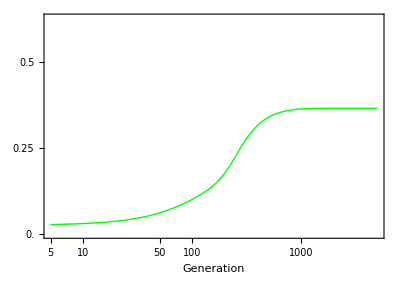

```mathematica
tryR=0.5;
param={tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,trywAf,trywaf,trywAm,trywam,tryαf,tryαm,tryr,tryR,tryr (1-tryR)+tryR (1-tryr),tryk};
run[0]=generation[param,startgen[sieve[tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,trywAf,trywaf,trywAm,trywam,tryαf,tryαm,tryr][[1]],trypm]];
For[time=1,time≤endtime,time++,run[time]=generation[param,run[time-1]]
]
MODtab1Green=Table[{Round[Exp[exptime]],generation[param,run[Round[Exp[exptime]]]].modvec},{exptime,Log[startplot],Log[endtime],0.1}];
MOD1Green=ListLogLinearPlot[MODtab1Green,Joined->True,PlotRange->{{startplot,endtime},{0,0.625}},PlotStyle->{Green,Thick},loglinearplotINVoptions]
```

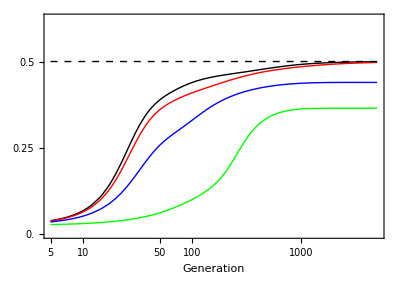

```mathematica
plot1=Show[MOD1Black,MOD1Red,MOD1Blue,MOD1Green,LogLinearPlot[0.5,{x,5,endtime}, PlotStyle->{Black,Dashed}]]
```

#### Parameters (male gametic competition)

```mathematica
tryFAA=1+1/5;
tryFAa=1+(3/4)(1/5);
tryFaa=1;
tryMAA=1+1/5;
tryMAa=1+(3/4)(1/5);
tryMaa=1;
trywAf=1;
trywaf=1;
trywAm=1-1/10;
trywam=1;
tryαf=1/2;
tryαm=1/2;
tryr=1/200;
tryR=0;
subpar1={FAA->tryFAA,FAa->tryFAa,Faa->tryFaa,MAA->tryMAA,MAa->tryMAa,Maa->tryMaa,wAf->trywAf,waf->trywaf,wAm->trywAm,wam->trywam,αf->tryαf,αm->tryαm};
```

#### Invasion Plot

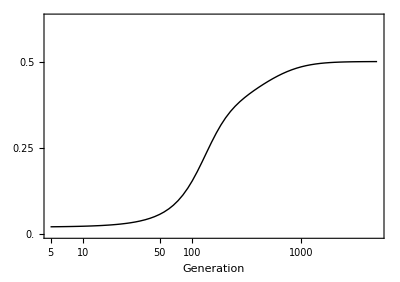

```mathematica
tryR=0.001;
param={tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,trywAf,trywaf,trywAm,trywam,tryαf,tryαm,tryr,tryR,tryr (1-tryR)+tryR (1-tryr),tryk};
run[0]=generation[param,startgen[sieve[tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,trywAf,trywaf,trywAm,trywam,tryαf,tryαm,tryr][[1]],trypm]];
For[time=1,time≤endtime,time++,run[time]=generation[param,run[time-1]]
]
MODtab1Black=Table[{Round[Exp[exptime]],generation[param,run[Round[Exp[exptime]]]].modvec},{exptime,Log[startplot],Log[endtime],0.1}];
MOD1Black=ListLogLinearPlot[MODtab1Black,Joined->True,PlotRange->{{startplot,endtime},{0,0.625}},PlotStyle->{Black,Thick},loglinearplotINVoptions]
```

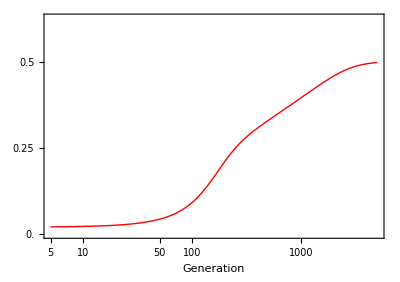

```mathematica
tryR=0.02;
param={tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,trywAf,trywaf,trywAm,trywam,tryαf,tryαm,tryr,tryR,tryr (1-tryR)+tryR (1-tryr),tryk};
run[0]=generation[param,startgen[sieve[tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,trywAf,trywaf,trywAm,trywam,tryαf,tryαm,tryr][[1]],trypm]];
For[time=1,time≤endtime,time++,run[time]=generation[param,run[time-1]]
]
MODtab1Red=Table[{Round[Exp[exptime]],generation[param,run[Round[Exp[exptime]]]].modvec},{exptime,Log[startplot],Log[endtime],0.1}];
MOD1Red=ListLogLinearPlot[MODtab1Red,Joined->True,PlotRange->{{startplot,endtime},{0,0.625}},PlotStyle->{Red,Thick},loglinearplotINVoptions]
```

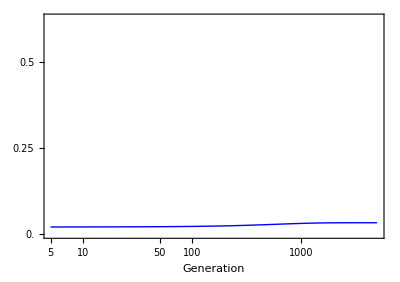

```mathematica
tryR=0.1;
param={tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,trywAf,trywaf,trywAm,trywam,tryαf,tryαm,tryr,tryR,tryr (1-tryR)+tryR (1-tryr),tryk};
run[0]=generation[param,startgen[sieve[tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,trywAf,trywaf,trywAm,trywam,tryαf,tryαm,tryr][[1]],trypm]];
For[time=1,time≤endtime,time++,run[time]=generation[param,run[time-1]]
]
MODtab1Blue=Table[{Round[Exp[exptime]],generation[param,run[Round[Exp[exptime]]]].modvec},{exptime,Log[startplot],Log[endtime],0.1}];
MOD1Blue=ListLogLinearPlot[MODtab1Blue,Joined->True,PlotRange->{{startplot,endtime},{0,0.625}},PlotStyle->{Blue,Thick},loglinearplotINVoptions]
```

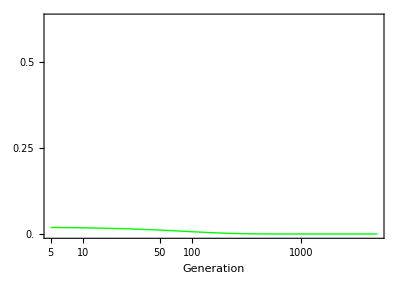

```mathematica
tryR=0.5;
param={tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,trywAf,trywaf,trywAm,trywam,tryαf,tryαm,tryr,tryR,tryr (1-tryR)+tryR (1-tryr),tryk};
run[0]=generation[param,startgen[sieve[tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,trywAf,trywaf,trywAm,trywam,tryαf,tryαm,tryr][[1]],trypm]];
For[time=1,time≤endtime,time++,run[time]=generation[param,run[time-1]]
]
MODtab1Green=Table[{Round[Exp[exptime]],generation[param,run[Round[Exp[exptime]]]].modvec},{exptime,Log[startplot],Log[endtime],0.1}];
MOD1Green=ListLogLinearPlot[MODtab1Green,Joined->True,PlotRange->{{startplot,endtime},{0,0.625}},PlotStyle->{Green,Thick},loglinearplotINVoptions]
```

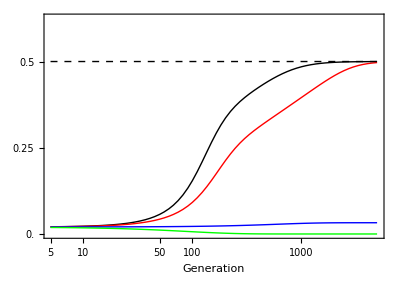

```mathematica
plot2=Show[MOD1Black,MOD1Red,MOD1Blue,MOD1Green,LogLinearPlot[0.5,{x,5,endtime}, PlotStyle->{Black,Dashed}]]
```

#### Parameters (female drive)

```mathematica
tryFAA=1-1/4;
tryFAa=1-(3/4)(1/4);
tryFaa=1;
tryMAA=1-1/4;
tryMAa=1-(3/4)(1/4);
tryMaa=1;
trywAf=1;
trywaf=1;
trywAm=1;
trywam=1;
tryαf=1/2+1/4;
tryαm=1/2;
tryr=1/200;
tryR=0;
subpar1={FAA->tryFAA,FAa->tryFAa,Faa->tryFaa,MAA->tryMAA,MAa->tryMAa,Maa->tryMaa,wAf->trywAf,waf->trywaf,wAm->trywAm,wam->trywam,αf->tryαf,αm->tryαm};
```

#### Invasion Plot

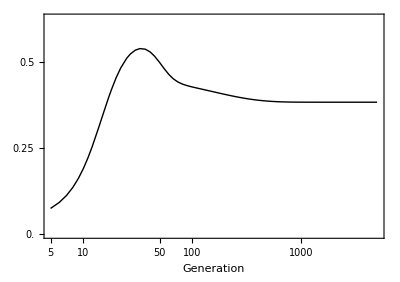

```mathematica
tryR=0.001;
param={tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,trywAf,trywaf,trywAm,trywam,tryαf,tryαm,tryr,tryR,tryr (1-tryR)+tryR (1-tryr),tryk};
run[0]=generation[param,startgen[sieve[tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,trywAf,trywaf,trywAm,trywam,tryαf,tryαm,tryr][[1]],trypm]];
For[time=1,time≤endtime,time++,run[time]=generation[param,run[time-1]]
]
MODtab1Black=Table[{Round[Exp[exptime]],generation[param,run[Round[Exp[exptime]]]].modvec},{exptime,Log[startplot],Log[endtime],0.1}];
MOD1Black=ListLogLinearPlot[MODtab1Black,Joined->True,PlotRange->{{startplot,endtime},{0,0.625}},PlotStyle->{Black,Thick},loglinearplotINVoptions]
```

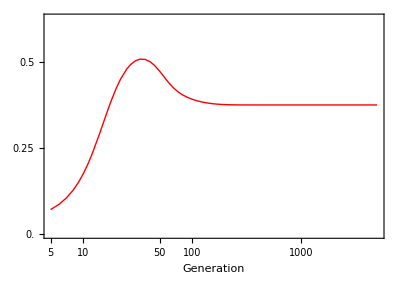

```mathematica
tryR=0.02;
param={tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,trywAf,trywaf,trywAm,trywam,tryαf,tryαm,tryr,tryR,tryr (1-tryR)+tryR (1-tryr),tryk};
run[0]=generation[param,startgen[sieve[tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,trywAf,trywaf,trywAm,trywam,tryαf,tryαm,tryr][[1]],trypm]];
For[time=1,time≤endtime,time++,run[time]=generation[param,run[time-1]]
]
MODtab1Red=Table[{Round[Exp[exptime]],generation[param,run[Round[Exp[exptime]]]].modvec},{exptime,Log[startplot],Log[endtime],0.1}];
MOD1Red=ListLogLinearPlot[MODtab1Red,Joined->True,PlotRange->{{startplot,endtime},{0,0.625}},PlotStyle->{Red,Thick},loglinearplotINVoptions]
```

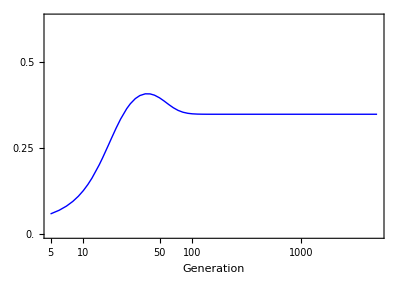

```mathematica
tryR=0.1;
param={tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,trywAf,trywaf,trywAm,trywam,tryαf,tryαm,tryr,tryR,tryr (1-tryR)+tryR (1-tryr),tryk};
run[0]=generation[param,startgen[sieve[tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,trywAf,trywaf,trywAm,trywam,tryαf,tryαm,tryr][[1]],trypm]];
For[time=1,time≤endtime,time++,run[time]=generation[param,run[time-1]]
]
MODtab1Blue=Table[{Round[Exp[exptime]],generation[param,run[Round[Exp[exptime]]]].modvec},{exptime,Log[startplot],Log[endtime],0.1}];
MOD1Blue=ListLogLinearPlot[MODtab1Blue,Joined->True,PlotRange->{{startplot,endtime},{0,0.625}},PlotStyle->{Blue,Thick},loglinearplotINVoptions]
```

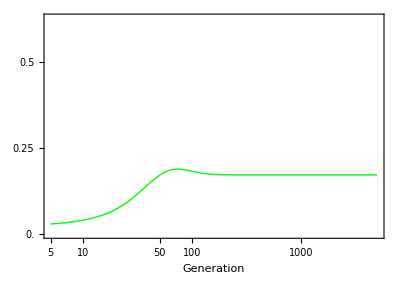

```mathematica
tryR=0.5;
param={tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,trywAf,trywaf,trywAm,trywam,tryαf,tryαm,tryr,tryR,tryr (1-tryR)+tryR (1-tryr),tryk};
run[0]=generation[param,startgen[sieve[tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,trywAf,trywaf,trywAm,trywam,tryαf,tryαm,tryr][[1]],trypm]];
For[time=1,time≤endtime,time++,run[time]=generation[param,run[time-1]]
]
MODtab1Green=Table[{Round[Exp[exptime]],generation[param,run[Round[Exp[exptime]]]].modvec},{exptime,Log[startplot],Log[endtime],0.1}];
MOD1Green=ListLogLinearPlot[MODtab1Green,Joined->True,PlotRange->{{startplot,endtime},{0,0.625}},PlotStyle->{Green,Thick},loglinearplotINVoptions]
```

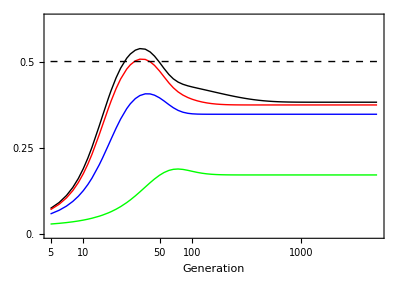

```mathematica
plot3=Show[MOD1Black,MOD1Red,MOD1Blue,MOD1Green,LogLinearPlot[0.5,{x,5,endtime}, PlotStyle->{Black,Dashed}]]
```

#### Parameters (female gametic competition)

```mathematica
tryFAA=1-1/10;
tryFAa=1-(3/4)(1/10);
tryFaa=1;
tryMAA=1-1/10;
tryMAa=1-(3/4)(1/10);
tryMaa=1;
trywAf=1+1/4;
trywaf=1;
trywAm=1;
trywam=1;
tryαf=1/2;
tryαm=1/2;
tryr=1/200;
tryR=0;
subpar1={FAA->tryFAA,FAa->tryFAa,Faa->tryFaa,MAA->tryMAA,MAa->tryMAa,Maa->tryMaa,wAf->trywAf,waf->trywaf,wAm->trywAm,wam->trywam,αf->tryαf,αm->tryαm};
```

#### Invasion Plot

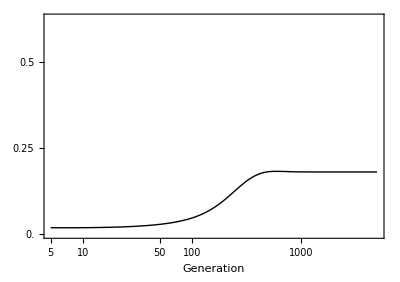

```mathematica
tryR=0.001;
param={tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,trywAf,trywaf,trywAm,trywam,tryαf,tryαm,tryr,tryR,tryr (1-tryR)+tryR (1-tryr),tryk};
run[0]=generation[param,startgen[sieve[tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,trywAf,trywaf,trywAm,trywam,tryαf,tryαm,tryr][[1]],trypm]];
For[time=1,time≤endtime,time++,run[time]=generation[param,run[time-1]]
]
MODtab1Black=Table[{Round[Exp[exptime]],generation[param,run[Round[Exp[exptime]]]].modvec},{exptime,Log[startplot],Log[endtime],0.1}];
MOD1Black=ListLogLinearPlot[MODtab1Black,Joined->True,PlotRange->{{startplot,endtime},{0,0.625}},PlotStyle->{Black,Thick},loglinearplotINVoptions]
```

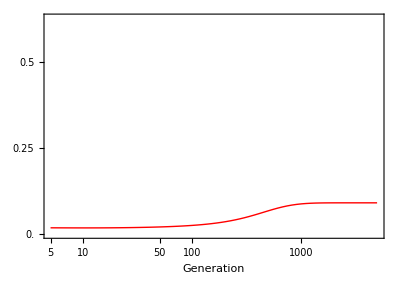

```mathematica
tryR=0.02;
param={tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,trywAf,trywaf,trywAm,trywam,tryαf,tryαm,tryr,tryR,tryr (1-tryR)+tryR (1-tryr),tryk};
run[0]=generation[param,startgen[sieve[tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,trywAf,trywaf,trywAm,trywam,tryαf,tryαm,tryr][[1]],trypm]];
For[time=1,time≤endtime,time++,run[time]=generation[param,run[time-1]]
]
MODtab1Red=Table[{Round[Exp[exptime]],generation[param,run[Round[Exp[exptime]]]].modvec},{exptime,Log[startplot],Log[endtime],0.1}];
MOD1Red=ListLogLinearPlot[MODtab1Red,Joined->True,PlotRange->{{startplot,endtime},{0,0.625}},PlotStyle->{Red,Thick},loglinearplotINVoptions]
```

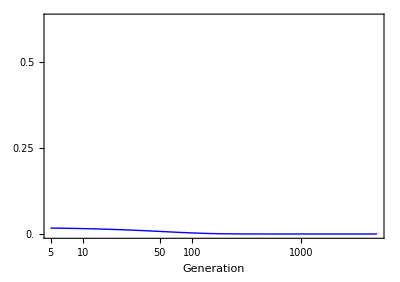

```mathematica
tryR=0.1;
param={tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,trywAf,trywaf,trywAm,trywam,tryαf,tryαm,tryr,tryR,tryr (1-tryR)+tryR (1-tryr),tryk};
run[0]=generation[param,startgen[sieve[tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,trywAf,trywaf,trywAm,trywam,tryαf,tryαm,tryr][[1]],trypm]];
For[time=1,time≤endtime,time++,run[time]=generation[param,run[time-1]]
]
MODtab1Blue=Table[{Round[Exp[exptime]],generation[param,run[Round[Exp[exptime]]]].modvec},{exptime,Log[startplot],Log[endtime],0.1}];
MOD1Blue=ListLogLinearPlot[MODtab1Blue,Joined->True,PlotRange->{{startplot,endtime},{0,0.625}},PlotStyle->{Blue,Thick},loglinearplotINVoptions]
```

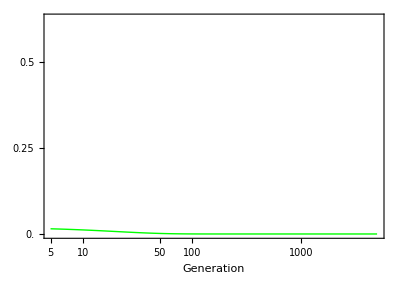

```mathematica
tryR=0.5;
param={tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,trywAf,trywaf,trywAm,trywam,tryαf,tryαm,tryr,tryR,tryr (1-tryR)+tryR (1-tryr),tryk};
run[0]=generation[param,startgen[sieve[tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,trywAf,trywaf,trywAm,trywam,tryαf,tryαm,tryr][[1]],trypm]];
For[time=1,time≤endtime,time++,run[time]=generation[param,run[time-1]]
]
MODtab1Green=Table[{Round[Exp[exptime]],generation[param,run[Round[Exp[exptime]]]].modvec},{exptime,Log[startplot],Log[endtime],0.1}];
MOD1Green=ListLogLinearPlot[MODtab1Green,Joined->True,PlotRange->{{startplot,endtime},{0,0.625}},PlotStyle->{Green,Thick},loglinearplotINVoptions]
```

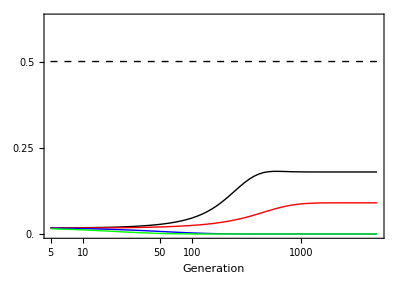

```mathematica
plot4=Show[MOD1Black,MOD1Red,MOD1Blue,MOD1Green,LogLinearPlot[0.5,{x,5,endtime}, PlotStyle->{Black,Dashed}]]
```

#### Rename

```mathematica
plot1ploidantagtemp=plot1;
plot2ploidantagtemp=plot2;
plot3ploidantagtemp=plot3;
plot4ploidantagtemp=plot4;
```

# Combo plot

```mathematica
GraphicsGrid[
{
{
Show[
plot1ploidantag,
Graphics[{Thick,Black,Line[{{-0.075,0.5},{0.05,0.5}}]}],
Epilog->{
Text[Style["A",14,Bold],Scaled@{0.95,0.95}],
Text[Style["λ_WA>1 
& 
λ_Wa>1",14],{-0.275,0.75}],
Text[Style["λ_WA>1 
& 
λ_Wa<1",14],{0.1,0.5}],
Rotate[Text[Style["Diploid selection for A",14],Scaled@{-0.15,0.5}],90 Degree],
Text[Style["Drive for A in males",14],Scaled@{0.5,-0.1}],
Text[Style["*",16,Bold],{-0.1,0.75}]
}
]
,
Show[
plot2ploidantag,
Epilog->{
Text[Style["B",14,Bold],Scaled@{0.95,0.95}],
Text[Style["λ_WA>1
& 
λ_Wa<1",14],{-0.4,0.6}],
Text[Style["Haploid competition for A in males",14],Scaled@{0.5,-0.1}],
Text[Style["*",16,Bold],{-0.1,0.2}]
}
]
,
Show[
plot3ploidantag,
Graphics[{Thick,Black,Line[{{0.25,-0.1},{0.25,0.1}}]}],
Graphics[{Thick,Black,Line[{{0.25,-0.5},{0.2,-0.7}}]}],
Epilog->{
Text[Style["C",14,Bold],Scaled@{0.95,0.95}],
Text[Style["λ_WA>1 
& 
λ_Wa<1",14],{0.25,0.3}],
Text[Style["λ_WA>1 
& 
λ_Wa>1",14],{0.1,-0.75}],
Text[Style["Drive for A in females",14],Scaled@{0.5,-0.1}],
Text[Style["*",16,Bold],{0.25,-0.25}]
}
]
,
Show[
plot4ploidantag,
Epilog->{
Text[Style["D",14,Bold],Scaled@{0.95,0.95}],
Text[Style["λ_WA>1 
& 
λ_Wa<1",14],{0.75,-0.25}],
Text[Style["Haploid competition for A in females",14],Scaled@{0.5,-0.1}],
Text[Style["*",16,Bold],{0.25,-0.1}]
}
]
},
{
Show[
plot1ploidantagtemp,
Epilog->{
Text[Style["E",14,Bold],Scaled@{0.95,0.95}],
Rotate[Text[Style["neo-W frequency",14],Scaled@{-0.15,0.5}],90 Degree]
},
PlotRangeClipping->False
],
Show[
plot2ploidantagtemp,
Epilog->{
Text[Style["F",14,Bold],Scaled@{0.95,0.95}]
}
],
Show[
plot3ploidantagtemp,
Epilog->{
Text[Style["G",14,Bold],Scaled@{0.95,0.95}]
}
],
Show[
plot4ploidantagtemp,
Epilog->{
Text[Style["H",14,Bold],Scaled@{0.95,0.95}]
}
]
}
},
Spacings->{-25,-50}
]

Export[plotdir<>"All_plot_combined_PloidAntag_Matt.pdf",%];
```

-Graphics-